```mathematica
data1={{1.0,0.9995},{1.001,0.997970672314755},{1.0019999999999998,0.996445856116117},{1.0029999999999997,0.9949255328902668},{1.0039999999999996,0.993409684215141},{1.0049999999999994,0.9918982917598846},{1.0059999999999993,0.9903913372843097},{1.0069999999999992,0.9888888026383552},{1.0079999999999991,0.9873906697615529},{1.008999999999999,0.9858969206824947},{1.009999999999999,0.9844075375183062},{1.0109999999999988,0.9829225024741217},{1.0119999999999987,0.9814417978425645},{1.0129999999999986,0.9799654060032288},{1.0139999999999985,0.9784933094221675},{1.0149999999999983,0.9770254906513819},{1.0159999999999982,0.9755619323283158},{1.0169999999999981,0.974102617175352},{1.017999999999998,0.9726475279993136},{1.018999999999998,0.971196647690968},{1.0199999999999978,0.9697499592245339},{1.0209999999999977,0.9683074456571927},{1.0219999999999976,0.9668690901286031},{1.0229999999999975,0.9654348758604174},{1.0239999999999974,0.9640047861558037},{1.0249999999999972,0.9625788043989688},{1.0259999999999971,0.9611569140546864},{1.026999999999997,0.9597390986678275},{1.027999999999997,0.9583253418628938},{1.0289999999999968,0.956915627343555},{1.0299999999999967,0.9555099388921886},{1.0309999999999966,0.9541082603694235},{1.0319999999999965,0.9527105757136858},{1.0329999999999964,0.9513168689407486},{1.0339999999999963,0.9499271241432845},{1.0349999999999961,0.9485413254904204},{1.035999999999996,0.9471594572272964},{1.036999999999996,0.9457815036746278},{1.0379999999999958,0.9444074492282679},{1.0389999999999957,0.9430372783587774},{1.0399999999999956,0.9416709756109924},{1.0409999999999955,0.9403085256035996},{1.0419999999999954,0.9389499130287103},{1.0429999999999953,0.9375951226514412},{1.0439999999999952,0.9362441393094947},{1.044999999999995,0.9348969479127437},{1.045999999999995,0.9335535334428191},{1.0469999999999948,0.9322138809526992},{1.0479999999999947,0.9308779755663029},{1.0489999999999946,0.9295458024780855},{1.0499999999999945,0.9282173469526357},{1.0509999999999944,0.9268925943242775},{1.0519999999999943,0.9255715299966731},{1.0529999999999942,0.9242541394424297},{1.053999999999994,0.922940408202707},{1.054999999999994,0.921630321886829},{1.0559999999999938,0.9203238661718988},{1.0569999999999937,0.9190210268024135},{1.0579999999999936,0.9177217895898852},{1.0589999999999935,0.9164261404124601},{1.0599999999999934,0.9151340652145441},{1.0609999999999933,0.9138455500064292},{1.0619999999999932,0.9125605808639219},{1.062999999999993,0.9112791439279745},{1.063999999999993,0.9100012254043194},{1.0649999999999928,0.908726811563105},{1.0659999999999927,0.9074558887385346},{1.0669999999999926,0.9061884433285067},{1.0679999999999925,0.9049244617942594},{1.0689999999999924,0.9036639306600149},{1.0699999999999923,0.9024068365126284},{1.0709999999999922,0.9011531660012375},{1.071999999999992,0.8999029058369155},{1.072999999999992,0.8986560427923255},{1.0739999999999919,0.8974125637013786},{1.0749999999999917,0.8961724554588918},{1.0759999999999916,0.8949357050202507},{1.0769999999999915,0.8937022994010724},{1.0779999999999914,0.8924722256768718},{1.0789999999999913,0.8912454709827294},{1.0799999999999912,0.890022022512962},{1.080999999999991,0.8888018675207945},{1.081999999999991,0.8875849933180344},{1.0829999999999909,0.8863713872747488},{1.0839999999999907,0.8851610368189428},{1.0849999999999906,0.8839539294362402},{1.0859999999999905,0.8827500526695662},{1.0869999999999904,0.8815493941188322},{1.0879999999999903,0.8803519414406229},{1.0889999999999902,0.8791576823478854},{1.08999999999999,0.8779666046096193},{1.09099999999999,0.87677869605057},{1.0919999999999899,0.8755939445509237},{1.0929999999999898,0.8744123380460035},{1.0939999999999896,0.873233864525969},{1.0949999999999895,0.8720585120355161},{1.0959999999999894,0.8708862686735801},{1.0969999999999893,0.8697171225930398},{1.0979999999999892,0.8685510620004239},{1.098999999999989,0.8673880751556196},{1.099999999999989,0.8662281503715821},{1.1009999999999889,0.8650712760140465},{1.1019999999999888,0.8639174405012421},{1.1029999999999887,0.8627666323036071},{1.1039999999999885,0.8616188399435065},{1.1049999999999884,0.8604740519949515},{1.1059999999999883,0.8593322570833195},{1.1069999999999882,0.8581934438850773},{1.107999999999988,0.8570576011275058},{1.108999999999988,0.8559247175884258},{1.1099999999999879,0.8547947820959256},{1.1109999999999878,0.8536677835280914},{1.1119999999999877,0.8525437108127377},{1.1129999999999876,0.851422552927141},{1.1139999999999874,0.8503042988977739},{1.1149999999999873,0.8491889378000421},{1.1159999999999872,0.8480764587580217},{1.1169999999999871,0.8469668509441993},{1.117999999999987,0.8458601035792129},{1.118999999999987,0.8447562059315952},{1.1199999999999868,0.8436551473175173},{1.1209999999999867,0.8425569171005362},{1.1219999999999866,0.8414615046913405},{1.1229999999999865,0.8403688995475017},{1.1239999999999863,0.839279091173223},{1.1249999999999862,0.838192069119093},{1.1259999999999861,0.8371078229818394},{1.126999999999986,0.8360263424040838},{1.127999999999986,0.8349476170740995},{1.1289999999999858,0.8338716367255691},{1.1299999999999857,0.8327983911373447},{1.1309999999999856,0.8317278701332095},{1.1319999999999855,0.8306600635816406},{1.1329999999999854,0.8295949613955734},{1.1339999999999852,0.8285325535321671},{1.1349999999999851,0.8274728299925723},{1.135999999999985,0.8264157808216995},{1.136999999999985,0.8253613961079892},{1.1379999999999848,0.8243096659831834},{1.1389999999999847,0.8232605806220985},{1.1399999999999846,0.8222141302423999},{1.1409999999999845,0.8211703051043775},{1.1419999999999844,0.8201290955107229},{1.1429999999999843,0.8190904918063071},{1.1439999999999841,0.8180544843779615},{1.144999999999984,0.8170210636542582},{1.145999999999984,0.8159902201052929},{1.1469999999999838,0.8149619442424682},{1.1479999999999837,0.8139362266182792},{1.1489999999999836,0.8129130578261},{1.1499999999999835,0.8118924284999706},{1.1509999999999834,0.8108743293143865},{1.1519999999999833,0.8098587509840898},{1.1529999999999831,0.808845684263859},{1.153999999999983,0.8078351199483035},{1.154999999999983,0.8068270488716566},{1.1559999999999828,0.8058214619075714},{1.1569999999999827,0.8048183499689173},{1.1579999999999826,0.8038177040075772},{1.1589999999999825,0.8028195150142478},{1.1599999999999824,0.8018237740182382},{1.1609999999999823,0.800830472087273},{1.1619999999999822,0.7998396003272933},{1.162999999999982,0.7988511498822619},{1.163999999999982,0.7978651119339676},{1.1649999999999818,0.7968814777018316},{1.1659999999999817,0.7959002384427146},{1.1669999999999816,0.7949213854507259},{1.1679999999999815,0.7939449100570319},{1.1689999999999814,0.7929708036296681},{1.1699999999999813,0.7919990575733501},{1.1709999999999812,0.7910296633292874},{1.171999999999981,0.7900626123749968},{1.172999999999981,0.7890978962241182},{1.1739999999999808,0.7881355064262305},{1.1749999999999807,0.7871754345666697},{1.1759999999999806,0.7862176722663469},{1.1769999999999805,0.7852622111815679},{1.1779999999999804,0.7843090430038544},{1.1789999999999803,0.783358159459765},{1.1799999999999802,0.7824095523107184},{1.18099999999998,0.781463213352818},{1.18199999999998,0.7805191344166752},{1.1829999999999798,0.7795773073672368},{1.1839999999999797,0.7786377241036113},{1.1849999999999796,0.7777003765588966},{1.1859999999999795,0.7767652567000098},{1.1869999999999794,0.7758323565275166},{1.1879999999999793,0.7749016680754625},{1.1889999999999792,0.7739731834112046},{1.189999999999979,0.773046894635245},{1.190999999999979,0.7721227938810648},{1.1919999999999789,0.7712008733149581},{1.1929999999999787,0.7702811251358693},{1.1939999999999786,0.7693635415752291},{1.1949999999999785,0.7684481148967925},{1.1959999999999784,0.7675348373964777},{1.1969999999999783,0.7666237014022054},{1.1979999999999782,0.76571469927374},{1.198999999999978,0.7648078234025313},{1.199999999999978,0.7639030662115562},{1.2009999999999779,0.7630004201551631},{1.2019999999999778,0.7620998777189155},{1.2029999999999776,0.7612014314194374},{1.2039999999999775,0.7603050738042598},{1.2049999999999774,0.7594107974516676},{1.2059999999999773,0.7585185949705473},{1.2069999999999772,0.7576284590002361},{1.207999999999977,0.7567403822103712},{1.208999999999977,0.7558543573007406},{1.2099999999999769,0.7549703770011345},{1.2109999999999768,0.7540884340711976},{1.2119999999999767,0.7532085213002826},{1.2129999999999765,0.7523306315073033},{1.2139999999999764,0.7514547575405902},{1.2149999999999763,0.7505808922777457},{1.2159999999999762,0.7497090286255008},{1.216999999999976,0.7488391595195723},{1.217999999999976,0.747971277924521},{1.2189999999999759,0.7471053768336109},{1.2199999999999758,0.7462414492686683},{1.2209999999999757,0.7453794882799429},{1.2219999999999756,0.7445194869459691},{1.2229999999999754,0.743661438373428},{1.2239999999999753,0.7428053356970101},{1.2249999999999752,0.7419511720792797},{1.225999999999975,0.741098940710539},{1.226999999999975,0.740248634808693},{1.227999999999975,0.7394002476191162},{1.2289999999999748,0.738553772414519},{1.2299999999999747,0.7377092024948154},{1.2309999999999746,0.7368665311869914},{1.2319999999999744,0.7360257518449737},{1.2329999999999743,0.7351868578494997},{1.2339999999999742,0.7343498426079883},{1.2349999999999741,0.7335146995544108},{1.235999999999974,0.7326814221491633},{1.236999999999974,0.7318500038789388},{1.2379999999999738,0.7310204382566013},{1.2389999999999737,0.7301927188210596},{1.2399999999999736,0.7293668391371421},{1.2409999999999735,0.7285427927954726},{1.2419999999999733,0.7277205734123466},{1.2429999999999732,0.726900174629608},{1.2439999999999731,0.7260815901145272},{1.244999999999973,0.7252648135596789},{1.245999999999973,0.7244498386828214},{1.2469999999999728,0.7236366592267767},{1.2479999999999727,0.72282526895931},{1.2489999999999726,0.7220156616730117},{1.2499999999999725,0.7212078311851785},{1.2509999999999724,0.7204017713376962},{1.2519999999999722,0.7195974759969224},{1.2529999999999721,0.7187949390535698},{1.253999999999972,0.7179941544225921},{1.254999999999972,0.7171951160430671},{1.2559999999999718,0.7163978178780835},{1.2569999999999717,0.7156022539146271},{1.2579999999999716,0.7148084181634669},{1.2589999999999715,0.7140163046590438},{1.2599999999999714,0.7132259074593574},{1.2609999999999713,0.7124372206458564},{1.2619999999999711,0.7116502383233262},{1.262999999999971,0.7108649546197802},{1.263999999999971,0.71008136368635},{1.2649999999999708,0.7092994596971767},{1.2659999999999707,0.7085192368493024},{1.2669999999999706,0.7077406893625631},{1.2679999999999705,0.7069638114794814},{1.2689999999999704,0.70618859746516},{1.2699999999999703,0.7054150416071763},{1.2709999999999702,0.7046431382154763},{1.27199999999997,0.7038728816222712},{1.27299999999997,0.7031042661819326},{1.2739999999999698,0.7023372862708886},{1.2749999999999697,0.7015719362875219},{1.2759999999999696,0.7008082106520663},{1.2769999999999695,0.7000461038065059},{1.2779999999999694,0.6992856102144731},{1.2789999999999693,0.6985267243611482},{1.2799999999999692,0.6977694407531593},{1.280999999999969,0.6970137539184824},{1.281999999999969,0.696259658406343},{1.2829999999999688,0.6955071487871165},{1.2839999999999687,0.6947562196522313},{1.2849999999999686,0.6940068656140709},{1.2859999999999685,0.6932590813058765},{1.2869999999999684,0.6925128613816515},{1.2879999999999683,0.691768200516065},{1.2889999999999682,0.6910250934043568},{1.289999999999968,0.6902835347622422},{1.290999999999968,0.6895435193258181},{1.2919999999999678,0.6888050418514688},{1.2929999999999677,0.688068097115773},{1.2939999999999676,0.6873326799154107},{1.2949999999999675,0.6865987850670714},{1.2959999999999674,0.6858664074073618},{1.2969999999999673,0.6851355417927146},{1.2979999999999672,0.6844061830992981},{1.298999999999967,0.6836783262229251},{1.299999999999967,0.6829519660789637},{1.3009999999999668,0.682227097602248},{1.3019999999999667,0.6815037157469886},{1.3029999999999666,0.6807818154866849},{1.3039999999999665,0.6800613918140369},{1.3049999999999664,0.6793424397408574},{1.3059999999999663,0.6786249542979856},{1.3069999999999662,0.6779089305352004},{1.307999999999966,0.6771943635211338},{1.308999999999966,0.6764812483431865},{1.3099999999999659,0.6757695801074414},{1.3109999999999657,0.6750593539385799},{1.3119999999999656,0.6743505649797974},{1.3129999999999655,0.6736432083927193},{1.3139999999999654,0.6729372793573178},{1.3149999999999653,0.6722327730718292},{1.3159999999999652,0.6715296847526709},{1.316999999999965,0.6708280096343602},{1.317999999999965,0.670127742969432},{1.3189999999999649,0.6694288800283582},{1.3199999999999648,0.6687314160994665},{1.3209999999999646,0.6680353464888606},{1.3219999999999645,0.6673406665203401},{1.3229999999999644,0.6666473715353204},{1.3239999999999643,0.665955456892755},{1.3249999999999642,0.665264917969056},{1.325999999999964,0.664575750158016},{1.326999999999964,0.6638879488707307},{1.3279999999999639,0.663201509535521},{1.3289999999999638,0.6625164275978564},{1.3299999999999637,0.6618326985202786},{1.3309999999999635,0.6611503177823248},{1.3319999999999634,0.6604692808804524},{1.3329999999999633,0.6597895833279637},{1.3339999999999632,0.6591112206549304},{1.334999999999963,0.6584341884081196},{1.335999999999963,0.6577584821509194},{1.3369999999999629,0.6570840974632649},{1.3379999999999628,0.6564110299415653},{1.3389999999999627,0.6557392751986304},{1.3399999999999626,0.6550688288635982},{1.3409999999999624,0.6543996865818629},{1.3419999999999623,0.6537318440150022},{1.3429999999999622,0.6530652968407066},{1.3439999999999621,0.652400040752708},{1.344999999999962,0.6517360714607088},{1.345999999999962,0.6510733846903115},{1.3469999999999618,0.6504119761829492},{1.3479999999999617,0.649751841695815},{1.3489999999999616,0.6490929770017936},{1.3499999999999615,0.6484353778893917},{1.3509999999999613,0.6477790401626697},{1.3519999999999612,0.6471239596411736},{1.3529999999999611,0.6464701321598668},{1.353999999999961,0.6458175535690627},{1.354999999999961,0.6451662197343576},{1.3559999999999608,0.6445161265365638},{1.3569999999999607,0.6438672698716429},{1.3579999999999606,0.6432196456506402},{1.3589999999999605,0.6425732497996179},{1.3599999999999604,0.6419280782595912},{1.3609999999999602,0.6412841269864612},{1.3619999999999601,0.6406413919509519},{1.36299999999996,0.6399998691385445},{1.36399999999996,0.6393595545494138},{1.3649999999999598,0.6387204441983648},{1.3659999999999597,0.638082534114768},{1.3669999999999596,0.6374458203424975},{1.3679999999999595,0.6368102989398675},{1.3689999999999594,0.6361759659795697},{1.3699999999999593,0.6355428175486115},{1.3709999999999591,0.6349108497482538},{1.371999999999959,0.63428005869395},{1.372999999999959,0.633650440515284},{1.3739999999999588,0.6330219913559095},{1.3749999999999587,0.6323947073734899},{1.3759999999999586,0.6317685847396373},{1.3769999999999585,0.6311436196398529},{1.3779999999999584,0.6305198082734669},{1.3789999999999583,0.6298971468535797},{1.3799999999999581,0.6292756316070022},{1.380999999999958,0.6286552587741971},{1.381999999999958,0.6280360246092209},{1.3829999999999578,0.6274179253796649},{1.3839999999999577,0.626800957366598},{1.3849999999999576,0.626185116864509},{1.3859999999999575,0.6255704001812485},{1.3869999999999574,0.624956803637973},{1.3879999999999573,0.624344323569087},{1.3889999999999572,0.6237329563221875},{1.389999999999957,0.6231226982580071},{1.390999999999957,0.6225135457503586},{1.3919999999999568,0.621905495186079},{1.3929999999999567,0.6212985429649744},{1.3939999999999566,0.6206926854997651},{1.3949999999999565,0.6200879192160301},{1.3959999999999564,0.6194842405521535},{1.3969999999999563,0.6188816459592694},{1.3979999999999562,0.6182801319012089},{1.398999999999956,0.6176796948544454},{1.399999999999956,0.6170803313080417},{1.4009999999999558,0.6164820377635972},{1.4019999999999557,0.6158848107351939},{1.4029999999999556,0.6152886467493445},{1.4039999999999555,0.6146935423449402},{1.4049999999999554,0.6140994940731984},{1.4059999999999553,0.6135064984976105},{1.4069999999999552,0.6129145521938908},{1.407999999999955,0.6123236517499246},{1.408999999999955,0.6117337937657179},{1.4099999999999548,0.6111449748533457},{1.4109999999999547,0.6105571916369021},{1.4119999999999546,0.6099704407524497},{1.4129999999999545,0.6093847188479693},{1.4139999999999544,0.6088000225833108},{1.4149999999999543,0.6082163486301425},{1.4159999999999542,0.6076336936719028},{1.416999999999954,0.6070520544037502},{1.417999999999954,0.6064714275325154},{1.4189999999999539,0.6058918097766519},{1.4199999999999537,0.6053131978661883},{1.4209999999999536,0.6047355885426794},{1.4219999999999535,0.604158978559159},{1.4229999999999534,0.6035833646800914},{1.4239999999999533,0.6030087436813251},{1.4249999999999532,0.6024351123500443},{1.425999999999953,0.6018624674847232},{1.426999999999953,0.6012908058950786},{1.4279999999999529,0.6007201244020233},{1.4289999999999528,0.6001504198376202},{1.4299999999999526,0.5995816890450358},{1.4309999999999525,0.5990139288784949},{1.4319999999999524,0.5984471362032342},{1.4329999999999523,0.597881307895458},{1.4339999999999522,0.5973164408422921},{1.434999999999952,0.5967525319417394},{1.435999999999952,0.5961895781026351},{1.4369999999999519,0.5956275762446018},{1.4379999999999518,0.5950665232980057},{1.4389999999999517,0.5945064162039124},{1.4399999999999515,0.5939472519140429},{1.4409999999999514,0.5933890273907299},{1.4419999999999513,0.5928317396068746},{1.4429999999999512,0.5922753855459035},{1.443999999999951,0.591719962201725},{1.444999999999951,0.5911654665786868},{1.4459999999999509,0.5906118956915338},{1.4469999999999508,0.590059246565365},{1.4479999999999507,0.5895075162355914},{1.4489999999999505,0.5889567017478945},{1.4499999999999504,0.5884068001581839},{1.4509999999999503,0.5878578085325563},{1.4519999999999502,0.5873097239472537},{1.45299999999995,0.5867625434886222},{1.45399999999995,0.5862162642530715},{1.4549999999999499,0.5856708833470335},{1.4559999999999498,0.5851263978869222},{1.4569999999999497,0.584582804999093},{1.4579999999999496,0.5840401018198026},{1.4589999999999494,0.583498285495169},{1.4599999999999493,0.5829573531811317},{1.4609999999999492,0.5824173020434119},{1.4619999999999491,0.5818781292574734},{1.462999999999949,0.5813398320084829},{1.463999999999949,0.5808024074912715},{1.4649999999999488,0.5802658529102953},{1.4659999999999487,0.579730165479597},{1.4669999999999486,0.5791953424227672},{1.4679999999999485,0.5786613809729062},{1.4689999999999483,0.5781282783725861},{1.4699999999999482,0.5775960318738123},{1.4709999999999481,0.5770646387379861},{1.471999999999948,0.576534096235867},{1.472999999999948,0.5760044016475357},{1.4739999999999478,0.575475552262356},{1.4749999999999477,0.5749475453789381},{1.4759999999999476,0.574420378305102},{1.4769999999999475,0.5738940483578406},{1.4779999999999474,0.5733685528632833},{1.4789999999999472,0.572843889156659},{1.4799999999999471,0.5723200545822608},{1.480999999999947,0.5717970464934092},{1.481999999999947,0.5712748622524171},{1.4829999999999468,0.570753499230553},{1.4839999999999467,0.5702329548080064},{1.4849999999999466,0.569713226373852},{1.4859999999999465,0.5691943113260148},{1.4869999999999464,0.5686762070712349},{1.4879999999999463,0.5681589110250324},{1.4889999999999461,0.567642420611673},{1.489999999999946,0.5671267332641338},{1.490999999999946,0.5666118464240683},{1.4919999999999458,0.5660977575417725},{1.4929999999999457,0.5655844640761509},{1.4939999999999456,0.5650719634946823},{1.4949999999999455,0.5645602532733863},{1.4959999999999454,0.5640493308967901},{1.4969999999999453,0.5635391938578944},{1.4979999999999452,0.5630298396581406},{1.498999999999945,0.5625212658073773},{1.499999999999945,0.5620134698238277},{1.5009999999999448,0.5615064492340569},{1.5019999999999447,0.561000201572939},{1.5029999999999446,0.5604947243836242},{1.5039999999999445,0.5599900152175078},{1.5049999999999444,0.5594860716341963},{1.5059999999999443,0.5589828912014766},{1.5069999999999442,0.5584804714952836},{1.507999999999944,0.5579788100996687},{1.508999999999944,0.5574779046067677},{1.5099999999999438,0.5569777526167701},{1.5109999999999437,0.5564783517378872},{1.5119999999999436,0.5559796995863212},{1.5129999999999435,0.5554817937862342},{1.5139999999999434,0.5549846319697171},{1.5149999999999433,0.5544882117767591},{1.5159999999999432,0.5539925308552169},{1.516999999999943,0.5534975868607847},{1.517999999999943,0.553003377456963},{1.5189999999999428,0.5525099003150296},{1.5199999999999427,0.5520171531140086},{1.5209999999999426,0.551525133540641},{1.5219999999999425,0.5510338392893549},{1.5229999999999424,0.5505432680622355},{1.5239999999999423,0.5500534175689963},{1.5249999999999422,0.5495642855269491},{1.525999999999942,0.5490758696609752},{1.526999999999942,0.5485881677034962},{1.5279999999999418,0.5481011773944449},{1.5289999999999417,0.5476148964812365},{1.5299999999999416,0.5471293227187405},{1.5309999999999415,0.5466444538692514},{1.5319999999999414,0.5461602877024604},{1.5329999999999413,0.5456768219954272},{1.5339999999999412,0.5451940545325524},{1.534999999999941,0.5447119831055487},{1.535999999999941,0.5442306055134132},{1.5369999999999409,0.5437499195623996},{1.5379999999999407,0.543269923065991},{1.5389999999999406,0.5427906138448715},{1.5399999999999405,0.5423119897268995},{1.5409999999999404,0.5418340485470805},{1.5419999999999403,0.5413567881475392},{1.5429999999999402,0.5408802063774933},{1.54399999999994,0.5404043010932261},{1.54499999999994,0.5399290701580597},{1.5459999999999399,0.5394545114423285},{1.5469999999999398,0.5389806228233525},{1.5479999999999396,0.5385074021854113},{1.5489999999999395,0.5380348474197172},{1.5499999999999394,0.5375629564243893},{1.5509999999999393,0.5370917271044277},{1.5519999999999392,0.5366211573716868},{1.552999999999939,0.5361512451448502},{1.553999999999939,0.5356819883494048},{1.5549999999999389,0.5352133849176148},{1.5559999999999388,0.5347454327884967},{1.5569999999999387,0.5342781299077937},{1.5579999999999385,0.5338114742279504},{1.5589999999999384,0.5333454637080877},{1.5599999999999383,0.5328800963139776},{1.5609999999999382,0.532415370018019},{1.561999999999938,0.5319512827992118},{1.562999999999938,0.5314878326431328},{1.5639999999999379,0.5310250175419113},{1.5649999999999378,0.5305628354942044},{1.5659999999999377,0.530101284505172},{1.5669999999999376,0.5296403625864538},{1.5679999999999374,0.5291800677561439},{1.5689999999999373,0.5287203980387677},{1.5699999999999372,0.5282613514652575},{1.5709999999999371,0.5278029260729287},{1.571999999999937,0.527345119905456},{1.572999999999937,0.52688793101285},{1.5739999999999368,0.5264313574514335},{1.5749999999999367,0.5259753972838181},{1.5759999999999366,0.525520048578881},{1.5769999999999365,0.5250653094117418},{1.5779999999999363,0.524611177863739},{1.5789999999999362,0.5241576520224077},{1.5799999999999361,0.5237047299814562},{1.580999999999936,0.5232524098407434},{1.581999999999936,0.5228006897062557},{1.5829999999999358,0.5223495676900849},{1.5839999999999357,0.5218990419104055},{1.5849999999999356,0.5214491104914525},{1.5859999999999355,0.5209997715634986},{1.5869999999999354,0.5205510232628326},{1.5879999999999352,0.5201028637317366},{1.5889999999999351,0.5196552911184648},{1.589999999999935,0.5192083035772209},{1.590999999999935,0.5187618992681368},{1.5919999999999348,0.5183160763572503},{1.5929999999999347,0.5178708330164842},{1.5939999999999346,0.5174261674236241},{1.5949999999999345,0.5169820777622977},{1.5959999999999344,0.5165385622219522},{1.5969999999999342,0.5160956189978345},{1.5979999999999341,0.5156532462909693},{1.598999999999934,0.5152114423081382},{1.599999999999934,0.5147702052618582},{1.6009999999999338,0.5143295333703617},{1.6019999999999337,0.5138894248575753},{1.6029999999999336,0.5134498779530988},{1.6039999999999335,0.5130108908921852},{1.6049999999999334,0.5125724619157196},{1.6059999999999333,0.5121345892701992},{1.6069999999999331,0.5116972712077127},{1.607999999999933,0.5112605059859202},{1.608999999999933,0.510824291868033},{1.6099999999999328,0.5103886271227934},{1.6109999999999327,0.5099535100244549},{1.6119999999999326,0.509518938852762},{1.6129999999999325,0.5090849118929308},{1.6139999999999324,0.5086514274356291},{1.6149999999999323,0.5082184837769563},{1.6159999999999322,0.5077860792184248},{1.616999999999932,0.5073542120669395},{1.617999999999932,0.506922880634779},{1.6189999999999318,0.5064920832395762},{1.6199999999999317,0.506061818204299},{1.6209999999999316,0.5056320838572311},{1.6219999999999315,0.5052028785319533},{1.6229999999999314,0.504774200567324},{1.6239999999999313,0.5043460483074607},{1.6249999999999312,0.5039184201017207},{1.625999999999931,0.5034913143046831},{1.626999999999931,0.5030647292761294},{1.6279999999999308,0.5026386633810256},{1.6289999999999307,0.5022131149895029},{1.6299999999999306,0.5017880824768403},{1.6309999999999305,0.5013635642234452},{1.6319999999999304,0.5009395586148359},{1.6329999999999303,0.5005160640416231},{1.6339999999999302,0.5000930788994918},{1.63499999999993,0.4996706015891836},{1.63599999999993,0.4992486305164781},{1.6369999999999298,0.4988271640921756},{1.6379999999999297,0.49840620073207903},{1.6389999999999296,0.49798573885697645},{1.6399999999999295,0.49756577689262316},{1.6409999999999294,0.49714631326972425},{1.6419999999999293,0.496727346423917},{1.6429999999999292,0.4963088747957536},{1.643999999999929,0.49589089683068377},{1.644999999999929,0.4954734109790374},{1.6459999999999289,0.49505641569600733},{1.6469999999999287,0.4946399094416325},{1.6479999999999286,0.4942238906807806},{1.6489999999999285,0.4938083578831311},{1.6499999999999284,0.4933933095231584},{1.6509999999999283,0.4929787440801151},{1.6519999999999282,0.4925646600380151},{1.652999999999928,0.4921510558856169},{1.653999999999928,0.4917379301164072},{1.6549999999999279,0.4913252812285837},{1.6559999999999278,0.49091310772503943},{1.6569999999999276,0.4905014081133458},{1.6579999999999275,0.4900901809057364},{1.6589999999999274,0.48967942461909086},{1.6599999999999273,0.4892691377749183},{1.6609999999999272,0.4888593188993414},{1.661999999999927,0.4884499665230806},{1.662999999999927,0.4880410791814374},{1.6639999999999269,0.487632655414279},{1.6649999999999268,0.4872246937660223},{1.6659999999999267,0.4868171927856178},{1.6669999999999265,0.4864101510265343},{1.6679999999999264,0.48600356704674286},{1.6689999999999263,0.48559743940870154},{1.6699999999999262,0.4851917666793394},{1.670999999999926,0.4847865474300413},{1.671999999999926,0.4843817802366327},{1.6729999999999259,0.4839774636793637},{1.6739999999999258,0.4835735963428943},{1.6749999999999257,0.483170176816279},{1.6759999999999255,0.48276720369295145},{1.6769999999999254,0.4823646755707096},{1.6779999999999253,0.4819625910517006},{1.6789999999999252,0.48156094874240574},{1.679999999999925,0.4811597472536257},{1.680999999999925,0.4807589852004655},{1.6819999999999249,0.4803586612023199},{1.6829999999999248,0.47995877388285857},{1.6839999999999247,0.4795593218700113},{1.6849999999999246,0.47916030379595376},{1.6859999999999244,0.4787617182970925},{1.6869999999999243,0.47836356401405083},{1.6879999999999242,0.4779658395916543},{1.6889999999999241,0.4775685436789161},{1.689999999999924,0.4771716749290232},{1.690999999999924,0.4767752319993215},{1.6919999999999238,0.47637921355130225},{1.6929999999999237,0.4759836182505875},{1.6939999999999236,0.47558844476691614},{1.6949999999999235,0.47519369177413023},{1.6959999999999233,0.47479935795016054},{1.6969999999999232,0.4744054419770126},{1.6979999999999231,0.4740119425407536},{1.698999999999923,0.4736188583314977},{1.699999999999923,0.473226188043393},{1.7009999999999228,0.47283393037460736},{1.7019999999999227,0.4724420840273151},{1.7029999999999226,0.47205064770768324},{1.7039999999999225,0.47165962012585827},{1.7049999999999224,0.4712689999959523},{1.7059999999999222,0.47087878603603},{1.7069999999999221,0.47048897696809516},{1.707999999999922,0.4700995715180774},{1.708999999999922,0.4697105684158188},{1.7099999999999218,0.4693219663950609},{1.7109999999999217,0.46893376419343163},{1.7119999999999216,0.4685459605524319},{1.7129999999999215,0.468158554217423},{1.7139999999999214,0.46777154393761333},{1.7149999999999213,0.4673849284660456},{1.7159999999999211,0.46699870655958403},{1.716999999999921,0.4666128769789013},{1.717999999999921,0.46622743848846626},{1.7189999999999208,0.46584238985653076},{1.7199999999999207,0.46545772985511724},{1.7209999999999206,0.46507345726000593},{1.7219999999999205,0.4646895708507225},{1.7229999999999204,0.46430606941052543},{1.7239999999999203,0.4639229517263937},{1.7249999999999202,0.46354021658901434},{1.72599999999992,0.4631578627927699},{1.72699999999992,0.46277588913572637},{1.7279999999999198,0.46239429441962093},{1.7289999999999197,0.46201307744984954},{1.7299999999999196,0.46163223703545486},{1.7309999999999195,0.4612517719891145},{1.7319999999999194,0.4608716811271283},{1.7329999999999193,0.46049196326940695},{1.7339999999999192,0.4601126172394597},{1.734999999999919,0.4597336418643826},{1.735999999999919,0.4593550359748464},{1.7369999999999188,0.4589767984050851},{1.7379999999999187,0.45859892799288376},{1.7389999999999186,0.4582214235795671},{1.7399999999999185,0.4578442840099877},{1.7409999999999184,0.4574675081325145},{1.7419999999999183,0.4570910947990211},{1.7429999999999182,0.456715042864874},{1.743999999999918,0.45633935118892177},{1.744999999999918,0.4559640186334828},{1.7459999999999178,0.45558904406433454},{1.7469999999999177,0.4552144263507018},{1.7479999999999176,0.4548401643652456},{1.7489999999999175,0.4544662569840519},{1.7499999999999174,0.45409270308662025},{1.7509999999999173,0.4537195015558527},{1.7519999999999172,0.45334665127804274},{1.752999999999917,0.45297415114286416},{1.753999999999917,0.4526020000433599},{1.7549999999999168,0.4522301968759312},{1.7559999999999167,0.45185874054032665},{1.7569999999999166,0.4514876299396313},{1.7579999999999165,0.45111686398025574},{1.7589999999999164,0.450746441571925},{1.7599999999999163,0.45037636162766825},{1.7609999999999162,0.45000662306380784},{1.761999999999916,0.4496372247999486},{1.762999999999916,0.4492681657589673},{1.7639999999999159,0.44889944486700184},{1.7649999999999157,0.44853106105344087},{1.7659999999999156,0.44816301325091307},{1.7669999999999155,0.44779530039527676},{1.7679999999999154,0.4474279214256096},{1.7689999999999153,0.44706087528419797},{1.7699999999999152,0.44669416091652664},{1.770999999999915,0.44632777727126854},{1.771999999999915,0.4459617233002744},{1.7729999999999149,0.4455959979585626},{1.7739999999999148,0.4452306002043089},{1.7749999999999146,0.44486552899883625},{1.7759999999999145,0.4445007833066048},{1.7769999999999144,0.4441363620952016},{1.7779999999999143,0.4437722643353307},{1.7789999999999142,0.44340848900080315},{1.779999999999914,0.44304503506852716},{1.780999999999914,0.4426819015184979},{1.7819999999999139,0.44231908733378766},{1.7829999999999138,0.44195659150053623},{1.7839999999999137,0.4415944130079409},{1.7849999999999135,0.44123255084824664},{1.7859999999999134,0.44087100401673657},{1.7869999999999133,0.4405097715117221},{1.7879999999999132,0.4401488523345334},{1.788999999999913,0.43978824548950957},{1.789999999999913,0.43942794998398926},{1.7909999999999129,0.43906796482830107},{1.7919999999999128,0.43870828903575404},{1.7929999999999127,0.4383489216226281},{1.7939999999999126,0.4379898616081648},{1.7949999999999124,0.4376311080145576},{1.7959999999999123,0.437272659866943},{1.7969999999999122,0.43691451619339067},{1.7979999999999121,0.43655667602489445},{1.798999999999912,0.4361991383953631},{1.799999999999912,0.43584190234161113},{1.8009999999999118,0.4354849669033494},{1.8019999999999117,0.4351283311231763},{1.8029999999999116,0.4347719940465681},{1.8039999999999115,0.43441595472187056},{1.8049999999999113,0.4340602122002893},{1.8059999999999112,0.4337047655358811},{1.8069999999999111,0.4333496137855449},{1.807999999999911,0.4329947560090127},{1.808999999999911,0.43264019126884096},{1.8099999999999108,0.4322859186304012},{1.8109999999999107,0.43193193716187184},{1.8119999999999106,0.43157824593422883},{1.8129999999999105,0.43122484402123723},{1.8139999999999104,0.4308717304994422},{1.8149999999999102,0.4305189044481608},{1.8159999999999101,0.43016636494947263},{1.81699999999991,0.4298141110882116},{1.81799999999991,0.42946214195195737},{1.8189999999999098,0.42911045663102654},{1.8199999999999097,0.4287590542184643},{1.8209999999999096,0.4284079338100358},{1.8219999999999095,0.4280570945042178},{1.8229999999999094,0.4277065354021902},{1.8239999999999092,0.42735625560782764},{1.8249999999999091,0.427006254227691},{1.825999999999909,0.42665653037101925},{1.826999999999909,0.4263070831497208},{1.8279999999999088,0.4259579116783658},{1.8289999999999087,0.4256090150741771},{1.8299999999999086,0.4252603924570228},{1.8309999999999085,0.4249120429494076},{1.8319999999999084,0.42456396567646487},{1.8329999999999083,0.42421615976594845},{1.8339999999999081,0.42386862434822437},{1.834999999999908,0.423521358556263},{1.835999999999908,0.42317436152563104},{1.8369999999999078,0.4228276323944834},{1.8379999999999077,0.4224811703035552},{1.8389999999999076,0.422134974396154},{1.8399999999999075,0.42178904381815174},{1.8409999999999074,0.4214433777179769},{1.8419999999999073,0.42109797524660664},{1.8429999999999072,0.42075283555755894},{1.843999999999907,0.42040795780688484},{1.844999999999907,0.4200633411531607},{1.8459999999999068,0.4197189847574804},{1.8469999999999067,0.4193748877834477},{1.8479999999999066,0.4190310493971686},{1.8489999999999065,0.4186874687672435},{1.8499999999999064,0.4183441450647598},{1.8509999999999063,0.4180010774632841},{1.8519999999999062,0.41765826513885473},{1.852999999999906,0.41731570726997436},{1.853999999999906,0.41697340303760233},{1.8549999999999058,0.4166313516251471},{1.8559999999999057,0.4162895522184588},{1.8569999999999056,0.41594800400582216},{1.8579999999999055,0.4156067061779487},{1.8589999999999054,0.41526565792796954},{1.8599999999999053,0.41492485845142807},{1.8609999999999052,0.4145843069462724},{1.861999999999905,0.4142440026128484},{1.862999999999905,0.41390394465389235},{1.8639999999999048,0.41356413227452365},{1.8649999999999047,0.41322456468223756},{1.8659999999999046,0.41288524108689817},{1.8669999999999045,0.4125461607007311},{1.8679999999999044,0.41220732273831634},{1.8689999999999043,0.41186872641658145},{1.8699999999999042,0.4115303709547941},{1.870999999999904,0.4111922555745552},{1.871999999999904,0.4108543794997919},{1.8729999999999039,0.4105167419567508},{1.8739999999999037,0.4101793421739905},{1.8749999999999036,0.4098421793823749},{1.8759999999999035,0.4095052528150664},{1.8769999999999034,0.40916856170751886},{1.8779999999999033,0.4088321052974707},{1.8789999999999032,0.40849588282493826},{1.879999999999903,0.4081598935322086},{1.880999999999903,0.4078241366638332},{1.8819999999999029,0.40748861146662096},{1.8829999999999028,0.40715331718963127},{1.8839999999999026,0.4068182530841676},{1.8849999999999025,0.4064834184037705},{1.8859999999999024,0.40614881240421125},{1.8869999999999023,0.405814434343485},{1.8879999999999022,0.40548028348180426},{1.888999999999902,0.40514635908159224},{1.889999999999902,0.4048126604074763},{1.8909999999999019,0.4044791867262814},{1.8919999999999018,0.40414593730702353},{1.8929999999999017,0.40381291142090336},{1.8939999999999015,0.4034801083412995},{1.8949999999999014,0.4031475273437623},{1.8959999999999013,0.4028151677060073},{1.8969999999999012,0.4024830287079088},{1.897999999999901,0.4021511096314937},{1.898999999999901,0.40181940976093483},{1.8999999999999009,0.40148792838254477},{1.9009999999999008,0.4011566647847695},{1.9019999999999007,0.40082561825818225},{1.9029999999999005,0.40049478809547684},{1.9039999999999004,0.4001641735914619},{1.9049999999999003,0.3998337740430544},{1.9059999999999002,0.39950358874927355},{1.9069999999999,0.39917361701123455},{1.9079999999999,0.3988438581321424},{1.9089999999998999,0.3985143114172858},{1.9099999999998998,0.3981849761740313},{1.9109999999998997,0.39785585171181664},{1.9119999999998996,0.39752693734214534},{1.9129999999998994,0.3971982323785801},{1.9139999999998993,0.39686973613673715},{1.9149999999998992,0.39654144793428},{1.9159999999998991,0.3962133670909135},{1.916999999999899,0.39588549292837816},{1.917999999999899,0.395557824770444},{1.9189999999998988,0.39523036194290445},{1.9199999999998987,0.3949031037735709},{1.9209999999998986,0.39457604959226633},{1.9219999999998985,0.39424919873081976},{1.9229999999998983,0.3939225505230603},{1.9239999999998982,0.3935961043048116},{1.9249999999998981,0.3932698594138857},{1.925999999999898,0.3929438151900775},{1.926999999999898,0.3926179709751587},{1.9279999999998978,0.3922923261128727},{1.9289999999998977,0.3919668799489281},{1.9299999999998976,0.39164163183099365},{1.9309999999998975,0.39131658110869233},{1.9319999999998974,0.39099172713359565},{1.9329999999998972,0.39066706925921807},{1.9339999999998971,0.3903426068410114},{1.934999999999897,0.39001833923635937},{1.935999999999897,0.3896942658045718},{1.9369999999998968,0.3893703859068793},{1.9379999999998967,0.38904669890642735},{1.9389999999998966,0.3887232041682713},{1.9399999999998965,0.38839990105937056},{1.9409999999998964,0.3880767889485832},{1.9419999999998963,0.3877538672066606},{1.9429999999998961,0.38743113520624184},{1.943999999999896,0.38710859232184847},{1.944999999999896,0.3867862379298789},{1.9459999999998958,0.3864640714086032},{1.9469999999998957,0.3861420921381579},{1.9479999999998956,0.38582029950054036},{1.9489999999998955,0.3854986928796035},{1.9499999999998954,0.3851772716610504},{1.9509999999998953,0.38485603523242967},{1.9519999999998952,0.38453498298312916},{1.952999999999895,0.3842141143043715},{1.953999999999895,0.3838934285892087},{1.9549999999998948,0.38357292523251685},{1.9559999999998947,0.3832526036309909},{1.9569999999998946,0.38293246318313967},{1.9579999999998945,0.38261250328928054},{1.9589999999998944,0.38229272335153425},{1.9599999999998943,0.3819731227738201},{1.9609999999998942,0.38165370096185064},{1.961999999999894,0.38133445732312643},{1.962999999999894,0.38101539126693135},{1.9639999999998938,0.3806965022043273},{1.9649999999998937,0.3803777895481493},{1.9659999999998936,0.3800592527130004},{1.9669999999998935,0.3797408911152466},{1.9679999999998934,0.3794227041730122},{1.9689999999998933,0.3791046913061745},{1.9699999999998932,0.37878685193635914},{1.970999999999893,0.378469185486935},{1.971999999999893,0.37815169138300914},{1.9729999999998928,0.3778343690514224},{1.9739999999998927,0.37751721792074416},{1.9749999999998926,0.37720023742126746},{1.9759999999998925,0.37688342698500443},{1.9769999999998924,0.37656678604568117},{1.9779999999998923,0.37625031403873316},{1.9789999999998922,0.37593401040130053},{1.979999999999892,0.375617874572223},{1.980999999999892,0.3753019059920354},{1.9819999999998918,0.37498610410296274},{1.9829999999998917,0.3746704683489157},{1.9839999999998916,0.3743549981754858},{1.9849999999998915,0.37403969302994056},{1.9859999999998914,0.3737245523612192},{1.9869999999998913,0.3734095756199277},{1.9879999999998912,0.3730947622583342},{1.988999999999891,0.3727801117303645},{1.989999999999891,0.37246562349159734},{1.9909999999998909,0.3721512969992597},{1.9919999999998907,0.37183713171222255},{1.9929999999998906,0.37152312709099605},{1.9939999999998905,0.37120928259772507},{1.9949999999998904,0.3708955976961846},{1.9959999999998903,0.3705820718517753},{1.9969999999998902,0.37026870453151906},{1.99799999999989,0.3699554952040544},{1.99899999999989,0.36964244333963214},{1.9999999999998899,0.3693295484101108},{2.0009999999998898,0.3690168098889521},{2.0019999999998896,0.36870422725121677},{2.0029999999998895,0.3683917999735601},{2.0039999999998894,0.3680795275342274},{2.0049999999998893,0.36776740941304975},{2.005999999999889,0.3674554450914397},{2.006999999999889,0.3671436340523866},{2.007999999999889,0.3668319757804528},{2.008999999999889,0.3665204697617687},{2.0099999999998888,0.36620911548402907},{2.0109999999998887,0.3658979124364883},{2.0119999999998885,0.3655868601099562},{2.0129999999998884,0.36527595799679424},{2.0139999999998883,0.36496520559091045},{2.014999999999888,0.3646546023877558},{2.015999999999888,0.3643441478843201},{2.016999999999888,0.3640338415791272},{2.017999999999888,0.3637236829722313},{2.0189999999998878,0.3634136715652125},{2.0199999999998877,0.36310380686117283},{2.0209999999998876,0.3627940883647321},{2.0219999999998874,0.3624845155820235},{2.0229999999998873,0.3621750880206899},{2.0239999999998872,0.36186580518987943},{2.024999999999887,0.3615566666002415},{2.025999999999887,0.36124767176392275},{2.026999999999887,0.36093882019456286},{2.027999999999887,0.3606301114072906},{2.0289999999998867,0.36032154491872},{2.0299999999998866,0.36001312024694593},{2.0309999999998865,0.35970483691154037},{2.0319999999998863,0.3593966944335484},{2.0329999999998862,0.359088692335484},{2.033999999999886,0.3587808301413264},{2.034999999999886,0.35847310737651583},{2.035999999999886,0.3581655235679498},{2.036999999999886,0.357858078243979},{2.0379999999998857,0.35755077093440374},{2.0389999999998856,0.3572436011704695},{2.0399999999998855,0.3569365684848634},{2.0409999999998854,0.3566296724117103},{2.0419999999998852,0.3563229124865689},{2.042999999999885,0.3560162882464278},{2.043999999999885,0.3557097992297018},{2.044999999999885,0.35540344497622817},{2.045999999999885,0.35509722502726254},{2.0469999999998847,0.35479113892547526},{2.0479999999998846,0.3544851862149476},{2.0489999999998845,0.3541793664411681},{2.0499999999998844,0.3538736791510286},{2.0509999999998842,0.35356812389282055},{2.051999999999884,0.35326270021623146},{2.052999999999884,0.35295740767234085},{2.053999999999884,0.35265224581361687},{2.054999999999884,0.3523472141939124},{2.0559999999998837,0.3520423123684614},{2.0569999999998836,0.3517375398938753},{2.0579999999998835,0.3514328963281393},{2.0589999999998834,0.35112838123060874},{2.0599999999998833,0.3508239941620053},{2.060999999999883,0.35051973468441366},{2.061999999999883,0.3502156023612777},{2.062999999999883,0.3499115967573968},{2.063999999999883,0.34960771743892255},{2.0649999999998827,0.3493039639733549},{2.0659999999998826,0.34900033592953883},{2.0669999999998825,0.34869683287766057},{2.0679999999998824,0.3483934543892442},{2.0689999999998823,0.3480902000371479},{2.069999999999882,0.3477870693955609},{2.070999999999882,0.34748406203999954},{2.071999999999882,0.3471811775473038},{2.072999999999882,0.34687841549563403},{2.0739999999998817,0.3465757754644674},{2.0749999999998816,0.3462732570345942},{2.0759999999998815,0.34597085978811487},{2.0769999999998814,0.34566858330843614},{2.0779999999998813,0.3453664271802677},{2.078999999999881,0.34506439098961894},{2.079999999999881,0.3447624743237953},{2.080999999999881,0.34446067677139514},{2.081999999999881,0.34415899792230614},{2.0829999999998807,0.3438574373677021},{2.0839999999998806,0.34355599470003934},{2.0849999999998805,0.34325466951305367},{2.0859999999998804,0.3429534614017567},{2.0869999999998803,0.34265236996243276},{2.08799999999988,0.34235139479263554},{2.08899999999988,0.3420505354911847},{2.08999999999988,0.3417497916581626},{2.09099999999988,0.3414491628949111},{2.0919999999998797,0.3411486488040282},{2.0929999999998796,0.34084824898936467},{2.0939999999998795,0.340547963056021},{2.0949999999998794,0.3402477906103441},{2.0959999999998793,0.339947731259924},{2.096999999999879,0.33964778461359074},{2.097999999999879,0.33934795028141107},{2.098999999999879,0.33904822787468514},{2.099999999999879,0.3387486170059435},{2.1009999999998787,0.3384491172889438},{2.1019999999998786,0.33814972833866774},{2.1029999999998785,0.3378504497713178},{2.1039999999998784,0.33755128120431394},{2.1049999999998783,0.33725222225629087},{2.105999999999878,0.3369532725470946},{2.106999999999878,0.3366544316977795},{2.107999999999878,0.3363556993306049},{2.108999999999878,0.33605707506903226},{2.1099999999998778,0.3357585585377221},{2.1109999999998776,0.33546014936253055},{2.1119999999998775,0.3351618471705068},{2.1129999999998774,0.3348636515898897},{2.1139999999998773,0.33456556225010475},{2.114999999999877,0.33426757878176117},{2.115999999999877,0.3339697008166486},{2.116999999999877,0.33367192798773454},{2.117999999999877,0.33337425992916087},{2.1189999999998768,0.3330766962762411},{2.1199999999998766,0.33277923666545733},{2.1209999999998765,0.3324818807344572},{2.1219999999998764,0.3321846281220511},{2.1229999999998763,0.3318874784682089},{2.123999999999876,0.33159043141405714},{2.124999999999876,0.3312934866018763},{2.125999999999876,0.3309966436750975},{2.126999999999876,0.33069990227829976},{2.1279999999998758,0.33040326205720716},{2.1289999999998757,0.33010672265868574},{2.1299999999998755,0.32981028373074067},{2.1309999999998754,0.3295139449225134},{2.1319999999998753,0.32921770588427873},{2.132999999999875,0.328921566267442},{2.133999999999875,0.3286255257245362},{2.134999999999875,0.32832958390921896},{2.135999999999875,0.32803374047627},{2.1369999999998748,0.327737995081588},{2.1379999999998747,0.327442347382188},{2.1389999999998746,0.32714679703619853},{2.1399999999998744,0.32685134370285857},{2.1409999999998743,0.326555987042515},{2.1419999999998742,0.3262607267166198},{2.142999999999874,0.32596556238772717},{2.143999999999874,0.32567049371949075},{2.144999999999874,0.32537552037666095},{2.145999999999874,0.32508064202508197},{2.1469999999998737,0.32478585833168944},{2.1479999999998736,0.3244911689645073},{2.1489999999998735,0.3241965735926452},{2.1499999999998733,0.32390207188629594},{2.1509999999998732,0.3236076635167323},{2.151999999999873,0.32331334815630497},{2.152999999999873,0.3230191254784392},{2.153999999999873,0.32272499515763264},{2.154999999999873,0.3224309568694525},{2.1559999999998727,0.3221370102905326},{2.1569999999998726,0.321843155098571},{2.1579999999998725,0.32154939097232726},{2.1589999999998724,0.32125571759161986},{2.1599999999998722,0.3209621346373234},{2.160999999999872,0.32066864179136617},{2.161999999999872,0.32037523873672735},{2.162999999999872,0.3200819251574345},{2.163999999999872,0.3197887007385608},{2.1649999999998717,0.3194955651662227},{2.1659999999998716,0.319202518127577},{2.1669999999998715,0.3189095593108186},{2.1679999999998714,0.31861668840517776},{2.1689999999998713,0.3183239051009175},{2.169999999999871,0.3180312090893312},{2.170999999999871,0.31773860006273963},{2.171999999999871,0.317446077714489},{2.172999999999871,0.3171536417389481},{2.1739999999998707,0.3168612918315058},{2.1749999999998706,0.3165690276885684},{2.1759999999998705,0.31627684900755737},{2.1769999999998704,0.31598475548690663},{2.1779999999998703,0.3156927468260602},{2.17899999999987,0.3154008227254696},{2.17999999999987,0.3151089828865914},{2.18099999999987,0.31481722701188475},{2.18199999999987,0.3145255548048091},{2.1829999999998697,0.3142339659698212},{2.1839999999998696,0.3139424602123735},{2.1849999999998695,0.3136510372389107},{2.1859999999998694,0.31335969675686814},{2.1869999999998693,0.313068438474669},{2.187999999999869,0.3127772621017218},{2.188999999999869,0.31248616734841833},{2.189999999999869,0.31219515392613084},{2.190999999999869,0.3119042215472099},{2.1919999999998687,0.31161336992498195},{2.1929999999998686,0.31132259877374674},{2.1939999999998685,0.31103190780877527},{2.1949999999998684,0.3107412967463072},{2.1959999999998683,0.3104507653035485},{2.196999999999868,0.31016031319866916},{2.197999999999868,0.30986994015080077},{2.198999999999868,0.3095796458800342},{2.199999999999868,0.3092894301074174},{2.2009999999998677,0.3089992925549527},{2.2019999999998676,0.3087092329455949},{2.2029999999998675,0.30841925100324874},{2.2039999999998674,0.3081293464527667},{2.2049999999998673,0.3078395190199465},{2.205999999999867,0.307549768431529},{2.206999999999867,0.3072600944151959},{2.207999999999867,0.3069704966995674},{2.208999999999867,0.30668097501419966},{2.2099999999998667,0.3063915290895833},{2.2109999999998666,0.30610215865714024},{2.2119999999998665,0.30581286344922204},{2.2129999999998664,0.3055236431991073},{2.2139999999998663,0.30523449764099975},{2.214999999999866,0.30494542651002576},{2.215999999999866,0.30465642954223227},{2.216999999999866,0.3043675064745845},{2.217999999999866,0.3040786570449636},{2.2189999999998657,0.3037898809921648},{2.2199999999998656,0.3035011780558947},{2.2209999999998655,0.3032125479767696},{2.2219999999998654,0.30292399049631297},{2.2229999999998653,0.3026355053569534},{2.223999999999865,0.30234709230202234},{2.224999999999865,0.30205875107575214},{2.225999999999865,0.30177048142327356},{2.226999999999865,0.3014822830906139},{2.2279999999998648,0.30119415582469483},{2.2289999999998646,0.30090609937332985},{2.2299999999998645,0.30061811348522277},{2.2309999999998644,0.3003301979099652},{2.2319999999998643,0.3000423523980344},{2.232999999999864,0.2997545767007913},{2.233999999999864,0.29946687057047844},{2.234999999999864,0.2991792337602176},{2.235999999999864,0.29889166602400813},{2.2369999999998638,0.29860416711672433},{2.2379999999998637,0.2983167367941138},{2.2389999999998635,0.2980293748127951},{2.2399999999998634,0.29774208093025584},{2.2409999999998633,0.2974548549048505},{2.241999999999863,0.29716769649579855},{2.242999999999863,0.296880605463182},{2.243999999999863,0.2965935815679438},{2.244999999999863,0.29630662457188556},{2.2459999999998628,0.2960197342376655},{2.2469999999998627,0.29573291032879645},{2.2479999999998626,0.295446152609644},{2.2489999999998624,0.29515946084542416},{2.2499999999998623,0.29487283480220156},{2.2509999999998622,0.2945862742468874},{2.251999999999862,0.29429977894723736},{2.252999999999862,0.29401334867184986},{2.253999999999862,0.29372698319016366},{2.254999999999862,0.29344068227245623},{2.2559999999998617,0.2931544456898416},{2.2569999999998616,0.29286827321426845},{2.2579999999998615,0.29258216461851816},{2.2589999999998613,0.2922961196762027},{2.2599999999998612,0.29201013816176297},{2.260999999999861,0.2917242198504663},{2.261999999999861,0.2914383645184052},{2.262999999999861,0.29115257194249505},{2.263999999999861,0.290866841900472},{2.2649999999998607,0.2905811741708914},{2.2659999999998606,0.29029556853312566},{2.2669999999998605,0.29001002476736243},{2.2679999999998603,0.28972454265460257},{2.2689999999998602,0.2894391219766584},{2.26999999999986,0.28915376251615166},{2.27099999999986,0.2888684640565118},{2.27199999999986,0.28858322638197376},{2.27299999999986,0.28829804927757646},{2.2739999999998597,0.28801293252916066},{2.2749999999998596,0.28772787592336707},{2.2759999999998595,0.2874428792476348},{2.2769999999998594,0.28715794229019914},{2.2779999999998592,0.28687306484009},{2.278999999999859,0.2865882466871297},{2.279999999999859,0.2863034876219314},{2.280999999999859,0.2860187874358972},{2.281999999999859,0.28573414592121643},{2.2829999999998587,0.2854495628708634},{2.2839999999998586,0.28516503807859594},{2.2849999999998585,0.2848805713389535},{2.2859999999998584,0.2845961624472554},{2.2869999999998583,0.28431181119959886},{2.287999999999858,0.2840275173928573},{2.288999999999858,0.2837432808246784},{2.289999999999858,0.2834591012934826},{2.290999999999858,0.28317497859846097},{2.2919999999998577,0.2828909125395736},{2.2929999999998576,0.282606902917548},{2.2939999999998575,0.28232294953387677},{2.2949999999998574,0.28203905219081654},{2.2959999999998573,0.2817552106913856},{2.296999999999857,0.2814714248393625},{2.297999999999857,0.28118769443928415},{2.298999999999857,0.2809040192964441},{2.299999999999857,0.28062039921689086},{2.3009999999998567,0.28033683400742593},{2.3019999999998566,0.28005332347560236},{2.3029999999998565,0.27976986742972293},{2.3039999999998564,0.2794864656788382},{2.3049999999998563,0.2792031180327452},{2.305999999999856,0.2789198243019853},{2.306999999999856,0.27863658429784277},{2.307999999999856,0.27835339783234303},{2.308999999999856,0.2780702647182508},{2.3099999999998557,0.27778718476906855},{2.3109999999998556,0.2775041577990348},{2.3119999999998555,0.27722118362312237},{2.3129999999998554,0.27693826205703664},{2.3139999999998553,0.2766553929172141},{2.314999999999855,0.2763725760208204},{2.315999999999855,0.2760898111857489},{2.316999999999855,0.2758070982306189},{2.317999999999855,0.27552443697477397},{2.3189999999998547,0.2752418272382804},{2.3199999999998546,0.2749592688419254},{2.3209999999998545,0.2746767616072156},{2.3219999999998544,0.2743943053563752},{2.3229999999998543,0.2741118999123446},{2.323999999999854,0.27382954509877844},{2.324999999999854,0.2735472407400444},{2.325999999999854,0.2732649866612213},{2.326999999999854,0.2729827826880974},{2.3279999999998537,0.27270062864716904},{2.3289999999998536,0.2724185243656389},{2.3299999999998535,0.27213646967141436},{2.3309999999998534,0.2718544643931058},{2.3319999999998533,0.2715725083600253},{2.332999999999853,0.2712906014021848},{2.333999999999853,0.27100874335029473},{2.334999999999853,0.2707269340357621},{2.335999999999853,0.2704451732906892},{2.3369999999998528,0.2701634609478719},{2.3379999999998526,0.2698817968407983},{2.3389999999998525,0.26960018080364684},{2.3399999999998524,0.2693186126712849},{2.3409999999998523,0.26903709227926703},{2.341999999999852,0.2687556194638339},{2.342999999999852,0.26847419406191037},{2.343999999999852,0.26819281591110383},{2.344999999999852,0.26791148484970295},{2.3459999999998518,0.2676302007166761},{2.3469999999998516,0.26734896335166963},{2.3479999999998515,0.26706777259500664},{2.3489999999998514,0.26678662828768507},{2.3499999999998513,0.2665055302713766},{2.350999999999851,0.2662244783884246},{2.351999999999851,0.26594347248184336},{2.352999999999851,0.26566251239531585},{2.353999999999851,0.26538159797319266},{2.3549999999998508,0.26510072906049037},{2.3559999999998507,0.26481990550289},{2.3569999999998505,0.2645391271467355},{2.3579999999998504,0.2642583938390326},{2.3589999999998503,0.26397770542744686},{2.35999999999985,0.26369706176030233},{2.36099999999985,0.2634164626865803},{2.36199999999985,0.26313590805591763},{2.36299999999985,0.2628553977186053},{2.3639999999998498,0.26257493152558686},{2.3649999999998497,0.2622945093284573},{2.3659999999998496,0.26201413097946125},{2.3669999999998494,0.2617337963314915},{2.3679999999998493,0.2614535052380879},{2.3689999999998492,0.2611732575534356},{2.369999999999849,0.2608930531323638},{2.370999999999849,0.26061289183034414},{2.371999999999849,0.2603327735034895},{2.372999999999849,0.2600526980085523},{2.3739999999998487,0.2597726652029233},{2.3749999999998486,0.2594926749446301},{2.3759999999998485,0.25921272709233556},{2.3769999999998483,0.2589328215053368},{2.3779999999998482,0.2586529580435632},{2.378999999999848,0.2583731365675755},{2.379999999999848,0.2580933569385642},{2.380999999999848,0.2578136190183483},{2.381999999999848,0.2575339226693736},{2.3829999999998477,0.2572542677547116},{2.3839999999998476,0.2569746541380579},{2.3849999999998475,0.256695081683731},{2.3859999999998474,0.25641555025667084},{2.3869999999998472,0.25613605972243736},{2.387999999999847,0.2558566099472092},{2.388999999999847,0.25557720079778246},{2.389999999999847,0.25529783214156904},{2.390999999999847,0.25501850384659547},{2.3919999999998467,0.25473921578150155},{2.3929999999998466,0.2544599678155389},{2.3939999999998465,0.2541807598185697},{2.3949999999998464,0.2539015916610653},{2.3959999999998463,0.25362246321410487},{2.396999999999846,0.2533433743493741},{2.397999999999846,0.2530643249391639},{2.398999999999846,0.25278531485636885},{2.399999999999846,0.2525063439744861},{2.4009999999998457,0.252227412167614},{2.4019999999998456,0.25194851931045065},{2.4029999999998455,0.2516696652782927},{2.4039999999998454,0.251390849947034},{2.4049999999998453,0.2511120731931643},{2.405999999999845,0.25083333489376797},{2.406999999999845,0.2505546349265226},{2.407999999999845,0.2502759731696977},{2.408999999999845,0.2499973495021535},{2.4099999999998447,0.24971876380333963},{2.4109999999998446,0.2494402159532938},{2.4119999999998445,0.24916170583264044},{2.4129999999998444,0.24888323332258955},{2.4139999999998443,0.24860479830493537},{2.414999999999844,0.24832640066205494},{2.415999999999844,0.2480480402769071},{2.416999999999844,0.24776971703303105},{2.417999999999844,0.24749143081454505},{2.4189999999998437,0.2472131815061453},{2.4199999999998436,0.2469349689931045},{2.4209999999998435,0.24665679316127076},{2.4219999999998434,0.2463786538970662},{2.4229999999998433,0.2461005510874858},{2.423999999999843,0.24582248462009607},{2.424999999999843,0.24554445438303388},{2.425999999999843,0.24526646026500512},{2.426999999999843,0.2449885021552836},{2.4279999999998427,0.24471057994370962},{2.4289999999998426,0.24443269352068892},{2.4299999999998425,0.24415484277719132},{2.4309999999998424,0.24387702760474964},{2.4319999999998423,0.24359924789545828},{2.432999999999842,0.2433215035419721},{2.433999999999842,0.2430437944375052},{2.434999999999842,0.24276612047582977},{2.435999999999842,0.24248848155127475},{2.4369999999998417,0.2422108775587247},{2.4379999999998416,0.2419333083936185},{2.4389999999998415,0.24165577395194834},{2.4399999999998414,0.24137827413025825},{2.4409999999998413,0.2411008088256432},{2.441999999999841,0.24082337793574762},{2.442999999999841,0.24054598135876443},{2.443999999999841,0.24026861899343369},{2.444999999999841,0.23999129073904155},{2.4459999999998407,0.23971399649541905},{2.4469999999998406,0.2394367361629408},{2.4479999999998405,0.23915950964252392},{2.4489999999998404,0.23888231683562683},{2.4499999999998403,0.23860515764424817},{2.45099999999984,0.23832803197092547},{2.45199999999984,0.23805093971873414},{2.45299999999984,0.23777388079128617},{2.45399999999984,0.2374968550927291},{2.4549999999998398,0.2372198625277448},{2.4559999999998396,0.2369429030015483},{2.4569999999998395,0.23666597641988668},{2.4579999999998394,0.23638908268903785},{2.4589999999998393,0.23611222171580953},{2.459999999999839,0.23583539340753804},{2.460999999999839,0.23555859767208703},{2.461999999999839,0.23528183441784667},{2.462999999999839,0.2350051035537321},{2.4639999999998388,0.23472840498918268},{2.4649999999998387,0.23445173863416063},{2.4659999999998385,0.23417510439914996},{2.4669999999998384,0.23389850219515537},{2.4679999999998383,0.23362193193370118},{2.468999999999838,0.23334539352683006},{2.469999999999838,0.23306888688710212},{2.470999999999838,0.23279241192759356},{2.471999999999838,0.23251596856189585},{2.4729999999998378,0.2322395567041143},{2.4739999999998377,0.23196317626886723},{2.4749999999998376,0.23168682717128472},{2.4759999999998374,0.23141050932700755},{2.4769999999998373,0.2311342226521861},{2.477999999999837,0.23085796706347936},{2.478999999999837,0.23058174247805366},{2.479999999999837,0.23030554881358165},{2.480999999999837,0.23002938598824124},{2.481999999999837,0.2297532539207146},{2.4829999999998367,0.22947715253018694},{2.4839999999998366,0.22920108173634543},{2.4849999999998365,0.22892504145937828},{2.4859999999998363,0.2286490316199735},{2.4869999999998362,0.228373052139318},{2.487999999999836,0.22809710293909632},{2.488999999999836,0.22782118394148973},{2.489999999999836,0.22754529506917512},{2.490999999999836,0.22726943624532395},{2.4919999999998357,0.22699360739360114},{2.4929999999998356,0.22671780843816408},{2.4939999999998355,0.22644203930366158},{2.4949999999998353,0.22616629991523265},{2.4959999999998352,0.22589059019850583},{2.496999999999835,0.22561491007959777},{2.497999999999835,0.2253392594851124},{2.498999999999835,0.2250636383421398},{2.499999999999835,0.2247880465782552},{2.5009999999998347,0.22451248412151797},{2.5019999999998346,0.22423695090047052},{2.5029999999998345,0.22396144684413738},{2.5039999999998344,0.223685971882024},{2.5049999999998342,0.22341052594411592},{2.505999999999834,0.22313510896087768},{2.506999999999834,0.2228597208632517},{2.507999999999834,0.2225843615826574},{2.508999999999834,0.22230903105099017},{2.5099999999998337,0.22203372920062026},{2.5109999999998336,0.22175845596439187},{2.5119999999998335,0.22148321127562215},{2.5129999999998334,0.22120799506810007},{2.5139999999998333,0.22093280727608558},{2.514999999999833,0.22065764783430852},{2.515999999999833,0.2203825166779676},{2.516999999999833,0.2201074137427295},{2.517999999999833,0.2198323389647278},{2.5189999999998327,0.21955729228056206},{2.5199999999998326,0.21928227362729666},{2.5209999999998325,0.21900728294246002},{2.5219999999998324,0.2187323201640436},{2.5229999999998323,0.2184573852305007},{2.523999999999832,0.21818247808074578},{2.524999999999832,0.21790759865415327},{2.525999999999832,0.21763274689055667},{2.526999999999832,0.21735792273024765},{2.5279999999998317,0.21708312611397493},{2.5289999999998316,0.21680835698294346},{2.5299999999998315,0.21653361527881335},{2.5309999999998314,0.21625890094369896},{2.5319999999998313,0.21598421392016795},{2.532999999999831,0.21570955415124024},{2.533999999999831,0.21543492158038713},{2.534999999999831,0.21516031615153036},{2.535999999999831,0.21488573780904108},{2.5369999999998307,0.21461118649773903},{2.5379999999998306,0.21433666216289146},{2.5389999999998305,0.2140621647502122},{2.5399999999998304,0.21378769420586086},{2.5409999999998303,0.21351325047644168},{2.54199999999983,0.21323883350900283},{2.54299999999983,0.21296444325103522},{2.54399999999983,0.21269007965047168},{2.54499999999983,0.21241574265568616},{2.5459999999998297,0.2121414322154926},{2.5469999999998296,0.2118671482791441},{2.5479999999998295,0.21159289079633198},{2.5489999999998294,0.21131865971718483},{2.5499999999998293,0.21104445499226762},{2.550999999999829,0.21077027657258085},{2.551999999999829,0.21049612440955948},{2.552999999999829,0.21022199845507208},{2.553999999999829,0.20994789866142},{2.5549999999998287,0.2096738249813363},{2.5559999999998286,0.209399777367985},{2.5569999999998285,0.20912575577496012},{2.5579999999998284,0.20885176015628476},{2.5589999999998283,0.20857779046641015},{2.559999999999828,0.20830384666021487},{2.560999999999828,0.20802992869300382},{2.561999999999828,0.20775603652050745},{2.562999999999828,0.20748217009888073},{2.5639999999998278,0.2072083293847024},{2.5649999999998276,0.20693451433497398},{2.5659999999998275,0.2066607249071189},{2.5669999999998274,0.20638696105898166},{2.5679999999998273,0.20611322274882693},{2.568999999999827,0.20583950993533856},{2.569999999999827,0.2055658225776189},{2.570999999999827,0.20529216063518785},{2.571999999999827,0.20501852406798185},{2.5729999999998268,0.2047449128363531},{2.5739999999998266,0.20447132690106878},{2.5749999999998265,0.20419776622331004},{2.5759999999998264,0.20392423076467123},{2.5769999999998263,0.2036507204871589},{2.577999999999826,0.20337723535319113},{2.578999999999826,0.2031037753255965},{2.579999999999826,0.20283034036761335},{2.580999999999826,0.20255693044288878},{2.5819999999998258,0.20228354551547795},{2.5829999999998257,0.20201018554984315},{2.5839999999998255,0.20173685051085294},{2.5849999999998254,0.20146354036378128},{2.5859999999998253,0.20119025507430677},{2.586999999999825,0.20091699460851173},{2.587999999999825,0.2006437589328814},{2.588999999999825,0.20037054801430296},{2.589999999999825,0.20009736182006496},{2.5909999999998248,0.1998242003178562},{2.5919999999998247,0.19955106347576498},{2.5929999999998246,0.19927795126227843},{2.5939999999998244,0.19900486364628148},{2.5949999999998243,0.19873180059705606},{2.5959999999998242,0.19845876208428032},{2.596999999999824,0.19818574807802777},{2.597999999999824,0.1979127585487665},{2.598999999999824,0.19763979346735827},{2.599999999999824,0.19736685280505775},{2.6009999999998237,0.19709393653351173},{2.6019999999998236,0.19682104462475816},{2.6029999999998235,0.1965481770512255},{2.6039999999998233,0.19627533378573184},{2.6049999999998232,0.1960025148014841},{2.605999999999823,0.19572972007207706},{2.606999999999823,0.19545694957149287},{2.607999999999823,0.19518420327409994},{2.608999999999823,0.19491148115465226},{2.6099999999998227,0.1946387831882886},{2.6109999999998226,0.1943661093505317},{2.6119999999998225,0.19409345961728747},{2.6129999999998224,0.19382083396484417},{2.6139999999998222,0.19354823236987156},{2.614999999999822,0.1932756548094203},{2.615999999999822,0.19300310126092093},{2.616999999999822,0.19273057170218313},{2.617999999999822,0.19245806611139507},{2.6189999999998217,0.19218558446712242},{2.6199999999998216,0.19191312674830768},{2.6209999999998215,0.19164069293426947},{2.6219999999998214,0.19136828300470154},{2.6229999999998213,0.19109589693967213},{2.623999999999821,0.19082353471962313},{2.624999999999821,0.19055119632536938},{2.625999999999821,0.19027888173809776},{2.626999999999821,0.19000659093936656},{2.6279999999998207,0.1897343239111046},{2.6289999999998206,0.18946208063561043},{2.6299999999998205,0.18918986109555175},{2.6309999999998204,0.18891766527396445},{2.6319999999998203,0.18864549315425191},{2.63299999999982,0.18837334472018422},{2.63399999999982,0.18810121995589743},{2.63499999999982,0.1878291188458928},{2.63599999999982,0.18755704137503595},{2.6369999999998197,0.18728498752855627},{2.6379999999998196,0.18701295729204595},{2.6389999999998195,0.18674095065145938},{2.6399999999998194,0.18646896759311238},{2.6409999999998193,0.18619700810368137},{2.641999999999819,0.18592507217020268},{2.642999999999819,0.18565315978007177},{2.643999999999819,0.1853812709210425},{2.644999999999819,0.18510940558122643},{2.6459999999998187,0.18483756374909194},{2.6469999999998186,0.18456574541346357},{2.6479999999998185,0.18429395056352138},{2.6489999999998184,0.18402217918879996},{2.6499999999998183,0.18375043127918791},{2.650999999999818,0.18347870682492703},{2.651999999999818,0.1832070058166115},{2.652999999999818,0.18293532824518738},{2.653999999999818,0.1826636741019516},{2.6549999999998177,0.18239204337855142},{2.6559999999998176,0.18212043606698355},{2.6569999999998175,0.1818488521595936},{2.6579999999998174,0.18157729164907513},{2.6589999999998173,0.18130575452846914},{2.659999999999817,0.18103424079116326},{2.660999999999817,0.18076275043089093},{2.661999999999817,0.1804912834417309},{2.662999999999817,0.18021983981810627},{2.6639999999998167,0.17994841955478388},{2.6649999999998166,0.1796770226468737},{2.6659999999998165,0.17940564908982792},{2.6669999999998164,0.17913429887944038},{2.6679999999998163,0.17886297201184573},{2.668999999999816,0.17859166848351887},{2.669999999999816,0.17832038829127414},{2.670999999999816,0.17804913143226464},{2.671999999999816,0.1777778979039815},{2.6729999999998157,0.17750668770425312},{2.6739999999998156,0.17723550083124473},{2.6749999999998155,0.17696433728345737},{2.6759999999998154,0.1766931970597273},{2.6769999999998153,0.1764220801592254},{2.677999999999815,0.17615098658145628},{2.678999999999815,0.1758799163262578},{2.679999999999815,0.17560886939380022},{2.680999999999815,0.17533784578458553},{2.6819999999998148,0.17506684549944684},{2.6829999999998146,0.1747958685395476},{2.6839999999998145,0.1745249149063809},{2.6849999999998144,0.17425398460176889},{2.6859999999998143,0.17398307762786203},{2.686999999999814,0.17371219398713836},{2.687999999999814,0.17344133368240286},{2.688999999999814,0.1731704967167868},{2.689999999999814,0.17289968309374693},{2.6909999999998138,0.17262889281706498},{2.6919999999998137,0.1723581258908469},{2.6929999999998135,0.17208738231952214},{2.6939999999998134,0.17181666210784302},{2.6949999999998133,0.17154596526088406},{2.695999999999813,0.17127529178404127},{2.696999999999813,0.17100464168303153},{2.697999999999813,0.1707340149638919},{2.698999999999813,0.17046341163297887},{2.6999999999998128,0.17019283169696786},{2.7009999999998127,0.16992227516285238},{2.7019999999998126,0.16965174203794345},{2.7029999999998124,0.16938123232986899},{2.7039999999998123,0.169110746046573},{2.704999999999812,0.1688402831963151},{2.705999999999812,0.16856984378766973},{2.706999999999812,0.16829942782952548},{2.707999999999812,0.16802903533108451},{2.708999999999812,0.16775866630186193},{2.7099999999998117,0.16748832075168496},{2.7109999999998116,0.16721799869069245},{2.7119999999998115,0.1669477001293342},{2.7129999999998113,0.1666774250783702},{2.7139999999998112,0.16640717354887016},{2.714999999999811,0.16613694555221273},{2.715999999999811,0.16586674110008487},{2.716999999999811,0.1655965602044812},{2.717999999999811,0.16532640287770345},{2.7189999999998107,0.16505626913235968},{2.7199999999998106,0.1647861589813637},{2.7209999999998105,0.16451607243793445},{2.7219999999998103,0.16424600951559534},{2.7229999999998102,0.16397597022817365},{2.72399999999981,0.16370595458979975},{2.72499999999981,0.16343596261490664},{2.72599999999981,0.16316599431822926},{2.72699999999981,0.1628960497148038},{2.7279999999998097,0.1626261288199671},{2.7289999999998096,0.1623562316493561},{2.7299999999998095,0.16208635821890705},{2.7309999999998094,0.161816508544855},{2.7319999999998092,0.16154668264373317},{2.732999999999809,0.1612768805323723},{2.733999999999809,0.1610071022278999},{2.734999999999809,0.16073734774773993},{2.735999999999809,0.16046761710961185},{2.7369999999998087,0.16019791033153025},{2.7379999999998086,0.159928227431804},{2.7389999999998085,0.15965856842903586},{2.7399999999998084,0.15938893334212173},{2.7409999999998083,0.15911932219025002},{2.741999999999808,0.15884973499290111},{2.742999999999808,0.15858017176984668},{2.743999999999808,0.1583106325411491},{2.744999999999808,0.15804111732716092},{2.7459999999998077,0.15777162614852405},{2.7469999999998076,0.15750215902616935},{2.7479999999998075,0.1572327159813159},{2.7489999999998074,0.15696329703547052},{2.7499999999998073,0.15669390221042698},{2.750999999999807,0.1564245315282655},{2.751999999999807,0.1561551850113522},{2.752999999999807,0.15588586268233842},{2.753999999999807,0.15561656456416012},{2.7549999999998067,0.1553472906800373},{2.7559999999998066,0.15507804105347345},{2.7569999999998065,0.1548088157082548},{2.7579999999998064,0.15453961466844987},{2.7589999999998063,0.15427043795840886},{2.759999999999806,0.15400128560276297},{2.760999999999806,0.15373215762642384},{2.761999999999806,0.15346305405458302},{2.762999999999806,0.1531939749127113},{2.7639999999998057,0.1529249202265582},{2.7649999999998056,0.15265589002215132},{2.7659999999998055,0.15238688432579572},{2.7669999999998054,0.15211790316407334},{2.7679999999998053,0.15184894656384249},{2.768999999999805,0.15158001455223727},{2.769999999999805,0.15131110715666687},{2.770999999999805,0.15104222440481513},{2.771999999999805,0.1507733663246398},{2.7729999999998047,0.1505045329443721},{2.7739999999998046,0.15023572429251605},{2.7749999999998045,0.14996694039784794},{2.7759999999998044,0.14969818128941575},{2.7769999999998043,0.14942944699653857},{2.777999999999804,0.14916073754880593},{2.778999999999804,0.14889205297607744},{2.779999999999804,0.14862339330848198},{2.780999999999804,0.14835475857641728},{2.7819999999998037,0.1480861488105493},{2.7829999999998036,0.14781756404181162},{2.7839999999998035,0.147549004301405},{2.7849999999998034,0.14728046962079663},{2.7859999999998033,0.1470119600317197},{2.786999999999803,0.14674347556617282},{2.787999999999803,0.14647501625641937},{2.788999999999803,0.14620658213498702},{2.789999999999803,0.14593817323466712},{2.7909999999998027,0.14566978958851418},{2.7919999999998026,0.14540143122984525},{2.7929999999998025,0.14513309819223943},{2.7939999999998024,0.14486479050953727},{2.7949999999998023,0.1445965082158402},{2.795999999999802,0.14432825134550994},{2.796999999999802,0.1440600199331681},{2.797999999999802,0.14379181401369548},{2.798999999999802,0.14352363362223156},{2.7999999999998018,0.14325547879417386},{2.8009999999998016,0.14298734956517756},{2.8019999999998015,0.1427192459711548},{2.8029999999998014,0.1424511680482742},{2.8039999999998013,0.14218311583296037},{2.804999999999801,0.14191508936189318},{2.805999999999801,0.14164708867200734},{2.806999999999801,0.14137911380049192},{2.807999999999801,0.14111116478478963},{2.8089999999998008,0.1408432416625964},{2.8099999999998007,0.14057534447186082},{2.8109999999998005,0.14030747325078355},{2.8119999999998004,0.14003962803781683},{2.8129999999998003,0.13977180887166385},{2.8139999999998,0.13950401579127836},{2.8149999999998,0.13923624883586405},{2.8159999999998,0.13896850804487398},{2.8169999999998,0.13870079345801006},{2.8179999999997998,0.1384331051152225},{2.8189999999997997,0.13816544305670939},{2.8199999999997996,0.137897807322916},{2.8209999999997994,0.13763019795453438},{2.8219999999997993,0.1373626149925027},{2.8229999999997992,0.13709505847800488},{2.823999999999799,0.1368275284524699},{2.824999999999799,0.13656002495757139},{2.825999999999799,0.13629254803522706},{2.826999999999799,0.13602509772759808},{2.8279999999997987,0.1357576740770888},{2.8289999999997986,0.13549027712634587},{2.8299999999997985,0.13522290691825803},{2.8309999999997983,0.13495556349595542},{2.8319999999997982,0.13468824690280914},{2.832999999999798,0.1344209571824307},{2.833999999999798,0.13415369437867133},{2.834999999999798,0.13388645853562184},{2.835999999999798,0.13361924969761177},{2.8369999999997977,0.13335206790920895},{2.8379999999997976,0.13308491321521906},{2.8389999999997975,0.13281778566068506},{2.8399999999997974,0.13255068529088665},{2.8409999999997972,0.13228361215133982},{2.841999999999797,0.1320165662877963},{2.842999999999797,0.13174954774624298},{2.843999999999797,0.13148255657290156},{2.844999999999797,0.13121559281422787},{2.8459999999997967,0.13094865651691145},{2.8469999999997966,0.13068174772787503},{2.8479999999997965,0.130414866494274},{2.8489999999997964,0.13014801286349595},{2.8499999999997963,0.12988118688316003},{2.850999999999796,0.1296143886011166},{2.851999999999796,0.1293476180654467},{2.852999999999796,0.1290808753244615},{2.853999999999796,0.12881416042670177},{2.8549999999997957,0.12854747342093736},{2.8559999999997956,0.1282808143561669},{2.8569999999997955,0.12801418328161698},{2.8579999999997954,0.12774758024674193},{2.8589999999997953,0.1274810053012232},{2.859999999999795,0.12721445849496882},{2.860999999999795,0.12694793987811295},{2.861999999999795,0.12668144950101545},{2.862999999999795,0.12641498741426133},{2.8639999999997947,0.1261485536686601},{2.8649999999997946,0.12588214831524555},{2.8659999999997945,0.12561577140527508},{2.8669999999997944,0.12534942299022922},{2.8679999999997943,0.1250831031218112},{2.868999999999794,0.12481681185194646},{2.869999999999794,0.12455054923278205},{2.870999999999794,0.12428431531668628},{2.871999999999794,0.12401811015624814},{2.8729999999997937,0.12375193380427682},{2.8739999999997936,0.12348578631380126},{2.8749999999997935,0.12321966773806967},{2.8759999999997934,0.12295357813054897},{2.8769999999997933,0.12268751754492441},{2.877999999999793,0.12242148603509896},{2.878999999999793,0.12215548365519295},{2.879999999999793,0.1218895104595435},{2.880999999999793,0.1216235665027041},{2.8819999999997927,0.12135765183944405},{2.8829999999997926,0.12109176652474808},{2.8839999999997925,0.12082591061381578},{2.8849999999997924,0.12056008416206118},{2.8859999999997923,0.12029428722511223},{2.886999999999792,0.12002851985881038},{2.887999999999792,0.11976278211921006},{2.888999999999792,0.1194970740625782},{2.889999999999792,0.11923139574539375},{2.8909999999997917,0.11896574722434725},{2.8919999999997916,0.11870012855634031},{2.8929999999997915,0.11843453979848519},{2.8939999999997914,0.11816898100810429},{2.8949999999997913,0.11790345224272965},{2.895999999999791,0.11763795356010254},{2.896999999999791,0.11737248501817295},{2.897999999999791,0.11710704667509915},{2.898999999999791,0.11684163858924722},{2.8999999999997907,0.1165762608191905},{2.9009999999997906,0.11631091342370925},{2.9019999999997905,0.11604559646179015},{2.9029999999997904,0.11578030999262576},{2.9039999999997903,0.1155150540756141},{2.90499999999979,0.11524982877035825},{2.90599999999979,0.11498463413666576},{2.90699999999979,0.11471947023454833},{2.90799999999979,0.11445433712422122},{2.9089999999997898,0.11418923486610286},{2.9099999999997896,0.1139241635208144},{2.9109999999997895,0.11365912314917921},{2.9119999999997894,0.11339411381222242},{2.9129999999997893,0.11312913557117048},{2.913999999999789,0.11286418848745072},{2.914999999999789,0.11259927262269087},{2.915999999999789,0.1123343880387186},{2.916999999999789,0.11206953479756107},{2.9179999999997888,0.11180471296144452},{2.9189999999997887,0.11153992259279372},{2.9199999999997885,0.1112751637542316},{2.9209999999997884,0.11101043650857877},{2.9219999999997883,0.11074574091885306},{2.922999999999788,0.1104810770482691},{2.923999999999788,0.11021644496023782},{2.924999999999788,0.10995184471836605},{2.925999999999788,0.10968727638645605},{2.9269999999997878,0.10942274002850504},{2.9279999999997877,0.10915823570870478},{2.9289999999997876,0.10889376349144113},{2.9299999999997874,0.10862932344129357},{2.9309999999997873,0.10836491562303482},{2.931999999999787,0.1081005401016303},{2.932999999999787,0.10783619694223778},{2.933999999999787,0.10757188621020686},{2.934999999999787,0.10730760797107856},{2.935999999999787,0.10704336229058493},{2.9369999999997867,0.10677914923464851},{2.9379999999997866,0.10651496886938194},{2.9389999999997864,0.10625082126108758},{2.9399999999997863,0.1059867064762569},{2.9409999999997862,0.10572262458157022},{2.941999999999786,0.1054585756438962},{2.942999999999786,0.10519455973029138},{2.943999999999786,0.1049305769079998},{2.944999999999786,0.10466662724445247},{2.9459999999997857,0.10440271080726707},{2.9469999999997856,0.1041388276642474},{2.9479999999997855,0.10387497788338297},{2.9489999999997853,0.10361116153284863},{2.9499999999997852,0.10334737868100409},{2.950999999999785,0.10308362939639346},{2.951999999999785,0.10281991374774481},{2.952999999999785,0.10255623180396987},{2.953999999999785,0.10229258363416346},{2.9549999999997847,0.10202896930760312},{2.9559999999997846,0.10176538889374864},{2.9569999999997845,0.10150184246224168},{2.9579999999997844,0.10123833008290535},{2.9589999999997842,0.10097485182574373},{2.959999999999784,0.10071140776094145},{2.960999999999784,0.10044799795886332},{2.961999999999784,0.1001846224900538},{2.962999999999784,0.09992128142523674},{2.9639999999997837,0.09965797483531481},{2.9649999999997836,0.09939470279136914},{2.9659999999997835,0.09913146536465887},{2.9669999999997834,0.09886826262662078},{2.9679999999997833,0.09860509464886878},{2.968999999999783,0.09834196150319359},{2.969999999999783,0.09807886326156222},{2.970999999999783,0.09781579999611764},{2.971999999999783,0.09755277177917832},{2.9729999999997827,0.0972897786832378},{2.9739999999997826,0.0970268207809643},{2.9749999999997825,0.09676389814520028},{2.9759999999997824,0.09650101084896207},{2.9769999999997823,0.09623815896543933},{2.977999999999782,0.09597534256799484},{2.978999999999782,0.09571256173016388},{2.979999999999782,0.09544981652565392},{2.980999999999782,0.09518710702834421},{2.9819999999997817,0.09492443331228534},{2.9829999999997816,0.09466179545169884},{2.9839999999997815,0.09439919352097677},{2.9849999999997814,0.09413662759468129},{2.9859999999997813,0.09387409774754425},{2.986999999999781,0.09361160405446681},{2.987999999999781,0.09334914659051903},{2.988999999999781,0.09308672543093942},{2.989999999999781,0.09282434065113457},{2.9909999999997807,0.09256199232667874},{2.9919999999997806,0.0922996805333134},{2.9929999999997805,0.09203740534694692},{2.9939999999997804,0.09177516684365407},{2.9949999999997803,0.09151296509967567},{2.99599999999978,0.09125080019141817},{2.99699999999978,0.09098867219545323},{2.99799999999978,0.09072658118851737},{2.99899999999978,0.09046452724751153},{2.9999999999997797,0.09020251044950062},{3.0009999999997796,0.0899405308717132},{3.0019999999997795,0.08967858859154106},{3.0029999999997794,0.08941668368653877},{3.0039999999997793,0.08915481623442333},{3.004999999999779,0.08889298631307375},{3.005999999999779,0.0886311940005307},{3.006999999999779,0.08836943937499599},{3.007999999999779,0.08810772251483232},{3.0089999999997787,0.08784604349856276},{3.0099999999997786,0.08758440240487043},{3.0109999999997785,0.0873227993125981},{3.0119999999997784,0.08706123430074776},{3.0129999999997783,0.08679970744848022},{3.013999999999778,0.08653821883511473},{3.014999999999778,0.08627676854012865},{3.015999999999778,0.08601535664315695},{3.016999999999778,0.08575398322399184},{3.0179999999997777,0.08549264836258248},{3.0189999999997776,0.08523135213903446},{3.0199999999997775,0.08497009463360947},{3.0209999999997774,0.08470887592672491},{3.0219999999997773,0.08444769609895345},{3.022999999999777,0.08418655523102271},{3.023999999999777,0.08392545340381485},{3.024999999999777,0.08366439069836616},{3.025999999999777,0.0834033671958667},{3.0269999999997768,0.08314238297765986},{3.0279999999997766,0.08288143812524204},{3.0289999999997765,0.08262053272026224},{3.0299999999997764,0.08235966684452162},{3.0309999999997763,0.08209884057997323},{3.031999999999776,0.08183805400872152},{3.032999999999776,0.08157730721302198},{3.033999999999776,0.08131660027528077},{3.034999999999776,0.08105593327805437},{3.0359999999997758,0.08079530630404916},{3.0369999999997757,0.080534719436121},{3.0379999999997755,0.08027417275727494},{3.0389999999997754,0.08001366635066476},{3.0399999999997753,0.07975320029959261},{3.040999999999775,0.07949277468750865},{3.041999999999775,0.07923238959801066},{3.042999999999775,0.07897204511484367},{3.043999999999775,0.07871174132189955},{3.0449999999997748,0.07845147830321669},{3.0459999999997747,0.07819125614297952},{3.0469999999997746,0.07793107492551823},{3.0479999999997744,0.07767093473530841},{3.0489999999997743,0.07741083565697054},{3.0499999999997742,0.07715077777526977},{3.050999999999774,0.07689076117511544},{3.051999999999774,0.07663078594156074},{3.052999999999774,0.07637085215980233},{3.053999999999774,0.07611095991517998},{3.0549999999997737,0.0758511092931762},{3.0559999999997736,0.07559130037941587},{3.0569999999997735,0.07533153325966584},{3.0579999999997733,0.07507180801983453},{3.0589999999997732,0.07481212474597167},{3.059999999999773,0.07455248352426784},{3.060999999999773,0.07429288444105411},{3.061999999999773,0.07403332758280168},{3.062999999999773,0.07377381303612153},{3.0639999999997727,0.07351434088776403},{3.0649999999997726,0.07325491122461855},{3.0659999999997725,0.07299552413371317},{3.0669999999997724,0.0727361797022142},{3.0679999999997722,0.07247687801742593},{3.068999999999772,0.07221761916679018},{3.069999999999772,0.07195840323788595},{3.070999999999772,0.07169923031842909},{3.071999999999772,0.07144010049627192},{3.0729999999997717,0.07118101385940281},{3.0739999999997716,0.07092197049594592},{3.0749999999997715,0.07066297049416077},{3.0759999999997714,0.07040401394244186},{3.0769999999997713,0.07014510092931835},{3.077999999999771,0.06988623154345368},{3.078999999999771,0.06962740587364524},{3.079999999999771,0.06936862400882397},{3.080999999999771,0.06910988603805397},{3.0819999999997707,0.06885119205053221},{3.0829999999997706,0.06859254213558814},{3.0839999999997705,0.06833393638268336},{3.0849999999997704,0.06807537488141117},{3.0859999999997703,0.06781685772149636},{3.08699999999977,0.06755838499279467},{3.08799999999977,0.06729995678529259},{3.08899999999977,0.06704157318910692},{3.08999999999977,0.06678323429448445},{3.0909999999997697,0.06652494019180161},{3.0919999999997696,0.06626669097156404},{3.0929999999997695,0.06600848672440633},{3.0939999999997694,0.06575032754109163},{3.0949999999997693,0.06549221351251126},{3.095999999999769,0.06523414472968443},{3.096999999999769,0.0649761212837578},{3.097999999999769,0.06471814326600521},{3.098999999999769,0.06446021076782725},{3.0999999999997687,0.06420232388075096},{3.1009999999997686,0.06394448269642948},{3.1019999999997685,0.06368668730664166},{3.1029999999997684,0.06342893780329174},{3.1039999999997683,0.06317123427840905},{3.104999999999768,0.06291357682414754},{3.105999999999768,0.0626559655327855},{3.106999999999768,0.06239840049672521},{3.107999999999768,0.0621408818084926},{3.1089999999997677,0.06188340956073689},{3.1099999999997676,0.06162598384623023},{3.1109999999997675,0.061368604757867366},{3.1119999999997674,0.0611112723886653},{3.1129999999997673,0.06085398683176294},{3.113999999999767,0.06059674818042075},{3.114999999999767,0.06033955652802039},{3.115999999999767,0.06008241196806438},{3.116999999999767,0.059825314594175796},{3.1179999999997667,0.05956826450009786},{3.1189999999997666,0.05931126177969364},{3.1199999999997665,0.05905430652694569},{3.1209999999997664,0.05879739883595573},{3.1219999999997663,0.058540538800944265},{3.122999999999766,0.05828372651625026},{3.123999999999766,0.05802696207633081},{3.124999999999766,0.0577702455757608},{3.125999999999766,0.05751357710923253},{3.1269999999997657,0.05725695677155543},{3.1279999999997656,0.057000384657655674},{3.1289999999997655,0.056743860862575844},{3.1299999999997654,0.056487385481474625},{3.1309999999997653,0.05623095860962643},{3.131999999999765,0.05597458034242108},{3.132999999999765,0.05571825077536347},{3.133999999999765,0.05546197000407321},{3.134999999999765,0.05520573812428433},{3.1359999999997648,0.05494955523184488},{3.1369999999997646,0.054693421422716645},{3.1379999999997645,0.05443733679297479},{3.1389999999997644,0.054181301438807554},{3.1399999999997643,0.05392531545651585},{3.140999999999764,0.05366937894251299},{3.141999999999764,0.05341349199332433},{3.142999999999764,0.05315765470558695},{3.143999999999764,0.05290186717604928},{3.1449999999997638,0.052646129501570826},{3.1459999999997637,0.05239044177912178},{3.1469999999997635,0.0521348041057827},{3.1479999999997634,0.051879216578744246},{3.1489999999997633,0.05162367929530675},{3.149999999999763,0.05136819235287994},{3.150999999999763,0.05111275584898262},{3.151999999999763,0.050857369881242294},{3.152999999999763,0.05060203454739487},{3.1539999999997628,0.05034674994528432},{3.1549999999997627,0.05009151617286235},{3.1559999999997626,0.04983633332818809},{3.1569999999997624,0.04958120150942774},{3.1579999999997623,0.04932612081485425},{3.158999999999762,0.04907109134284699},{3.159999999999762,0.04881611319189147},{3.160999999999762,0.04856118646057893},{3.161999999999762,0.048306311247606044},{3.162999999999762,0.04805148765177464},{3.1639999999997617,0.04779671577199133},{3.1649999999997616,0.04754199570726719},{3.1659999999997614,0.04728732755671744},{3.1669999999997613,0.04703271141956112},{3.1679999999997612,0.04677814739512076},{3.168999999999761,0.046523635582822076},{3.169999999999761,0.046269176082193636},{3.170999999999761,0.046014768992866516},{3.171999999999761,0.045760414414574},{3.1729999999997607,0.04550611244715127},{3.1739999999997606,0.04525186319053506},{3.1749999999997605,0.04499766674476334},{3.1759999999997603,0.044743523209974996},{3.1769999999997602,0.04448943268640951},{3.17799999999976,0.04423539527440664},{3.17899999999976,0.04398141107440611},{3.17999999999976,0.0437274801869473},{3.18099999999976,0.04347360271266885},{3.1819999999997597,0.04321977875230845},{3.1829999999997596,0.04296600840670248},{3.1839999999997595,0.042712291776785635},{3.1849999999997594,0.0424586289635907},{3.1859999999997592,0.04220502006824817},{3.186999999999759,0.04195146519198595},{3.187999999999759,0.04169796443612905},{3.188999999999759,0.04144451790209924},{3.189999999999759,0.041191125691414796},{3.1909999999997587,0.0409377879056901},{3.1919999999997586,0.04068450464663539},{3.1929999999997585,0.04043127601605639},{3.1939999999997584,0.04017810211585408},{3.1949999999997583,0.03992498304802428},{3.195999999999758,0.03967191891465743},{3.196999999999758,0.03941890981793819},{3.197999999999758,0.0391659558601452},{3.198999999999758,0.03891305714365073},{3.1999999999997577,0.03866021377092038},{3.2009999999997576,0.03840742584451275},{3.2019999999997575,0.03815469346707915},{3.2029999999997574,0.03790201674136329},{3.2039999999997573,0.03764939577020093},{3.204999999999757,0.03739683065651964},{3.205999999999757,0.037144321503338434},{3.206999999999757,0.03689186841376747},{3.207999999999757,0.03663947149100775},{3.2089999999997567,0.036387130838350816},{3.2099999999997566,0.0361348465591784},{3.2109999999997565,0.035882618756962206},{3.2119999999997564,0.03563044753526348},{3.2129999999997563,0.03537833299773282},{3.213999999999756,0.035126275248109774},{3.214999999999756,0.034874274390222615},{3.215999999999756,0.03462233052798795},{3.216999999999756,0.0343704437654105},{3.2179999999997557,0.03411861420658273},{3.2189999999997556,0.033866841955684554},{3.2199999999997555,0.033615127116983064},{3.2209999999997554,0.03336346979483219},{3.2219999999997553,0.03311187009367241},{3.222999999999755,0.032860328118030455},{3.223999999999755,0.03260884397251896},{3.224999999999755,0.03235741776183623},{3.225999999999755,0.03210604959076588},{3.2269999999997547,0.03185473956417655},{3.2279999999997546,0.03160348778702163},{3.2289999999997545,0.031352294364338895},{3.2299999999997544,0.031101159401250276},{3.2309999999997543,0.030850083002961496},{3.231999999999754,0.03059906527476182},{3.232999999999754,0.03034810632202371},{3.233999999999754,0.030097206250202558},{3.234999999999754,0.02984636516483636},{3.2359999999997537,0.02959558317154544},{3.2369999999997536,0.029344860376032136},{3.2379999999997535,0.0290941968840805},{3.2389999999997534,0.028843592801556007},{3.2399999999997533,0.02859304823440525},{3.240999999999753,0.02834256328865565},{3.241999999999753,0.028092138070415135},{3.242999999999753,0.02784177268587187},{3.243999999999753,0.02759146724129395},{3.2449999999997527,0.027341221843029104},{3.2459999999997526,0.02709103659750439},{3.2469999999997525,0.0268409116112259},{3.2479999999997524,0.026590846990778478},{3.2489999999997523,0.02634084284282542},{3.249999999999752,0.026090899274108167},{3.250999999999752,0.025841016391446012},{3.251999999999752,0.02559119430173582},{3.252999999999752,0.02534143311195172},{3.2539999999997518,0.025091732929144808},{3.2549999999997516,0.02484209386044287},{3.2559999999997515,0.02459251601305007},{3.2569999999997514,0.024342999494246672},{3.2579999999997513,0.02409354441138874},{3.258999999999751,0.023844150871907843},{3.259999999999751,0.023594818983310763},{3.260999999999751,0.02334554885317921},{3.261999999999751,0.023096340589169526},{3.2629999999997508,0.022847194299012392},{3.2639999999997507,0.02259811009051254},{3.2649999999997505,0.022349088071548465},{3.2659999999997504,0.022100128350072124},{3.2669999999997503,0.021851231034108652},{3.26799999999975,0.02160239623175608},{3.26899999999975,0.021353624051185037},{3.26999999999975,0.02110491460063846},{3.27099999999975,0.020856267988431314},{3.2719999999997498,0.020607684322950286},{3.2729999999997497,0.02035916371265352},{3.2739999999997496,0.020110706266070314},{3.2749999999997494,0.019862312091800838},{3.2759999999997493,0.01961398129851584},{3.2769999999997492,0.01936571399495636},{3.277999999999749,0.019117510289933453},{3.278999999999749,0.018869370292327894},{3.279999999999749,0.018621294111089894},{3.280999999999749,0.01837328185523882},{3.2819999999997487,0.018125333633862904},{3.2829999999997486,0.01787744955611895},{3.2839999999997485,0.017629629731232065},{3.2849999999997483,0.017381874268495363},{3.2859999999997482,0.017134183277269687},{3.286999999999748,0.016886556866983315},{3.287999999999748,0.016638995147131696},{3.288999999999748,0.016391498227277146},{3.289999999999748,0.016144066217048572},{3.2909999999997477,0.015896699226141196},{3.2919999999997476,0.01564939736431627},{3.2929999999997475,0.01540216074140078},{3.2939999999997474,0.015154989467287185},{3.2949999999997472,0.014907883651933122},{3.295999999999747,0.014660843405361126},{3.296999999999747,0.014413868837658352},{3.297999999999747,0.014166960058976297},{3.298999999999747,0.013920117179530511},{3.2999999999997467,0.013673340309600327},{3.3009999999997466,0.013426629559528572},{3.3019999999997465,0.013179985039721289},{3.3029999999997464,0.012933406860647463},{3.3039999999997463,0.01268689513283874},{3.304999999999746,0.012440449966889146},{3.305999999999746,0.012194071473454813},{3.306999999999746,0.011947759763253695},{3.307999999999746,0.011701514947065292},{3.3089999999997457,0.011455337135730376},{3.3099999999997456,0.011209226440150712},{3.3109999999997455,0.010963182971288774},{3.3119999999997454,0.01071720684016748},{3.3129999999997453,0.010471298157869915},{3.313999999999745,0.01022545703553904},{3.314999999999745,0.00997968358437743},{3.315999999999745,0.009733977915646994},{3.316999999999745,0.0094883401406687},{3.3179999999997447,0.009242770370822303},{3.3189999999997446,0.008997268717546063},{3.3199999999997445,0.008751835292336483},{3.3209999999997444,0.008506470206748015},{3.3219999999997443,0.008261173572392807},{3.322999999999744,0.008015945500940416},{3.323999999999744,0.007770786104117542},{3.324999999999744,0.007525695493707749},{3.325999999999744,0.007280673781551199},{3.3269999999997437,0.007035721079544373},{3.3279999999997436,0.006790837499639801},{3.3289999999997435,0.006546023153845792},{3.3299999999997434,0.006301278154226161},{3.3309999999997433,0.006056602612899956},{3.331999999999743,0.005811996642041189},{3.332999999999743,0.005567460353878563},{3.333999999999743,0.005322993860695207},{3.334999999999743,0.005078597274828397},{3.3359999999997427,0.0048342707086692915},{3.3369999999997426,0.0045900142746626614},{3.3379999999997425,0.00434582808530662},{3.3389999999997424,0.004101712253152354},{3.3399999999997423,0.003857666890803852},{3.340999999999742,0.0036136921109176413},{3.341999999999742,0.003369788026202514},{3.342999999999742,0.0031259547494192604},{3.343999999999742,0.0028821923933804033},{3.3449999999997417,0.002638501070949928},{3.3459999999997416,0.0023948808950430152},{3.3469999999997415,0.0021513319786257753},{3.3479999999997414,0.0019078544347149807},{3.3489999999997413,0.0016644483763777987},{3.349999999999741,0.0014211139167315267},{3.350999999999741,0.0011778511689433245},{3.351999999999741,0.0009346602462299495},{3.352999999999741,0.0006915412618574915},{3.3539999999997407,0.00044849432914110653},{3.3549999999997406,0.00020551956144475268},{3.3559999999997405,-3.7382927819075044e-05},{3.3569999999997404,-0.000280213025189609},{3.3579999999997403,-0.000522970617158073},{3.35899999999974,-0.0007656555901679465},{3.35999999999974,-0.001008267830615228},{3.36099999999974,-0.0012508072248486985},{3.36199999999974,-0.0014932736591701846},{3.3629999999997398,-0.0017356670198348215},{3.3639999999997396,-0.001977987193051315},{3.3649999999997395,-0.0022202340649822056},{3.3659999999997394,-0.0024624075217441277},{3.3669999999997393,-0.0027045074494080755},{3.367999999999739,-0.00294653373399966},{3.368999999999739,-0.0031884862614993737},{3.369999999999739,-0.0034303649178428494},{3.370999999999739,-0.0036721695889211244},{3.3719999999997388,-0.0039139001605808955},{3.3729999999997387,-0.004155556518624784},{3.3739999999997385,-0.004397138548811596},{3.3749999999997384,-0.004638646136856579},{3.3759999999997383,-0.0048800791684316825},{3.376999999999738,-0.005121437529165818},{3.377999999999738,-0.00536272110464512},{3.378999999999738,-0.005603929780413199},{3.379999999999738,-0.0058450634419714076},{3.3809999999997378,-0.006086121974779091},{3.3819999999997377,-0.006327105264253849},{3.3829999999997376,-0.0065680131957717965},{3.3839999999997374,-0.006808845654667816},{3.3849999999997373,-0.007049602526235818},{3.385999999999737,-0.007290283695728998},{3.386999999999737,-0.007530889048360088},{3.387999999999737,-0.007771418469301622},{3.388999999999737,-0.008011871843686185},{3.389999999999737,-0.008252249056606672},{3.3909999999997367,-0.00849254999311654},{3.3919999999997366,-0.008732774538230074},{3.3929999999997364,-0.008972922576922629},{3.3939999999997363,-0.009212993994130895},{3.3949999999997362,-0.009452988674753146},{3.395999999999736,-0.009692906503649498},{3.396999999999736,-0.009932747365642163},{3.397999999999736,-0.010172511145515697},{3.398999999999736,-0.01041219772801726},{3.3999999999997357,-0.010651806997856875},{3.4009999999997356,-0.010891338839707668},{3.4019999999997355,-0.01113079313820613},{3.4029999999997353,-0.011370169777952369},{3.4039999999997352,-0.011609468643510354},{3.404999999999735,-0.011848689619408184},{3.405999999999735,-0.012087832590138323},{3.406999999999735,-0.012326897440157865},{3.407999999999735,-0.012565884053888777},{3.4089999999997347,-0.012804792315718155},{3.4099999999997346,-0.013043622109998472},{3.4109999999997345,-0.01328237332104783},{3.4119999999997344,-0.013521045833150213},{3.4129999999997342,-0.013759639530555734},{3.413999999999734,-0.01399815429748089},{3.414999999999734,-0.014236590018108805},{3.415999999999734,-0.014474946576589487},{3.416999999999734,-0.014713223857040072},{3.4179999999997337,-0.014951421743545072},{3.4189999999997336,-0.015189540120156633},{3.4199999999997335,-0.015427578870894772},{3.4209999999997334,-0.015665537879747636},{3.4219999999997333,-0.015903417030671746},{3.422999999999733,-0.01614121620759225},{3.423999999999733,-0.016378935294403145},{3.424999999999733,-0.016616574174967567},{3.425999999999733,-0.016854132733118005},{3.4269999999997327,-0.017091610852656564},{3.4279999999997326,-0.017329008417355206},{3.4289999999997325,-0.017566325310955998},{3.4299999999997324,-0.017803561417171362},{3.4309999999997323,-0.018040716619684313},{3.431999999999732,-0.01827779080214871},{3.432999999999732,-0.01851478384818951},{3.433999999999732,-0.018751695641402995},{3.434999999999732,-0.018988526065357027},{3.4359999999997317,-0.0192252750035913},{3.4369999999997316,-0.019461942339617573},{3.4379999999997315,-0.019698527956919915},{3.4389999999997314,-0.019935031738954966},{3.4399999999997313,-0.02017145356915216},{3.440999999999731,-0.020407793330913977},{3.441999999999731,-0.020644050907616195},{3.442999999999731,-0.020880226182608118},{3.443999999999731,-0.02111631903921283},{3.4449999999997307,-0.021352329360727434},{3.4459999999997306,-0.021588257030423302},{3.4469999999997305,-0.021824101931546307},{3.4479999999997304,-0.022059863947317064},{3.4489999999997303,-0.022295542960931183},{3.44999999999973,-0.022531138855559508},{3.45099999999973,-0.022766651514348347},{3.45199999999973,-0.023002080820419726},{3.45299999999973,-0.02323742665687164},{3.4539999999997297,-0.023472688906778255},{3.4549999999997296,-0.023707867453190198},{3.4559999999997295,-0.023942962179134754},{3.4569999999997294,-0.024177972967616135},{3.4579999999997293,-0.02441289970161572},{3.458999999999729,-0.024647742264092262},{3.459999999999729,-0.02488250053798217},{3.460999999999729,-0.025117174406199722},{3.461999999999729,-0.025351763751637314},{3.4629999999997287,-0.025586268457165703},{3.4639999999997286,-0.02582068840563423},{3.4649999999997285,-0.026055023479871063},{3.4659999999997284,-0.026289273562683454},{3.4669999999997283,-0.02652343853685795},{3.467999999999728,-0.02675751828516065},{3.468999999999728,-0.026991512690337435},{3.469999999999728,-0.027225421635114214},{3.470999999999728,-0.027459245002197142},{3.4719999999997277,-0.02769298267427287},{3.4729999999997276,-0.027926634534008787},{3.4739999999997275,-0.028160200464053247},{3.4749999999997274,-0.028393680347035804},{3.4759999999997273,-0.028627074065567453},{3.476999999999727,-0.02886038150224086},{3.477999999999727,-0.02909360253963061},{3.478999999999727,-0.029326737060293442},{3.479999999999727,-0.02955978494676847},{3.4809999999997268,-0.02979274608157742},{3.4819999999997266,-0.03002562034722487},{3.4829999999997265,-0.030258407626198493},{3.4839999999997264,-0.030491107800969277},{3.4849999999997263,-0.03072372075399176},{3.485999999999726,-0.03095624636770428},{3.486999999999726,-0.031188684524529185},{3.487999999999726,-0.03142103510687308},{3.488999999999726,-0.031653297997127065},{3.4899999999997258,-0.031885473077666954},{3.4909999999997257,-0.03211756023085353},{3.4919999999997255,-0.03234955933903274},{3.4929999999997254,-0.03258147028453597},{3.4939999999997253,-0.03281329294968025},{3.494999999999725,-0.0330450272167685},{3.495999999999725,-0.03327667296808973},{3.496999999999725,-0.03350823008591933},{3.497999999999725,-0.03373969845251925},{3.4989999999997248,-0.033971077950138255},{3.4999999999997247,-0.034202368461012156},{3.5009999999997246,-0.03443356986736402},{3.5019999999997244,-0.03466468205140442},{3.5029999999997243,-0.03489570489533166},{3.5039999999997242,-0.035126638281332015},{3.504999999999724,-0.035357482091579934},{3.505999999999724,-0.0355882362082383},{3.506999999999724,-0.03581890051345864},{3.507999999999724,-0.036049474889381365},{3.5089999999997237,-0.03627995921813599},{3.5099999999997236,-0.03651035338184138},{3.5109999999997235,-0.03674065726260595},{3.5119999999997233,-0.03697087074252791},{3.5129999999997232,-0.03720099370369549},{3.513999999999723,-0.037431026028187195},{3.514999999999723,-0.03766096759807197},{3.515999999999723,-0.037890818295409495},{3.516999999999723,-0.03812057800225037},{3.5179999999997227,-0.03835024660063635},{3.5189999999997226,-0.03857982397260059},{3.5199999999997225,-0.03880931000016784},{3.5209999999997224,-0.03903870456535471},{3.5219999999997222,-0.03926800755016987},{3.522999999999722,-0.03949721883661427},{3.523999999999722,-0.0397263383066814},{3.524999999999722,-0.03995536584235747},{3.525999999999722,-0.040184301325621674},{3.5269999999997217,-0.0404131446384464},{3.5279999999997216,-0.04064189566279744},{3.5289999999997215,-0.04087055428063425},{3.5299999999997214,-0.04109912037391014},{3.5309999999997213,-0.04132759382457254},{3.531999999999721,-0.04155597451456315},{3.532999999999721,-0.04178426232581826},{3.533999999999721,-0.0420124571402689},{3.534999999999721,-0.04224055883984107},{3.5359999999997207,-0.04246856730645603},{3.5369999999997206,-0.042696482422030446},{3.5379999999997205,-0.04292430406847665},{3.5389999999997204,-0.04315203212770285},{3.5399999999997203,-0.043379666481613365},{3.54099999999972,-0.04360720701210884},{3.54199999999972,-0.043834653601086467},{3.54299999999972,-0.04406200613044021},{3.54399999999972,-0.04428926448206101},{3.5449999999997197,-0.04451642853783704},{3.5459999999997196,-0.04474349817965391},{3.5469999999997195,-0.04497047328939487},{3.5479999999997194,-0.04519735374894107},{3.5489999999997193,-0.04542413944017173},{3.549999999999719,-0.04565083024496442},{3.550999999999719,-0.04587742604519523},{3.551999999999719,-0.04610392672273901},{3.552999999999719,-0.046330332159469606},{3.5539999999997187,-0.04655664223726004},{3.5549999999997186,-0.04678285683798277},{3.5559999999997185,-0.04700897584350989},{3.5569999999997184,-0.047234999135713336},{3.5579999999997183,-0.04746092659646515},{3.558999999999718,-0.047686758107637645},{3.559999999999718,-0.04791249355110365},{3.560999999999718,-0.048138132808736744},{3.561999999999718,-0.04836367576241144},{3.5629999999997177,-0.04858912229400343},{3.5639999999997176,-0.04881447228538978},{3.5649999999997175,-0.04903972561844917},{3.5659999999997174,-0.04926488217506212},{3.5669999999997173,-0.049489941837111154},{3.567999999999717,-0.049714904486481075},{3.568999999999717,-0.04993977000505915},{3.569999999999717,-0.05016453827473534},{3.570999999999717,-0.05038920917740249},{3.5719999999997167,-0.05061378259495661},{3.5729999999997166,-0.050838258409297},{3.5739999999997165,-0.05106263650232655},{3.5749999999997164,-0.0512869167559519},{3.5759999999997163,-0.05151109905208369},{3.576999999999716,-0.05173518327263676},{3.577999999999716,-0.051959169299530365},{3.578999999999716,-0.052183057014688373},{3.579999999999716,-0.052406846300039514},{3.5809999999997157,-0.05263053703751757},{3.5819999999997156,-0.05285412910906161},{3.5829999999997155,-0.05307762239661617},{3.5839999999997154,-0.053301016782131505},{3.5849999999997153,-0.053524312147563785},{3.585999999999715,-0.053747508374875304},{3.586999999999715,-0.0539706053460347},{3.587999999999715,-0.05419360294301717},{3.588999999999715,-0.05441650104780469},{3.5899999999997148,-0.05463929954238618},{3.5909999999997146,-0.0548619983087578},{3.5919999999997145,-0.05508459722892309},{3.5929999999997144,-0.055307096184893226},{3.5939999999997143,-0.055529495058687206},{3.594999999999714,-0.055751793732332064},{3.595999999999714,-0.0559739920878631},{3.596999999999714,-0.056196090007324076},{3.597999999999714,-0.056418087372767434},{3.5989999999997138,-0.0566399840662545},{3.5999999999997137,-0.056861779969855704},{3.6009999999997135,-0.05708347496565078},{3.6019999999997134,-0.05730506893572897},{3.6029999999997133,-0.057526561762189274},{3.603999999999713,-0.057747953327140625},{3.604999999999713,-0.057969243512702114},{3.605999999999713,-0.05819043220100317},{3.606999999999713,-0.05841151927418381},{3.6079999999997128,-0.058632504614394815},{3.6089999999997127,-0.05885338810379797},{3.6099999999997125,-0.05907416962456625},{3.6109999999997124,-0.05929484905888405},{3.6119999999997123,-0.05951542628894736},{3.612999999999712,-0.05973590119696401},{3.613999999999712,-0.05995627366515384},{3.614999999999712,-0.060176543575748954},{3.615999999999712,-0.0603967108109939},{3.616999999999712,-0.06061677525314589},{3.6179999999997117,-0.060836736784474967},{3.6189999999997116,-0.061056595287264266},{3.6199999999997114,-0.06127635064381019},{3.6209999999997113,-0.06149600273642264},{3.6219999999997112,-0.0617155514474252},{3.622999999999711,-0.061934996659155354},{3.623999999999711,-0.062154338253964714},{3.624999999999711,-0.06237357611421915},{3.625999999999711,-0.06259271012229908},{3.6269999999997107,-0.06281174016059965},{3.6279999999997106,-0.06303066611153091},{3.6289999999997105,-0.06324948785751808},{3.6299999999997103,-0.06346820528100168},{3.6309999999997102,-0.0636868182644378},{3.63199999999971,-0.06390532669029826},{3.63299999999971,-0.06412373044107086},{3.63399999999971,-0.06434202939925955},{3.63499999999971,-0.06456022344738462},{3.6359999999997097,-0.06477831246798293},{3.6369999999997096,-0.06499629634360815},{3.6379999999997095,-0.06521417495683088},{3.6389999999997094,-0.06543194819023891},{3.6399999999997092,-0.06564961592643745},{3.640999999999709,-0.06586717804804922},{3.641999999999709,-0.06608463443771478},{3.642999999999709,-0.06630198497809267},{3.643999999999709,-0.06651922955185961},{3.6449999999997087,-0.06673636804171075},{3.6459999999997086,-0.06695340033035982},{3.6469999999997085,-0.06717032630053932},{3.6479999999997084,-0.0673871458350008},{3.6489999999997083,-0.06760385881651498},{3.649999999999708,-0.06782046512787203},{3.650999999999708,-0.06803696465188168},{3.651999999999708,-0.0682533572713735},{3.652999999999708,-0.06846964286919704},{3.6539999999997077,-0.0686858213282221},{3.6549999999997076,-0.06890189253133883},{3.6559999999997075,-0.06911785636145806},{3.6569999999997074,-0.0693337127015114},{3.6579999999997073,-0.06954946143445147},{3.658999999999707,-0.06976510244325211},{3.659999999999707,-0.06998063561090857},{3.660999999999707,-0.07019606082043774},{3.661999999999707,-0.07041137795487828},{3.6629999999997067,-0.07062658689729087},{3.6639999999997066,-0.07084168753075841},{3.6649999999997065,-0.07105667973838621},{3.6659999999997064,-0.07127156340330217},{3.6669999999997063,-0.071486338408657},{3.667999999999706,-0.07170100463762442},{3.668999999999706,-0.0719155619734014},{3.669999999999706,-0.07213001029920824},{3.670999999999706,-0.07234434949828886},{3.6719999999997057,-0.072558579453911},{3.6729999999997056,-0.07277270004936638},{3.6739999999997055,-0.07298671116797087},{3.6749999999997054,-0.0732006126930648},{3.6759999999997053,-0.07341440450801304},{3.676999999999705,-0.07362808649620524},{3.677999999999705,-0.07384165854105607},{3.678999999999705,-0.07405512052600532},{3.679999999999705,-0.0742684723345182},{3.6809999999997047,-0.07448171385008547},{3.6819999999997046,-0.07469484495622364},{3.6829999999997045,-0.0749078655364752},{3.6839999999997044,-0.07512077547440879},{3.6849999999997043,-0.07533357465361938},{3.685999999999704,-0.07554626295772851},{3.686999999999704,-0.07575884027038444},{3.687999999999704,-0.07597130647526239},{3.688999999999704,-0.07618366145606469},{3.6899999999997037,-0.07639590509652101},{3.6909999999997036,-0.07660803728038852},{3.6919999999997035,-0.07682005789145212},{3.6929999999997034,-0.07703196681352459},{3.6939999999997033,-0.07724376393044687},{3.694999999999703,-0.07745544912608811},{3.695999999999703,-0.07766702228434602},{3.696999999999703,-0.07787848328914695},{3.697999999999703,-0.07808983202444615},{3.6989999999997027,-0.07830106837422791},{3.6999999999997026,-0.07851219222250583},{3.7009999999997025,-0.0787232034533229},{3.7019999999997024,-0.07893410195075178},{3.7029999999997023,-0.07914488759889497},{3.703999999999702,-0.07935556028188502},{3.704999999999702,-0.07956611988388469},{3.705999999999702,-0.07977656628908711},{3.706999999999702,-0.07998689938171606},{3.7079999999997018,-0.0801971190460261},{3.7089999999997016,-0.08040722516630278},{3.7099999999997015,-0.08061721762686283},{3.7109999999997014,-0.08082709631205434},{3.7119999999997013,-0.08103686110625699},{3.712999999999701,-0.08124651189388217},{3.713999999999701,-0.08145604855937325},{3.714999999999701,-0.08166547098720565},{3.715999999999701,-0.08187477906188723},{3.7169999999997008,-0.08208397266795826},{3.7179999999997007,-0.08229305168999176},{3.7189999999997005,-0.08250201601259363},{3.7199999999997004,-0.08271086552040285},{3.7209999999997003,-0.08291960009809167},{3.7219999999997,-0.08312821963036575},{3.7229999999997,-0.08333672400196446},{3.7239999999997,-0.08354511309766098},{3.7249999999997,-0.0837533868022625},{3.7259999999996998,-0.08396154500061044},{3.7269999999996997,-0.0841695875775806},{3.7279999999996996,-0.08437751441808337},{3.7289999999996994,-0.08458532540706397},{3.7299999999996993,-0.0847930204295025},{3.7309999999996992,-0.08500059937041426},{3.731999999999699,-0.08520806211484987},{3.732999999999699,-0.08541540854789548},{3.733999999999699,-0.08562263855467292},{3.734999999999699,-0.08582975202033996},{3.7359999999996987,-0.08603674883009042},{3.7369999999996986,-0.08624362886915443},{3.7379999999996985,-0.08645039202279853},{3.7389999999996983,-0.08665703817632595},{3.7399999999996982,-0.08686356721507672},{3.740999999999698,-0.08706997902442788},{3.741999999999698,-0.08727627348979371},{3.742999999999698,-0.08748245049662583},{3.743999999999698,-0.08768850993041344},{3.7449999999996977,-0.0878944516766835},{3.7459999999996976,-0.08810027562100091},{3.7469999999996975,-0.0883059816489687},{3.7479999999996974,-0.08851156964622821},{3.7489999999996972,-0.08871703949845926},{3.749999999999697,-0.08892239109138034},{3.750999999999697,-0.0891276243107488},{3.751999999999697,-0.0893327390423611},{3.752999999999697,-0.08953773517205284},{3.7539999999996967,-0.08974261258569909},{3.7549999999996966,-0.08994737116921452},{3.7559999999996965,-0.09015201080855355},{3.7569999999996964,-0.09035653138971055},{3.7579999999996963,-0.09056093279872007},{3.758999999999696,-0.09076521492165701},{3.759999999999696,-0.09096937764463672},{3.760999999999696,-0.09117342085381527},{3.761999999999696,-0.0913773444353896},{3.7629999999996957,-0.09158114827559774},{3.7639999999996956,-0.09178483226071893},{3.7649999999996955,-0.09198839627707381},{3.7659999999996954,-0.09219184021102464},{3.7669999999996953,-0.09239516394897548},{3.767999999999695,-0.09259836737737234},{3.768999999999695,-0.09280145038270338},{3.769999999999695,-0.09300441285149905},{3.770999999999695,-0.09320725467033235},{3.7719999999996947,-0.09340997572581894},{3.7729999999996946,-0.0936125759046174},{3.7739999999996945,-0.09381505509342929},{3.7749999999996944,-0.09401741317899943},{3.7759999999996943,-0.09421965004811605},{3.776999999999694,-0.09442176558761098},{3.777999999999694,-0.09462375968435975},{3.778999999999694,-0.09482563222528197},{3.779999999999694,-0.09502738309734123},{3.7809999999996937,-0.09522901218754547},{3.7819999999996936,-0.09543051938294715},{3.7829999999996935,-0.09563190457064337},{3.7839999999996934,-0.09583316763777608},{3.7849999999996933,-0.09603430847153221},{3.785999999999693,-0.09623532695914393},{3.786999999999693,-0.09643622298788875},{3.787999999999693,-0.09663699644508976},{3.788999999999693,-0.09683764721811579},{3.7899999999996927,-0.09703817519438154},{3.7909999999996926,-0.09723858026134787},{3.7919999999996925,-0.09743886230652178},{3.7929999999996924,-0.0976390212174568},{3.7939999999996923,-0.09783905688175303},{3.794999999999692,-0.09803896918705737},{3.795999999999692,-0.09823875802106373},{3.796999999999692,-0.09843842327151314},{3.797999999999692,-0.09863796482619397},{3.7989999999996917,-0.09883738257294203},{3.7999999999996916,-0.09903667639964084},{3.8009999999996915,-0.0992358461942218},{3.8019999999996914,-0.09943489184466428},{3.8029999999996913,-0.09963381323899591},{3.803999999999691,-0.09983261026529261},{3.804999999999691,-0.1000312828116789},{3.805999999999691,-0.10022983076632808},{3.806999999999691,-0.10042825401746222},{3.8079999999996907,-0.10062655245335257},{3.8089999999996906,-0.1008247259623196},{3.8099999999996905,-0.10102277443273319},{3.8109999999996904,-0.10122069775301282},{3.8119999999996903,-0.10141849581162775},{3.81299999999969,-0.10161616849709719},{3.81399999999969,-0.10181371569799046},{3.81499999999969,-0.10201113730292719},{3.81599999999969,-0.10220843320057742},{3.8169999999996898,-0.10240560327966189},{3.8179999999996896,-0.10260264742895212},{3.8189999999996895,-0.10279956553727057},{3.8199999999996894,-0.10299635749349093},{3.8209999999996893,-0.10319302318653815},{3.821999999999689,-0.10338956250538879},{3.822999999999689,-0.10358597533907096},{3.823999999999689,-0.10378226157666469},{3.824999999999689,-0.103978421107302},{3.8259999999996888,-0.10417445382016709},{3.8269999999996887,-0.10437035960449652},{3.8279999999996885,-0.10456613834957941},{3.8289999999996884,-0.10476178994475754},{3.8299999999996883,-0.10495731427942562},{3.830999999999688,-0.10515271124303135},{3.831999999999688,-0.10534798072507566},{3.832999999999688,-0.10554312261511288},{3.833999999999688,-0.10573813680275086},{3.8349999999996878,-0.1059330231776512},{3.8359999999996877,-0.10612778162952939},{3.8369999999996875,-0.10632241204815499},{3.8379999999996874,-0.10651691432335175},{3.8389999999996873,-0.10671128834499789},{3.839999999999687,-0.10690553400302617},{3.840999999999687,-0.10709965118742408},{3.841999999999687,-0.10729363978823409},{3.842999999999687,-0.10748749969555366},{3.843999999999687,-0.10768123079953554},{3.8449999999996867,-0.10787483299038791},{3.8459999999996866,-0.10806830615837451},{3.8469999999996864,-0.10826165019381483},{3.8479999999996863,-0.1084548649870843},{3.8489999999996862,-0.10864795042861443},{3.849999999999686,-0.10884090640889299},{3.850999999999686,-0.10903373281846418},{3.851999999999686,-0.10922642954792876},{3.852999999999686,-0.1094189964879443},{3.8539999999996857,-0.10961143352922526},{3.8549999999996856,-0.1098037405625432},{3.8559999999996855,-0.10999591747872696},{3.8569999999996853,-0.11018796416866279},{3.8579999999996852,-0.11037988052329455},{3.858999999999685,-0.11057166643362383},{3.859999999999685,-0.11076332179071016},{3.860999999999685,-0.11095484648567115},{3.861999999999685,-0.11114624040968268},{3.8629999999996847,-0.11133750345397904},{3.8639999999996846,-0.11152863550985312},{3.8649999999996845,-0.11171963646865656},{3.8659999999996844,-0.11191050622179993},{3.8669999999996842,-0.11210124466075289},{3.867999999999684,-0.11229185167704431},{3.868999999999684,-0.11248232716226249},{3.869999999999684,-0.11267267100805528},{3.870999999999684,-0.11286288310613035},{3.8719999999996837,-0.11305296334825521},{3.8729999999996836,-0.11324291162625744},{3.8739999999996835,-0.11343272783202488},{3.8749999999996834,-0.11362241185750577},{3.8759999999996833,-0.1138119635947089},{3.876999999999683,-0.1140013829357038},{3.877999999999683,-0.11419066977262086},{3.878999999999683,-0.11437982399765151},{3.879999999999683,-0.11456884550304842},{3.8809999999996827,-0.11475773418112561},{3.8819999999996826,-0.11494648992425872},{3.8829999999996825,-0.11513511262488499},{3.8839999999996824,-0.11532360217550354},{3.8849999999996823,-0.11551195846867555},{3.885999999999682,-0.11570018139702438},{3.886999999999682,-0.11588827085323573},{3.887999999999682,-0.11607622673005784},{3.888999999999682,-0.11626404892030158},{3.8899999999996817,-0.11645173731684069},{3.8909999999996816,-0.11663929181261184},{3.8919999999996815,-0.11682671230061495},{3.8929999999996814,-0.11701399867391314},{3.8939999999996813,-0.11720115082563314},{3.894999999999681,-0.11738816864896516},{3.895999999999681,-0.11757505203716337},{3.896999999999681,-0.11776180088354579},{3.897999999999681,-0.11794841508149462},{3.8989999999996807,-0.11813489452445629},{3.8999999999996806,-0.11832123910594167},{3.9009999999996805,-0.11850744871952626},{3.9019999999996804,-0.11869352325885031},{3.9029999999996803,-0.118879462617619},{3.90399999999968,-0.11906526668960254},{3.90499999999968,-0.11925093536863642},{3.90599999999968,-0.11943646854862146},{3.90699999999968,-0.11962186612352411},{3.9079999999996797,-0.11980712798737646},{3.9089999999996796,-0.11999225403427649},{3.9099999999996795,-0.12017724415838824},{3.9109999999996794,-0.12036209825394187},{3.9119999999996793,-0.12054681621523393},{3.912999999999679,-0.12073139793662745},{3.913999999999679,-0.12091584331255209},{3.914999999999679,-0.12110015223750438},{3.915999999999679,-0.12128432460604782},{3.9169999999996787,-0.12146836031281301},{3.9179999999996786,-0.1216522592524978},{3.9189999999996785,-0.12183602131986757},{3.9199999999996784,-0.12201964640975521},{3.9209999999996783,-0.1222031344170614},{3.921999999999678,-0.12238648523675474},{3.922999999999678,-0.1225696987638719},{3.923999999999678,-0.12275277489351775},{3.924999999999678,-0.12293571352086557},{3.9259999999996777,-0.12311851454115715},{3.9269999999996776,-0.12330117784970294},{3.9279999999996775,-0.1234837033418823},{3.9289999999996774,-0.12366609091314354},{3.9299999999996773,-0.12384834045900416},{3.930999999999677,-0.1240304518750509},{3.931999999999677,-0.12421242505694007},{3.932999999999677,-0.12439425990039749},{3.933999999999677,-0.12457595630121884},{3.9349999999996768,-0.12475751415526969},{3.9359999999996766,-0.12493893335848567},{3.9369999999996765,-0.12512021380687272},{3.9379999999996764,-0.12530135539650708},{3.9389999999996763,-0.1254823580235356},{3.939999999999676,-0.12566322158417578},{3.940999999999676,-0.125843945974716},{3.941999999999676,-0.12602453109151557},{3.942999999999676,-0.12620497683100507},{3.9439999999996758,-0.1263852830896863},{3.9449999999996757,-0.12656544976413253},{3.9459999999996755,-0.12674547675098866},{3.9469999999996754,-0.12692536394697135},{3.9479999999996753,-0.1271051112488692},{3.948999999999675,-0.1272847185535428},{3.949999999999675,-0.1274641857579251},{3.950999999999675,-0.12764351275902133},{3.951999999999675,-0.12782269945390926},{3.9529999999996748,-0.12800174573973933},{3.9539999999996747,-0.1281806515137348},{3.9549999999996746,-0.12835941667319192},{3.9559999999996744,-0.12853804111548003},{3.9569999999996743,-0.1287165247380418},{3.9579999999996742,-0.1288948674383933},{3.958999999999674,-0.12907306911412417},{3.959999999999674,-0.12925112966289784},{3.960999999999674,-0.12942904898245156},{3.961999999999674,-0.12960682697059658},{3.9629999999996737,-0.12978446352521847},{3.9639999999996736,-0.129961958544277},{3.9649999999996735,-0.13013931192580647},{3.9659999999996733,-0.13031652356791573},{3.9669999999996732,-0.13049359336878857},{3.967999999999673,-0.13067052122668357},{3.968999999999673,-0.1308473070399344},{3.969999999999673,-0.13102395070694997},{3.970999999999673,-0.13120045212621453},{3.9719999999996727,-0.13137681119628797},{3.9729999999996726,-0.13155302781580572},{3.9739999999996725,-0.1317291018834791},{3.9749999999996724,-0.1319050332980954},{3.9759999999996722,-0.1320808219585179},{3.976999999999672,-0.13225646776368627},{3.977999999999672,-0.13243197061261658},{3.978999999999672,-0.13260733040440137},{3.979999999999672,-0.13278254703821},{3.9809999999996717,-0.13295762041328857},{3.9819999999996716,-0.13313255042896022},{3.9829999999996715,-0.13330733698462524},{3.9839999999996714,-0.13348197997976116},{3.9849999999996712,-0.133656479313923},{3.985999999999671,-0.13383083488674336},{3.986999999999671,-0.13400504659793255},{3.987999999999671,-0.13417911434727875},{3.988999999999671,-0.13435303803464815},{3.9899999999996707,-0.1345268175599851},{3.9909999999996706,-0.1347004528233123},{3.9919999999996705,-0.13487394372473094},{3.9929999999996704,-0.13504729016442069},{3.9939999999996703,-0.13522049204264},{3.99499999999967,-0.13539354925972627},{3.99599999999967,-0.1355664617160959},{3.99699999999967,-0.1357392293122444},{3.99799999999967,-0.13591185194874675},{3.9989999999996697,-0.1360843295262573},{3.9999999999996696,-0.13625666194550998},{4.000999999999669,-0.1364288491073186},{4.001999999999669,-0.1366008909125767},{4.00299999999967,-0.13677278726225806},{4.003999999999669,-0.13694453805741647},{4.004999999999669,-0.13711614319918614},{4.005999999999669,-0.1372876025887817},{4.006999999999669,-0.13745891612749844},{4.007999999999669,-0.13763008371671243},{4.008999999999668,-0.13780110525788059},{4.0099999999996685,-0.13797198065254082},{4.010999999999669,-0.13814270980231233},{4.011999999999668,-0.1383132926088956},{4.012999999999668,-0.1384837289740726},{4.013999999999668,-0.13865401879970685},{4.014999999999668,-0.1388241619877437},{4.015999999999668,-0.13899415844021035},{4.016999999999667,-0.13916400805921605},{4.017999999999668,-0.13933371074695222},{4.018999999999668,-0.1395032664056926},{4.019999999999667,-0.13967267493779337},{4.020999999999667,-0.13984193624569333},{4.021999999999667,-0.140011050231914},{4.0229999999996675,-0.1401800167990598},{4.023999999999667,-0.14034883584981817},{4.024999999999666,-0.14051750728695966},{4.025999999999667,-0.14068603101333824},{4.026999999999667,-0.1408544069318912},{4.0279999999996665,-0.14102263494563944},{4.028999999999666,-0.14119071495768762},{4.029999999999666,-0.14135864687122424},{4.030999999999667,-0.14152643058952172},{4.031999999999666,-0.14169406601593676},{4.0329999999996655,-0.1418615530539102},{4.033999999999666,-0.14202889160696738},{4.034999999999666,-0.14219608157871816},{4.035999999999666,-0.14236312287285713},{4.036999999999665,-0.14253001539316362},{4.037999999999665,-0.14269675904350201},{4.038999999999666,-0.14286335372782172},{4.039999999999665,-0.1430297993501575},{4.040999999999665,-0.1431960958146294},{4.041999999999665,-0.14336224302544298},{4.042999999999665,-0.14352824088688956},{4.043999999999665,-0.14369408930334618},{4.044999999999664,-0.14385978817927578},{4.0459999999996645,-0.1440253374192274},{4.046999999999665,-0.14419073692783632},{4.047999999999664,-0.1443559866098241},{4.048999999999664,-0.1445210863699988},{4.049999999999664,-0.1446860361132551},{4.050999999999664,-0.14485083574457439},{4.051999999999664,-0.14501548516902504},{4.052999999999663,-0.14517998429176235},{4.053999999999664,-0.1453443330180288},{4.054999999999664,-0.14550853125315413},{4.055999999999663,-0.14567257890255556},{4.056999999999663,-0.14583647587173781},{4.057999999999663,-0.1460002220662934},{4.0589999999996635,-0.14616381739190254},{4.059999999999663,-0.14632726175433353},{4.060999999999662,-0.14649055505944267},{4.061999999999663,-0.14665369721317453},{4.062999999999663,-0.14681668812156212},{4.0639999999996625,-0.14697952769072692},{4.064999999999662,-0.14714221582687897},{4.065999999999662,-0.14730475243631716},{4.066999999999663,-0.14746713742542925},{4.067999999999662,-0.14762937070069201},{4.0689999999996616,-0.14779145216867143},{4.069999999999662,-0.14795338173602282},{4.070999999999662,-0.1481151593094909},{4.071999999999662,-0.14827678479590997},{4.072999999999661,-0.148438258102204},{4.0739999999996614,-0.14859957913538682},{4.074999999999662,-0.14876074780256224},{4.075999999999661,-0.1489217640109241},{4.076999999999661,-0.14908262766775654},{4.077999999999661,-0.14924333868043402},{4.078999999999661,-0.14940389695642162},{4.079999999999661,-0.14956430240327487},{4.08099999999966,-0.14972455492864012},{4.081999999999661,-0.14988465444025467},{4.082999999999661,-0.15004460084594679},{4.08399999999966,-0.15020439405363592},{4.08499999999966,-0.15036403397133277},{4.08599999999966,-0.15052352050713944},{4.0869999999996605,-0.15068285356924963},{4.08799999999966,-0.15084203306594862},{4.088999999999659,-0.1510010589056136},{4.08999999999966,-0.15115993099671368},{4.09099999999966,-0.15131864924780994},{4.0919999999996595,-0.15147721356755575},{4.092999999999659,-0.15163562386469678},{4.093999999999659,-0.15179388004807112},{4.09499999999966,-0.15195198202660948},{4.095999999999659,-0.15210992970933523},{4.0969999999996585,-0.15226772300536467},{4.097999999999659,-0.152425361823907},{4.098999999999659,-0.1525828460742645},{4.099999999999659,-0.1527401756658327},{4.100999999999658,-0.1528973505081005},{4.101999999999658,-0.15305437051065024},{4.102999999999659,-0.15321123558315794},{4.103999999999658,-0.15336794563539333},{4.104999999999658,-0.15352450057722},{4.105999999999658,-0.15368090031859552},{4.106999999999658,-0.15383714476957158},{4.107999999999658,-0.15399323384029415},{4.108999999999657,-0.15414916744100357},{4.1099999999996575,-0.15430494548203466},{4.110999999999658,-0.15446056787381687},{4.111999999999657,-0.1546160345268744},{4.112999999999657,-0.15477134535182632},{4.113999999999657,-0.1549265002593868},{4.114999999999657,-0.15508149916036504},{4.115999999999657,-0.15523634196566555},{4.116999999999656,-0.15539102858628823},{4.117999999999657,-0.15554555893332841},{4.118999999999657,-0.15569993291797718},{4.119999999999656,-0.15585415045152134},{4.120999999999656,-0.15600821144534358},{4.121999999999656,-0.15616211581092257},{4.1229999999996565,-0.15631586345983317},{4.123999999999656,-0.15646945430374645},{4.124999999999655,-0.1566228882544299},{4.125999999999656,-0.15677616522374757},{4.126999999999656,-0.15692928512366008},{4.1279999999996555,-0.1570822478662248},{4.128999999999655,-0.15723505336359606},{4.129999999999655,-0.15738770152802511},{4.130999999999656,-0.15754019227186042},{4.131999999999655,-0.1576925255075477},{4.1329999999996545,-0.15784470114762994},{4.133999999999655,-0.15799671910474775},{4.134999999999655,-0.15814857929163928},{4.135999999999655,-0.1583002816211405},{4.136999999999654,-0.15845182600618515},{4.137999999999654,-0.15860321235980512},{4.138999999999655,-0.15875444059513033},{4.139999999999654,-0.15890551062538888},{4.140999999999654,-0.15905642236390732},{4.141999999999654,-0.15920717572411064},{4.142999999999654,-0.1593577706195225},{4.143999999999654,-0.15950820696376516},{4.144999999999653,-0.15965848467055985},{4.1459999999996535,-0.1598086036537267},{4.146999999999654,-0.15995856382718496},{4.147999999999653,-0.16010836510495308},{4.148999999999653,-0.16025800740114882},{4.149999999999653,-0.1604074906299895},{4.150999999999653,-0.16055681470579186},{4.151999999999653,-0.16070597954297244},{4.152999999999652,-0.16085498505604753},{4.153999999999653,-0.1610038311596334},{4.154999999999653,-0.16115251776844638},{4.155999999999652,-0.16130104479730298},{4.156999999999652,-0.16144941216111997},{4.157999999999652,-0.16159761977491455},{4.1589999999996525,-0.16174566755380443},{4.159999999999652,-0.161893555413008},{4.160999999999651,-0.16204128326784445},{4.161999999999652,-0.16218885103373376},{4.162999999999652,-0.16233625862619702},{4.1639999999996515,-0.16248350596085645},{4.164999999999651,-0.16263059295343546},{4.165999999999651,-0.1627775195197588},{4.166999999999652,-0.1629242855757528},{4.167999999999651,-0.16307089103744532},{4.1689999999996505,-0.1632173358209659},{4.169999999999651,-0.16336361984254605},{4.170999999999651,-0.16350974301851912},{4.171999999999651,-0.16365570526532058},{4.17299999999965,-0.16380150649948813},{4.17399999999965,-0.16394714663766163},{4.174999999999651,-0.16409262559658352},{4.17599999999965,-0.1642379432930987},{4.17699999999965,-0.16438309964415473},{4.17799999999965,-0.16452809456680198},{4.17899999999965,-0.16467292797819363},{4.17999999999965,-0.16481759979558594},{4.180999999999649,-0.1649621099363383},{4.1819999999996496,-0.16510645831791332},{4.18299999999965,-0.16525064485787694},{4.183999999999649,-0.16539466947389855},{4.184999999999649,-0.16553853208375116},{4.185999999999649,-0.16568223260531145},{4.1869999999996494,-0.16582577095655993},{4.187999999999649,-0.16596914705558105},{4.188999999999648,-0.1661123608205633},{4.189999999999649,-0.16625541216979933},{4.190999999999649,-0.16639830102168604},{4.1919999999996485,-0.16654102729472475},{4.192999999999648,-0.16668359090752122},{4.193999999999648,-0.16682599177878593},{4.194999999999649,-0.16696822982733395},{4.195999999999648,-0.16711030497208532},{4.1969999999996475,-0.16725221713206495},{4.197999999999648,-0.1673939662264029},{4.198999999999648,-0.1675355521743343},{4.199999999999648,-0.1676769748951997},{4.200999999999647,-0.16781823430844497},{4.201999999999647,-0.16795933033362154},{4.202999999999648,-0.16810026289038643},{4.203999999999647,-0.16824103189850245},{4.204999999999647,-0.16838163727783825},{4.205999999999647,-0.16852207894836846},{4.206999999999647,-0.16866235683017378},{4.207999999999647,-0.1688024708434411},{4.208999999999646,-0.1689424209084637},{4.2099999999996465,-0.16908220694564113},{4.210999999999647,-0.1692218288754796},{4.211999999999646,-0.16936128661859182},{4.212999999999646,-0.16950058009569743},{4.213999999999646,-0.16963970922762284},{4.214999999999646,-0.16977867393530138},{4.215999999999646,-0.1699174741397735},{4.216999999999645,-0.17005610976218696},{4.217999999999646,-0.17019458072379662},{4.218999999999646,-0.17033288694596488},{4.219999999999645,-0.17047102835016165},{4.220999999999645,-0.17060900485796446},{4.221999999999645,-0.17074681639105857},{4.2229999999996455,-0.17088446287123715},{4.223999999999645,-0.1710219442204013},{4.224999999999644,-0.17115926036056014},{4.225999999999645,-0.171296411213831},{4.226999999999645,-0.17143339670243954},{4.2279999999996445,-0.17157021674871978},{4.228999999999644,-0.17170687127511425},{4.229999999999644,-0.17184336020417418},{4.230999999999645,-0.17197968345855938},{4.231999999999644,-0.17211584096103857},{4.2329999999996435,-0.17225183263448943},{4.233999999999644,-0.17238765840189862},{4.234999999999644,-0.17252331818636205},{4.235999999999644,-0.17265881191108481},{4.236999999999643,-0.1727941394993814},{4.237999999999643,-0.17292930087467578},{4.238999999999644,-0.1730642959605015},{4.239999999999643,-0.17319912468050178},{4.240999999999643,-0.1733337869584297},{4.241999999999643,-0.17346828271814813},{4.242999999999643,-0.1736026118836301},{4.243999999999643,-0.17373677437895865},{4.244999999999642,-0.17387077012832702},{4.2459999999996425,-0.17400459905603882},{4.246999999999643,-0.17413826108650815},{4.247999999999642,-0.17427175614425966},{4.248999999999642,-0.17440508415392852},{4.249999999999642,-0.17453824504026078},{4.250999999999642,-0.17467123872811324},{4.251999999999642,-0.17480406514245375},{4.252999999999641,-0.17493672420836118},{4.253999999999642,-0.17506921585102556},{4.254999999999642,-0.17520153999574822},{4.255999999999641,-0.17533369656794187},{4.256999999999641,-0.17546568549313074},{4.257999999999641,-0.1755975066969506},{4.2589999999996415,-0.17572916010514888},{4.259999999999641,-0.1758606456435849},{4.26099999999964,-0.1759919632382298},{4.261999999999641,-0.17612311281516677},{4.262999999999641,-0.17625409430059108},{4.2639999999996405,-0.1763849076208102},{4.26499999999964,-0.17651555270224395},{4.26599999999964,-0.17664602947142452},{4.266999999999641,-0.17677633785499666},{4.26799999999964,-0.17690647777971769},{4.2689999999996395,-0.17703644917245773},{4.26999999999964,-0.1771662519601997},{4.27099999999964,-0.1772958860700394},{4.27199999999964,-0.1774253514291857},{4.272999999999639,-0.17755464796496062},{4.273999999999639,-0.17768377560479942},{4.27499999999964,-0.17781273427625058},{4.275999999999639,-0.17794152390697618},{4.276999999999639,-0.17807014442475172},{4.277999999999639,-0.1781985957574664},{4.278999999999639,-0.17832687783312312},{4.279999999999639,-0.17845499057983857},{4.280999999999638,-0.1785829339258435},{4.2819999999996385,-0.1787107077994827},{4.282999999999639,-0.17883831212921497},{4.283999999999638,-0.1789657468436135},{4.284999999999638,-0.17909301187136567},{4.285999999999638,-0.17922010714127337},{4.286999999999638,-0.17934703258225312},{4.287999999999638,-0.17947378812333598},{4.288999999999637,-0.17960037369366774},{4.289999999999638,-0.17972678922250904},{4.290999999999638,-0.1798530346392355},{4.291999999999637,-0.17997910987333773},{4.292999999999637,-0.1801050148544215},{4.293999999999637,-0.18023074951220786},{4.2949999999996376,-0.18035631377653308},{4.295999999999637,-0.18048170757734894},{4.296999999999636,-0.18060693084472268},{4.297999999999637,-0.1807319835088373},{4.298999999999637,-0.1808568654999914},{4.299999999999637,-0.1809815767485994},{4.300999999999636,-0.18110611718519168},{4.301999999999636,-0.18123048674041464},{4.302999999999637,-0.1813546853450308},{4.303999999999636,-0.18147871292991885},{4.304999999999636,-0.18160256942607386},{4.305999999999636,-0.18172625476460724},{4.306999999999636,-0.1818497688767469},{4.307999999999636,-0.18197311169383737},{4.308999999999635,-0.1820962831473399},{4.3099999999996355,-0.18221928316883243},{4.310999999999636,-0.18234211169000988},{4.311999999999635,-0.1824647686426841},{4.312999999999635,-0.18258725395878406},{4.313999999999635,-0.1827095675703559},{4.314999999999635,-0.182831709409563},{4.315999999999635,-0.1829536794086861},{4.316999999999634,-0.1830754775001234},{4.317999999999635,-0.18319710361639066},{4.318999999999635,-0.18331855769012126},{4.319999999999634,-0.18343983965406635},{4.320999999999634,-0.1835609494410949},{4.321999999999634,-0.18368188698419385},{4.3229999999996345,-0.18380265221646805},{4.323999999999634,-0.18392324507114063},{4.324999999999633,-0.18404366548155282},{4.325999999999634,-0.18416391338116414},{4.326999999999634,-0.18428398870355264},{4.3279999999996335,-0.18440389138241473},{4.328999999999633,-0.18452362135156547},{4.329999999999633,-0.18464317854493859},{4.330999999999634,-0.18476256289658655},{4.331999999999633,-0.18488177434068068},{4.3329999999996325,-0.1850008128115113},{4.333999999999633,-0.18511967824348777},{4.334999999999633,-0.18523837057113857},{4.335999999999633,-0.18535688972911138},{4.336999999999632,-0.1854752356521733},{4.337999999999632,-0.18559340827521079},{4.338999999999633,-0.18571140753322982},{4.339999999999632,-0.18582923336135596},{4.340999999999632,-0.18594688569483442},{4.341999999999632,-0.1860643644690303},{4.342999999999632,-0.18618166961942847},{4.343999999999632,-0.18629880108163385},{4.344999999999631,-0.18641575879137137},{4.3459999999996315,-0.18653254268448602},{4.346999999999632,-0.18664915269694315},{4.347999999999631,-0.1867655887648284},{4.348999999999631,-0.18688185082434783},{4.349999999999631,-0.18699793881182794},{4.350999999999631,-0.1871138526637159},{4.351999999999631,-0.18722959231657957},{4.35299999999963,-0.1873451577071075},{4.353999999999631,-0.18746054877210916},{4.354999999999631,-0.18757576544851495},{4.35599999999963,-0.18769080767337637},{4.35699999999963,-0.1878056753838659},{4.35799999999963,-0.1879203685172774},{4.3589999999996305,-0.188034887011026},{4.35999999999963,-0.1881492308026482},{4.360999999999629,-0.18826339982980192},{4.36199999999963,-0.18837739403026676},{4.36299999999963,-0.1884912133419439},{4.3639999999996295,-0.18860485770285632},{4.364999999999629,-0.18871832705114874},{4.365999999999629,-0.18883162132508793},{4.36699999999963,-0.1889447404630626},{4.367999999999629,-0.18905768440358353},{4.3689999999996285,-0.18917045308528377},{4.369999999999629,-0.18928304644691848},{4.370999999999629,-0.18939546442736532},{4.371999999999629,-0.1895077069656244},{4.372999999999628,-0.18961977400081825},{4.373999999999628,-0.18973166547219208},{4.374999999999629,-0.1898433813191138},{4.375999999999628,-0.18995492148107407},{4.376999999999628,-0.19006628589768645},{4.377999999999628,-0.19017747450868755},{4.378999999999628,-0.19028848725393682},{4.379999999999628,-0.19039932407341703},{4.380999999999627,-0.190509984907234},{4.3819999999996275,-0.19062046969561697},{4.382999999999628,-0.19073077837891847},{4.383999999999627,-0.19084091089761457},{4.384999999999627,-0.19095086719230492},{4.385999999999627,-0.1910606472037127},{4.386999999999627,-0.19117025087268494},{4.387999999999627,-0.19127967814019228},{4.388999999999626,-0.19138892894732942},{4.389999999999627,-0.19149800323531493},{4.390999999999627,-0.19160690094549154},{4.391999999999626,-0.19171562201932602},{4.392999999999626,-0.1918241663984094},{4.393999999999626,-0.19193253402445706},{4.3949999999996265,-0.19204072483930867},{4.395999999999626,-0.19214873878492844},{4.396999999999625,-0.19225657580340513},{4.397999999999626,-0.1923642358369521},{4.398999999999626,-0.19247171882790748},{4.3999999999996255,-0.19257902471873414},{4.400999999999625,-0.19268615345201986},{4.401999999999625,-0.19279310497047739},{4.402999999999626,-0.19289987921694451},{4.403999999999625,-0.1930064761343841},{4.4049999999996245,-0.19311289566588424},{4.405999999999625,-0.1932191377546584},{4.406999999999625,-0.19332520234404532},{4.407999999999625,-0.19343108937750922},{4.408999999999624,-0.19353679879863986},{4.409999999999624,-0.19364233055115262},{4.410999999999625,-0.19374768457888858},{4.411999999999624,-0.19385286082581454},{4.412999999999624,-0.19395785923602318},{4.413999999999624,-0.19406267975373312},{4.414999999999624,-0.19416732232328898},{4.415999999999624,-0.19427178688916155},{4.416999999999623,-0.19437607339594767},{4.417999999999624,-0.19448018178837048},{4.418999999999624,-0.19458411201127945},{4.419999999999623,-0.19468786400965044},{4.420999999999623,-0.19479143772858584},{4.421999999999623,-0.1948948331133146},{4.4229999999996235,-0.19499805010919227},{4.423999999999623,-0.19510108866170112},{4.424999999999622,-0.1952039487164503},{4.425999999999623,-0.19530663021917577},{4.426999999999623,-0.19540913311574043},{4.4279999999996225,-0.19551145735213424},{4.428999999999622,-0.19561360287447432},{4.429999999999622,-0.19571556962900497},{4.430999999999623,-0.19581735756209773},{4.431999999999622,-0.19591896662025146},{4.4329999999996215,-0.19602039675009245},{4.433999999999622,-0.1961216478983745},{4.434999999999622,-0.19622272001197902},{4.435999999999622,-0.19632361303791504},{4.436999999999621,-0.19642432692331926},{4.437999999999621,-0.1965248616154563},{4.438999999999622,-0.1966252170617185},{4.439999999999621,-0.19672539320962634},{4.440999999999621,-0.19682539000682825},{4.441999999999621,-0.19692520740110073},{4.442999999999621,-0.19702484534034848},{4.443999999999621,-0.19712430377260448},{4.44499999999962,-0.19722358264603007},{4.4459999999996205,-0.1973226819089149},{4.446999999999621,-0.19742160150967722},{4.44799999999962,-0.19752034139686372},{4.44899999999962,-0.1976189015191498},{4.44999999999962,-0.19771728182533957},{4.45099999999962,-0.19781548226436588},{4.45199999999962,-0.19791350278529046},{4.452999999999619,-0.198011343337304},{4.45399999999962,-0.19810900386972607},{4.45499999999962,-0.1982064843320054},{4.455999999999619,-0.1983037846737199},{4.456999999999619,-0.19840090484457662},{4.457999999999619,-0.19849784479441202},{4.4589999999996195,-0.19859460447319183},{4.459999999999619,-0.19869118383101125},{4.460999999999618,-0.19878758281809497},{4.461999999999619,-0.1988838013847973},{4.462999999999619,-0.1989798394816022},{4.4639999999996185,-0.1990756970591233},{4.464999999999618,-0.19917137406810417},{4.465999999999618,-0.19926687045941813},{4.466999999999619,-0.19936218618406842},{4.467999999999618,-0.19945732119318843},{4.4689999999996175,-0.19955227543804155},{4.469999999999618,-0.19964704887002133},{4.470999999999618,-0.19974164144065154},{4.471999999999618,-0.1998360531015863},{4.472999999999617,-0.1999302838046101},{4.473999999999617,-0.20002433350163779},{4.474999999999618,-0.20011820214471487},{4.475999999999617,-0.2002118896860173},{4.476999999999617,-0.20030539607785172},{4.477999999999617,-0.20039872127265554},{4.478999999999617,-0.20049186522299692},{4.479999999999617,-0.2005848278815749},{4.480999999999616,-0.20067760920121946},{4.4819999999996165,-0.20077020913489158},{4.482999999999617,-0.20086262763568324},{4.483999999999616,-0.20095486465681772},{4.484999999999616,-0.20104692015164938},{4.485999999999616,-0.20113879407366386},{4.486999999999616,-0.2012304863764782},{4.487999999999616,-0.20132199701384082},{4.488999999999615,-0.20141332593963163},{4.489999999999616,-0.20150447310786204},{4.490999999999616,-0.20159543847267522},{4.491999999999615,-0.2016862219883459},{4.492999999999615,-0.20177682360928065},{4.493999999999615,-0.2018672432900177},{4.4949999999996155,-0.20195748098522734},{4.495999999999615,-0.20204753664971176},{4.496999999999614,-0.20213741023840512},{4.497999999999615,-0.20222710170637379},{4.498999999999615,-0.20231661100881615},{4.4999999999996145,-0.20240593810106292},{4.500999999999614,-0.20249508293857704},{4.501999999999614,-0.20258404547695383},{4.502999999999615,-0.20267282567192105},{4.503999999999614,-0.2027614234793389},{4.5049999999996135,-0.20284983885520014},{4.505999999999614,-0.2029380717556302},{4.506999999999614,-0.20302612213688714},{4.507999999999614,-0.2031139899553618},{4.508999999999613,-0.2032016751675779},{4.509999999999613,-0.20328917773019187},{4.510999999999614,-0.20337649759999316},{4.511999999999613,-0.20346363473390433},{4.512999999999613,-0.2035505890889809},{4.513999999999613,-0.20363736062241156},{4.514999999999613,-0.20372394929151816},{4.515999999999613,-0.2038103550537559},{4.516999999999612,-0.20389657786671325},{4.5179999999996125,-0.20398261768811216},{4.518999999999613,-0.2040684744758079},{4.519999999999612,-0.20415414818778926},{4.520999999999612,-0.2042396387821788},{4.521999999999612,-0.20432494621723252},{4.522999999999612,-0.20441007045134027},{4.523999999999612,-0.20449501144302562},{4.524999999999611,-0.20457976915094594},{4.525999999999612,-0.20466434353389254},{4.526999999999612,-0.2047487345507907},{4.5279999999996114,-0.20483294216069975},{4.528999999999611,-0.20491696632281298},{4.529999999999611,-0.2050008069964579},{4.530999999999612,-0.2050844641410963},{4.531999999999611,-0.20516793771632408},{4.5329999999996105,-0.2052512276818716},{4.533999999999611,-0.2053343339976036},{4.534999999999611,-0.20541725662351923},{4.535999999999611,-0.20549999551975215},{4.53699999999961,-0.2055825506465706},{4.53799999999961,-0.2056649219643775},{4.538999999999611,-0.2057471094337104},{4.53999999999961,-0.20582911301524168},{4.54099999999961,-0.20591093266977847},{4.54199999999961,-0.2059925683582628},{4.54299999999961,-0.20607402004177158},{4.54399999999961,-0.20615528768151686},{4.544999999999609,-0.20623637123884564},{4.5459999999996095,-0.20631727067524003},{4.54699999999961,-0.2063979859523173},{4.547999999999609,-0.20647851703182998},{4.548999999999609,-0.20655886387566597},{4.549999999999609,-0.20663902644584842},{4.550999999999609,-0.20671900470453586},{4.551999999999609,-0.20679879861402237},{4.552999999999608,-0.20687840813673752},{4.553999999999609,-0.20695783323524647},{4.554999999999609,-0.20703707387225},{4.555999999999608,-0.20711613001058465},{4.556999999999608,-0.20719500161322266},{4.557999999999608,-0.20727368864327209},{4.5589999999996085,-0.20735219106397684},{4.559999999999608,-0.2074305088387168},{4.560999999999607,-0.20750864193100785},{4.561999999999608,-0.20758659030450188},{4.562999999999608,-0.20766435392298685},{4.5639999999996075,-0.20774193275038694},{4.564999999999607,-0.2078193267507625},{4.565999999999607,-0.2078965358883101},{4.566999999999608,-0.2079735601273628},{4.567999999999607,-0.20805039943238982},{4.5689999999996065,-0.20812705376799698},{4.569999999999607,-0.20820352309892654},{4.570999999999607,-0.20827980739005728},{4.571999999999607,-0.20835590660640463},{4.572999999999606,-0.20843182071312075},{4.573999999999606,-0.2085075496754943},{4.574999999999607,-0.20858309345895093},{4.575999999999606,-0.20865845202905292},{4.576999999999606,-0.20873362535149956},{4.577999999999606,-0.20880861339212703},{4.578999999999606,-0.20888341611690844},{4.579999999999606,-0.20895803349195405},{4.580999999999605,-0.2090324654835111},{4.5819999999996055,-0.20910671205796397},{4.582999999999606,-0.2091807731818344},{4.583999999999605,-0.20925464882178127},{4.584999999999605,-0.20932833894460076},{4.585999999999605,-0.2094018435172264},{4.586999999999605,-0.20947516250672918},{4.587999999999605,-0.2095482958803175},{4.588999999999604,-0.20962124360533738},{4.589999999999605,-0.20969400564927226},{4.590999999999605,-0.20976658197974332},{4.591999999999604,-0.20983897256450937},{4.592999999999604,-0.20991117737146694},{4.593999999999604,-0.2099831963686504},{4.5949999999996045,-0.21005502952423188},{4.595999999999604,-0.21012667680652142},{4.596999999999603,-0.21019813818396701},{4.597999999999604,-0.21026941362515458},{4.598999999999604,-0.2103405030988081},{4.5999999999996035,-0.2104114065737897},{4.600999999999603,-0.21048212401909963},{4.601999999999603,-0.21055265540387622},{4.602999999999604,-0.21062300069739615},{4.603999999999603,-0.21069315986907436},{4.6049999999996025,-0.21076313288846416},{4.605999999999603,-0.2108329197252571},{4.606999999999603,-0.21090252034928333},{4.607999999999603,-0.21097193473051143},{4.608999999999602,-0.21104116283904853},{4.609999999999602,-0.21111020464514035},{4.610999999999603,-0.21117906011917129},{4.611999999999602,-0.21124772923166435},{4.612999999999602,-0.2113162119532813},{4.613999999999602,-0.2113845082548227},{4.614999999999602,-0.21145261810722787},{4.615999999999602,-0.21152054148157515},{4.616999999999601,-0.21158827834908164},{4.6179999999996015,-0.21165582868110355},{4.618999999999602,-0.21172319244913604},{4.619999999999601,-0.2117903696248134},{4.620999999999601,-0.21185736017990905},{4.621999999999601,-0.21192416408633552},{4.622999999999601,-0.21199078131614454},{4.623999999999601,-0.21205721184152718},{4.6249999999996,-0.21212345563481377},{4.625999999999601,-0.2121895126684739},{4.626999999999601,-0.21225538291511678},{4.6279999999996,-0.21232106634749093},{4.6289999999996,-0.2123865629384844},{4.6299999999996,-0.21245187266112475},{4.6309999999996005,-0.21251699548857914},{4.6319999999996,-0.21258193139415438},{4.632999999999599,-0.21264668035129694},{4.6339999999996,-0.21271124233359304},{4.6349999999996,-0.21277561731476866},{4.6359999999995996,-0.21283980526868956},{4.636999999999599,-0.21290380616936136},{4.637999999999599,-0.21296761999092964},{4.6389999999996,-0.21303124670767992},{4.639999999999599,-0.21309468629403772},{4.640999999999599,-0.21315793872456854},{4.641999999999599,-0.21322100397397803},{4.642999999999599,-0.21328388201711196},{4.643999999999599,-0.2133465728289563},{4.644999999999598,-0.21340907638463708},{4.6459999999995985,-0.21347139265942075},{4.646999999999599,-0.213533521628714},{4.647999999999598,-0.2135954632680639},{4.648999999999598,-0.21365721755315786},{4.649999999999598,-0.2137187844598238},{4.650999999999598,-0.21378016396403007},{4.651999999999598,-0.21384135604188553},{4.652999999999597,-0.21390236066963966},{4.653999999999598,-0.2139631778236824},{4.654999999999598,-0.2140238074805445},{4.655999999999597,-0.21408424961689734},{4.656999999999597,-0.21414450420955303},{4.657999999999597,-0.21420457123546444},{4.6589999999995975,-0.2142644506717252},{4.659999999999597,-0.21432414249556989},{4.660999999999596,-0.21438364668437393},{4.661999999999597,-0.21444296321565373},{4.662999999999597,-0.21450209206706666},{4.6639999999995965,-0.21456103321641107},{4.664999999999596,-0.21461978664162643},{4.665999999999596,-0.21467835232079324},{4.666999999999597,-0.21473673023213322},{4.667999999999596,-0.21479492035400918},{4.6689999999995955,-0.21485292266492528},{4.669999999999596,-0.21491073714352688},{4.670999999999596,-0.21496836376860054},{4.671999999999596,-0.21502580251907435},{4.672999999999595,-0.2150830533740177},{4.673999999999595,-0.21514011631264135},{4.674999999999596,-0.21519699131429756},{4.675999999999595,-0.21525367835848006},{4.676999999999595,-0.21531017742482417},{4.677999999999595,-0.21536648849310683},{4.678999999999595,-0.21542261154324654},{4.679999999999595,-0.2154785465553034},{4.680999999999594,-0.2155342935094793},{4.6819999999995945,-0.21558985238611778},{4.682999999999595,-0.21564522316570411},{4.683999999999594,-0.21570040582886552},{4.684999999999594,-0.21575540035637095},{4.685999999999594,-0.2158102067291313},{4.686999999999594,-0.2158648249281994},{4.687999999999594,-0.21591925493476996},{4.688999999999593,-0.21597349673017968},{4.689999999999594,-0.2160275502959073},{4.690999999999594,-0.21608141561357375},{4.691999999999593,-0.2161350926649419},{4.692999999999593,-0.21618858143191683},{4.693999999999593,-0.2162418818965458},{4.6949999999995935,-0.21629499404101823},{4.695999999999593,-0.21634791784766588},{4.696999999999592,-0.21640065329896277},{4.697999999999593,-0.2164532003775252},{4.698999999999593,-0.2165055590661118},{4.6999999999995925,-0.2165577293476237},{4.700999999999592,-0.21660971120510442},{4.701999999999592,-0.2166615046217398},{4.702999999999593,-0.21671310958085835},{4.703999999999592,-0.21676452606593094},{4.7049999999995915,-0.21681575406057113},{4.705999999999592,-0.21686679354853514},{4.706999999999592,-0.21691764451372164},{4.707999999999592,-0.21696830694017208},{4.708999999999591,-0.21701878081207063},{4.709999999999591,-0.21706906611374413},{4.710999999999592,-0.2171191628296622},{4.711999999999591,-0.21716907094443727},{4.712999999999591,-0.21721879044282463},{4.713999999999591,-0.21726832130972243},{4.714999999999591,-0.21731766353017176},{4.715999999999591,-0.21736681708935654},{4.71699999999959,-0.21741578197260372},{4.7179999999995905,-0.2174645581653833},{4.718999999999591,-0.2175131456533082},{4.71999999999959,-0.2175615444221345},{4.72099999999959,-0.21760975445776123},{4.72199999999959,-0.21765777574623071},{4.72299999999959,-0.21770560827372834},{4.72399999999959,-0.21775325202658277},{4.724999999999589,-0.2178007069912658},{4.72599999999959,-0.21784797315439253},{4.72699999999959,-0.21789505050272132},{4.727999999999589,-0.2179419390231538},{4.728999999999589,-0.2179886387027351},{4.729999999999589,-0.21803514952865363},{4.7309999999995895,-0.21808147148824117},{4.731999999999589,-0.21812760456897293},{4.732999999999588,-0.21817354875846773},{4.733999999999589,-0.21821930404448778},{4.734999999999589,-0.21826487041493878},{4.7359999999995885,-0.21831024785787004},{4.736999999999588,-0.21835543636147445},{4.737999999999588,-0.21840043591408856},{4.738999999999589,-0.21844524650419248},{4.739999999999588,-0.21848986812041005},{4.7409999999995875,-0.21853430075150887},{4.741999999999588,-0.21857854438640015},{4.742999999999588,-0.21862259901413897},{4.743999999999588,-0.2186664646239241},{4.744999999999587,-0.21871014120509827},{4.745999999999587,-0.21875362874714793},{4.746999999999588,-0.21879692723970343},{4.747999999999587,-0.218840036672539},{4.748999999999587,-0.21888295703557295},{4.749999999999587,-0.21892568831886733},{4.750999999999587,-0.21896823051262831},{4.751999999999587,-0.21901058360720602},{4.752999999999586,-0.2190527475930947},{4.753999999999587,-0.21909472246093262},{4.754999999999587,-0.2191365082015021},{4.755999999999586,-0.21917810480572958},{4.756999999999586,-0.21921951226468572},{4.757999999999586,-0.2192607305695853},{4.7589999999995864,-0.21930175971178728},{4.759999999999586,-0.21934259968279488},{4.760999999999585,-0.21938325047425555},{4.761999999999586,-0.219423712077961},{4.762999999999586,-0.21946398448584734},{4.7639999999995855,-0.2195040676899949},{4.764999999999585,-0.2195439616826283},{4.765999999999585,-0.21958366645611677},{4.766999999999586,-0.21962318200297376},{4.767999999999585,-0.21966250831585724},{4.7689999999995845,-0.21970164538756953},{4.769999999999585,-0.21974059321105752},{4.770999999999585,-0.21977935177941252},{4.771999999999585,-0.21981792108587045},{4.772999999999584,-0.21985630112381174},{4.773999999999584,-0.21989449188676138},{4.774999999999585,-0.21993249336838896},{4.775999999999584,-0.2199703055625087},{4.776999999999584,-0.22000792846307943},{4.777999999999584,-0.22004536206420466},{4.778999999999584,-0.22008260636013263},{4.779999999999584,-0.22011966134525623},{4.780999999999583,-0.22015652701411312},{4.7819999999995835,-0.22019320336138568},{4.782999999999584,-0.22022969038190118},{4.783999999999583,-0.22026598807063158},{4.784999999999583,-0.22030209642269363},{4.785999999999583,-0.2203380154333491},{4.786999999999583,-0.22037374509800453},{4.787999999999583,-0.22040928541221133},{4.788999999999582,-0.2204446363716658},{4.789999999999583,-0.2204797979722092},{4.790999999999583,-0.2205147702098278},{4.791999999999582,-0.22054955308065277},{4.792999999999582,-0.22058414658096034},{4.793999999999582,-0.22061855070717168},{4.7949999999995825,-0.22065276545585305},{4.795999999999582,-0.22068679082371573},{4.796999999999581,-0.2207206268076161},{4.797999999999582,-0.2207542734045557},{4.798999999999582,-0.22078773061168108},{4.7999999999995815,-0.22082099842628403},{4.800999999999581,-0.22085407684580138},{4.801999999999581,-0.22088696586781514},{4.802999999999582,-0.22091966549005265},{4.803999999999581,-0.2209521757103864},{4.8049999999995805,-0.22098449652683402},{4.805999999999581,-0.22101662793755855},{4.806999999999581,-0.22104856994086822},{4.807999999999581,-0.2210803225352165},{4.80899999999958,-0.2211118857192023},{4.80999999999958,-0.22114325949156974},{4.810999999999581,-0.22117444385120835},{4.81199999999958,-0.22120543879715304},{4.81299999999958,-0.22123624432858402},{4.81399999999958,-0.22126686044482693},{4.81499999999958,-0.22129728714535285},{4.81599999999958,-0.22132752442977827},{4.816999999999579,-0.22135757229786518},{4.8179999999995795,-0.2213874307495209},{4.81899999999958,-0.22141709978479848},{4.819999999999579,-0.2214465794038962},{4.820999999999579,-0.22147586960715804},{4.821999999999579,-0.22150497039507347},{4.822999999999579,-0.22153388176827754},{4.823999999999579,-0.22156260372755077},{4.824999999999578,-0.2215911362738193},{4.825999999999579,-0.2216194794081549},{4.826999999999579,-0.221647633131775},{4.827999999999578,-0.22167559744604243},{4.828999999999578,-0.22170337235246593},{4.829999999999578,-0.2217309578526998},{4.8309999999995785,-0.22175835394854404},{4.831999999999578,-0.2217855606419443},{4.832999999999577,-0.221812577934992},{4.833999999999578,-0.22183940582992417},{4.834999999999578,-0.22186604432912366},{4.8359999999995775,-0.22189249343511902},{4.836999999999577,-0.22191875315058457},{4.837999999999577,-0.22194482347834044},{4.838999999999578,-0.2219707044213525},{4.839999999999577,-0.2219963959827325},{4.8409999999995765,-0.2220218981657379},{4.841999999999577,-0.22204721097377209},{4.842999999999577,-0.22207233441038426},{4.843999999999577,-0.22209726847926944},{4.844999999999576,-0.22212201318426855},{4.845999999999576,-0.22214656852936837},{4.846999999999577,-0.22217093451870165},{4.847999999999576,-0.22219511115654694},{4.848999999999576,-0.2222190984473288},{4.849999999999576,-0.22224289639561762},{4.850999999999576,-0.22226650500612982},{4.851999999999576,-0.22228992428372776},{4.852999999999575,-0.22231315423341982},{4.8539999999995755,-0.22233619486036021},{4.854999999999576,-0.22235904616984925},{4.855999999999575,-0.22238170816733321},{4.856999999999575,-0.2224041808584044},{4.857999999999575,-0.22242646424880114},{4.858999999999575,-0.22244855834440774},{4.859999999999575,-0.22247046315125463},{4.860999999999574,-0.22249217867551827},{4.861999999999575,-0.22251370492352118},{4.862999999999575,-0.22253504190173196},{4.863999999999574,-0.22255618961676527},{4.864999999999574,-0.22257714807538187},{4.865999999999574,-0.22259791728448863},{4.8669999999995746,-0.22261849725113855},{4.867999999999574,-0.2226388879825307},{4.8689999999995734,-0.22265908948601032},{4.869999999999574,-0.22267910176906883},{4.870999999999574,-0.22269892483934375},{4.871999999999574,-0.22271855870461882},{4.872999999999573,-0.22273800337282382},{4.873999999999573,-0.22275725885203482},{4.874999999999574,-0.22277632515047405},{4.875999999999573,-0.2227952022765099},{4.876999999999573,-0.22281389023865697},{4.877999999999573,-0.22283238904557612},{4.878999999999573,-0.22285069870607432},{4.879999999999573,-0.22286881922910487},{4.880999999999572,-0.22288675062376728},{4.8819999999995725,-0.22290449289930722},{4.882999999999573,-0.22292204606511667},{4.883999999999572,-0.22293941013073384},{4.884999999999572,-0.22295658510584326},{4.885999999999572,-0.22297357100027568},{4.886999999999572,-0.2229903678240081},{4.887999999999572,-0.2230069755871638},{4.888999999999571,-0.22302339430001236},{4.889999999999572,-0.22303962397296964},{4.890999999999572,-0.2230556646165978},{4.891999999999571,-0.22307151624160523},{4.892999999999571,-0.22308717885884682},{4.893999999999571,-0.2231026524793236},{4.8949999999995715,-0.22311793711418298},{4.895999999999571,-0.2231330327747187},{4.89699999999957,-0.22314793947237077},{4.897999999999571,-0.22316265721872558},{4.898999999999571,-0.2231771860255159},{4.8999999999995705,-0.22319152590462077},{4.90099999999957,-0.2232056768680656},{4.90199999999957,-0.22321963892802218},{4.902999999999571,-0.2232334120968086},{4.90399999999957,-0.22324699638688936},{4.9049999999995695,-0.22326039181087518},{4.90599999999957,-0.22327359838152333},{4.90699999999957,-0.2232866161117374},{4.90799999999957,-0.2232994450145673},{4.908999999999569,-0.22331208510320935},{4.909999999999569,-0.2233245363910062},{4.91099999999957,-0.22333679889144695},{4.911999999999569,-0.223348872618167},{4.912999999999569,-0.22336075758494817},{4.913999999999569,-0.22337245380571877},{4.914999999999569,-0.2233839612945534},{4.915999999999569,-0.22339528006567305},{4.916999999999568,-0.22340641013344506},{4.9179999999995685,-0.2234173515123833},{4.918999999999569,-0.22342810421714784},{4.919999999999568,-0.22343866826254538},{4.920999999999568,-0.22344904366352886},{4.921999999999568,-0.2234592304351976},{4.922999999999568,-0.22346922859279747},{4.923999999999568,-0.22347903815172068},{4.924999999999567,-0.22348865912750582},{4.925999999999568,-0.22349809153583788},{4.926999999999568,-0.22350733539254825},{4.927999999999567,-0.22351639071361473},{4.928999999999567,-0.22352525751516153},{4.929999999999567,-0.22353393581345923},{4.9309999999995675,-0.22354242562492488},{4.931999999999567,-0.22355072696612194},{4.932999999999566,-0.22355883985376027},{4.933999999999567,-0.22356676430469605},{4.934999999999567,-0.2235745003359319},{4.9359999999995665,-0.22358204796461684},{4.936999999999566,-0.22358940720804635},{4.937999999999566,-0.2235965780836622},{4.938999999999567,-0.22360356060905265},{4.939999999999566,-0.22361035480195238},{4.9409999999995655,-0.22361696068024228},{4.941999999999566,-0.22362337826194983},{4.942999999999566,-0.2236296075652488},{4.943999999999566,-0.22363564860845941},{4.944999999999565,-0.22364150141004818},{4.945999999999565,-0.22364716598862808},{4.946999999999566,-0.22365264236295848},{4.947999999999565,-0.223657930551945},{4.948999999999565,-0.22366303057463974},{4.949999999999565,-0.2236679424502412},{4.950999999999565,-0.22367266619809412},{4.951999999999565,-0.22367720183768974},{4.952999999999564,-0.22368154938866558},{4.9539999999995645,-0.22368570887080555},{4.954999999999565,-0.22368968030403982},{4.955999999999564,-0.22369346370844503},{4.956999999999564,-0.2236970591042441},{4.957999999999564,-0.22370046651180633},{4.958999999999564,-0.2237036859516473},{4.959999999999564,-0.22370671744442902},{4.960999999999563,-0.22370956101095973},{4.961999999999564,-0.22371221667219407},{4.962999999999564,-0.2237146844492329},{4.963999999999563,-0.22371696436332345},{4.964999999999563,-0.22371905643585924},{4.965999999999563,-0.22372096068838004},{4.9669999999995635,-0.22372267714257202},{4.967999999999563,-0.2237242058202676},{4.968999999999562,-0.22372554674344547},{4.969999999999563,-0.22372669993423053},{4.970999999999563,-0.22372766541489403},{4.9719999999995625,-0.2237284432078535},{4.972999999999562,-0.2237290333356727},{4.973999999999562,-0.2237294358210616},{4.974999999999563,-0.22372965068687647},{4.975999999999562,-0.22372967795611975},{4.9769999999995616,-0.22372951765194019},{4.977999999999562,-0.2237291697976327},{4.978999999999562,-0.22372863441663843},{4.979999999999562,-0.22372791153254476},{4.980999999999561,-0.22372700116908528},{4.9819999999995614,-0.22372590335013967},{4.982999999999562,-0.2237246180997339},{4.983999999999561,-0.22372314544204006},{4.984999999999561,-0.22372148540137643},{4.985999999999561,-0.22371963800220743},{4.986999999999561,-0.22371760326914364},{4.987999999999561,-0.22371538122694176},{4.98899999999956,-0.2237129719005046},{4.989999999999561,-0.2237103753148812},{4.990999999999561,-0.22370759149526656},{4.99199999999956,-0.22370462046700196},{4.99299999999956,-0.2237014622555746},{4.99399999999956,-0.22369811688661792},{4.9949999999995605,-0.22369458438591128},{4.99599999999956,-0.22369086477938016},{4.996999999999559,-0.22368695809309616},{4.99799999999956,-0.22368286435327686},{4.99899999999956,-0.2236785835862859},{4.9999999999995595,-0.22367411581863292},{5.000999999999559,-0.22366946107697352},{5.001999999999559,-0.22366461938810941},{5.00299999999956,-0.22365959077898828},{5.003999999999559,-0.22365437527670373},{5.0049999999995585,-0.22364897290849536},{5.005999999999559,-0.22364338370174874},{5.006999999999559,-0.22363760768399538},{5.007999999999559,-0.22363164488291262},{5.008999999999558,-0.22362549532632392},{5.009999999999558,-0.22361915904219845},{5.010999999999559,-0.2236126360586514},{5.011999999999558,-0.22360592640394378},{5.012999999999558,-0.22359903010648247},{5.013999999999558,-0.22359194719482023},{5.014999999999558,-0.2235846776976557},{5.015999999999558,-0.22357722164383326},{5.016999999999557,-0.22356957906234323},{5.0179999999995575,-0.22356174998232162},{5.018999999999558,-0.2235537344330502},{5.019999999999557,-0.22354553244395675},{5.020999999999557,-0.2235371440446146},{5.021999999999557,-0.2235285692647429},{5.022999999999557,-0.22351980813420655},{5.023999999999557,-0.22351086068301618},{5.024999999999556,-0.22350172694132805},{5.025999999999557,-0.22349240693944422},{5.026999999999557,-0.2234829007078123},{5.027999999999556,-0.2234732082770257},{5.028999999999556,-0.22346332967782337},{5.029999999999556,-0.22345326494108994},{5.0309999999995565,-0.22344301409785564},{5.031999999999556,-0.22343257717929632},{5.032999999999555,-0.22342195421673344},{5.033999999999556,-0.22341114524163402},{5.034999999999556,-0.22340015028561058},{5.0359999999995555,-0.22338896938042124},{5.036999999999555,-0.22337760255796962},{5.037999999999555,-0.2233660498503049},{5.038999999999556,-0.22335431128962172},{5.039999999999555,-0.22334238690826014},{5.0409999999995545,-0.2233302767387057},{5.041999999999555,-0.22331798081358942},{5.042999999999555,-0.22330549916568773},{5.043999999999555,-0.22329283182792245},{5.044999999999554,-0.22327997883336084},{5.045999999999554,-0.22326694021521545},{5.046999999999555,-0.22325371600684427},{5.047999999999554,-0.22324030624175054},{5.048999999999554,-0.22322671095358282},{5.049999999999554,-0.22321293017613508},{5.050999999999554,-0.2231989639433465},{5.051999999999554,-0.2231848122893015},{5.052999999999553,-0.22317047524822983},{5.0539999999995535,-0.22315595285450635},{5.054999999999554,-0.2231412451426512},{5.055999999999553,-0.22312635214732973},{5.056999999999553,-0.2231112739033524},{5.057999999999553,-0.22309601044567484},{5.058999999999553,-0.22308056180939784},{5.059999999999553,-0.22306492802976724},{5.060999999999552,-0.22304910914217402},{5.061999999999553,-0.22303310518215427},{5.062999999999553,-0.22301691618538905},{5.063999999999552,-0.22300054218770451},{5.064999999999552,-0.22298398322507187},{5.065999999999552,-0.22296723933360724},{5.0669999999995525,-0.22295031054957168},{5.067999999999552,-0.22293319690937127},{5.068999999999551,-0.22291589844955703},{5.069999999999552,-0.22289841520682477},{5.070999999999552,-0.22288074721801532},{5.0719999999995515,-0.22286289452011432},{5.072999999999551,-0.2228448571502523},{5.073999999999551,-0.22282663514570447},{5.074999999999552,-0.22280822854389098},{5.075999999999551,-0.2227896373823768},{5.0769999999995505,-0.22277086169887153},{5.077999999999551,-0.2227519015312295},{5.078999999999551,-0.2227327569174499},{5.079999999999551,-0.2227134278956765},{5.08099999999955,-0.22269391450419773},{5.08199999999955,-0.2226742167814467},{5.082999999999551,-0.22265433476600113},{5.08399999999955,-0.22263426849658335},{5.08499999999955,-0.2226140180120603},{5.08599999999955,-0.2225935833514434},{5.08699999999955,-0.22257296455388867},{5.08799999999955,-0.22255216165869654},{5.088999999999549,-0.222531174705312},{5.0899999999995496,-0.22251000373332444},{5.09099999999955,-0.22248864878246774},{5.091999999999549,-0.22246710989262017},{5.092999999999549,-0.22244538710380443},{5.093999999999549,-0.22242348045618754},{5.0949999999995494,-0.22240138999008074},{5.095999999999549,-0.2223791157459398},{5.096999999999548,-0.22235665776436467},{5.097999999999549,-0.2223340160860995},{5.098999999999549,-0.22231119075203276},{5.0999999999995485,-0.2222881818031971},{5.100999999999548,-0.22226498928076938},{5.101999999999548,-0.22224161322607058},{5.102999999999549,-0.22221805368056585},{5.103999999999548,-0.2221943106858644},{5.1049999999995475,-0.22217038428371957},{5.105999999999548,-0.22214627451602872},{5.106999999999548,-0.2221219814248333},{5.107999999999548,-0.2220975050523187},{5.108999999999547,-0.2220728454408143},{5.109999999999547,-0.22204800263279342},{5.110999999999548,-0.22202297667087337},{5.111999999999547,-0.22199776759781523},{5.112999999999547,-0.221972375456524},{5.113999999999547,-0.2219468002900486},{5.114999999999547,-0.22192104214158162},{5.115999999999547,-0.22189510105445953},{5.116999999999546,-0.22186897707216252},{5.1179999999995465,-0.22184267023831464},{5.118999999999547,-0.22181618059668348},{5.119999999999546,-0.2217895081911803},{5.120999999999546,-0.22176265306586007},{5.121999999999546,-0.2217356152649214},{5.122999999999546,-0.22170839483270638},{5.123999999999546,-0.22168099181370074},{5.124999999999545,-0.2216534062525337},{5.125999999999546,-0.22162563819397807},{5.126999999999546,-0.22159768768295005},{5.127999999999545,-0.22156955476450924},{5.128999999999545,-0.22154123948385876},{5.129999999999545,-0.22151274188634507},{5.1309999999995455,-0.22148406201745796},{5.131999999999545,-0.22145519992283053},{5.132999999999544,-0.22142615564823914},{5.133999999999545,-0.22139692923960347},{5.134999999999545,-0.22136752074298646},{5.1359999999995445,-0.2213379302045942},{5.136999999999544,-0.2213081576707759},{5.137999999999544,-0.22127820318802405},{5.138999999999545,-0.22124806680297415},{5.139999999999544,-0.2212177485624048},{5.1409999999995435,-0.2211872485132377},{5.141999999999544,-0.22115656670253742},{5.142999999999544,-0.2211257031775116},{5.143999999999544,-0.2210946579855108},{5.144999999999543,-0.2210634311740286},{5.145999999999543,-0.22103202279070136},{5.146999999999544,-0.2210004328833083},{5.147999999999543,-0.2209686614997715},{5.148999999999543,-0.2209367086881558},{5.149999999999543,-0.2209045744966688},{5.150999999999543,-0.2208722589736609},{5.151999999999543,-0.22083976216762508},{5.152999999999542,-0.22080708412719702},{5.1539999999995425,-0.22077422490115503},{5.154999999999543,-0.22074118453842007},{5.155999999999542,-0.22070796308805557},{5.156999999999542,-0.22067456059926754},{5.157999999999542,-0.22064097712140443},{5.158999999999542,-0.22060721270395714},{5.159999999999542,-0.22057326739655903},{5.160999999999541,-0.22053914124898585},{5.161999999999542,-0.2205048343111557},{5.162999999999542,-0.22047034663312906},{5.163999999999541,-0.2204356782651086},{5.164999999999541,-0.22040082925743923},{5.165999999999541,-0.2203657996606082},{5.1669999999995415,-0.2203305895252448},{5.167999999999541,-0.22029519890212057},{5.16899999999954,-0.2202596278421491},{5.169999999999541,-0.2202238763963861},{5.170999999999541,-0.22018794461602928},{5.1719999999995405,-0.22015183255241838},{5.17299999999954,-0.22011554025703506},{5.17399999999954,-0.2200790677815029},{5.174999999999541,-0.22004241517758757},{5.17599999999954,-0.22000558249719637},{5.1769999999995395,-0.21996856979237855},{5.17799999999954,-0.21993137711532512},{5.17899999999954,-0.21989400451836877},{5.17999999999954,-0.21985645205398396},{5.180999999999539,-0.2198187197747868},{5.181999999999539,-0.21978080773353512},{5.18299999999954,-0.21974271598312825},{5.183999999999539,-0.21970444457660715},{5.184999999999539,-0.2196659935671543},{5.185999999999539,-0.2196273630080936},{5.186999999999539,-0.21958855295289048},{5.187999999999539,-0.21954956345515175},{5.188999999999538,-0.21951039456862556},{5.1899999999995385,-0.2194710463472015},{5.190999999999539,-0.21943151884491038},{5.191999999999538,-0.2193918121159243},{5.192999999999538,-0.21935192621455657},{5.193999999999538,-0.21931186119526166},{5.194999999999538,-0.21927161711263518},{5.195999999999538,-0.21923119402141394},{5.196999999999537,-0.2191905919764757},{5.197999999999538,-0.21914981103283926},{5.198999999999538,-0.21910885124566448},{5.199999999999537,-0.2190677126702521},{5.200999999999537,-0.2190263953620438},{5.201999999999537,-0.21898489937662208},{5.2029999999995376,-0.21894322476971034},{5.203999999999537,-0.21890137159717266},{5.204999999999536,-0.21885933991501397},{5.205999999999537,-0.21881712977937978},{5.206999999999537,-0.2187747412465565},{5.2079999999995366,-0.21873217437297088},{5.208999999999536,-0.2186894292151904},{5.209999999999536,-0.21864650582992312},{5.210999999999537,-0.21860340427401748},{5.211999999999536,-0.21856012460446242},{5.212999999999536,-0.21851666687838742},{5.213999999999536,-0.2184730311530622},{5.214999999999536,-0.21842921748589686},{5.215999999999536,-0.21838522593444176},{5.216999999999535,-0.21834105655638755},{5.2179999999995355,-0.21829670940956503},{5.218999999999536,-0.21825218455194528},{5.219999999999535,-0.21820748204163942},{5.220999999999535,-0.21816260193689868},{5.221999999999535,-0.2181175442961143},{5.222999999999535,-0.2180723091778175},{5.223999999999535,-0.21802689664067948},{5.224999999999534,-0.21798130674351132},{5.225999999999535,-0.21793553954526404},{5.226999999999535,-0.2178895951050284},{5.227999999999534,-0.21784347348203498},{5.228999999999534,-0.2177971747356541},{5.229999999999534,-0.21775069892539578},{5.2309999999995345,-0.21770404611090963},{5.231999999999534,-0.21765721635198487},{5.232999999999533,-0.21761020970855036},{5.233999999999534,-0.21756302624067442},{5.234999999999534,-0.2175156660085648},{5.2359999999995335,-0.21746812907256874},{5.236999999999533,-0.2174204154931728},{5.237999999999533,-0.21737252533100293},{5.238999999999534,-0.21732445864682431},{5.239999999999533,-0.2172762155015415},{5.2409999999995325,-0.2172277959561981},{5.241999999999533,-0.21717920007197694},{5.242999999999533,-0.21713042791019993},{5.243999999999533,-0.2170814795323281},{5.244999999999532,-0.21703235499996143},{5.245999999999532,-0.2169830543748389},{5.246999999999533,-0.21693357771883842},{5.247999999999532,-0.21688392509397675},{5.248999999999532,-0.21683409656240948},{5.249999999999532,-0.21678409218643105},{5.250999999999532,-0.2167339120284745},{5.251999999999532,-0.21668355615111168},{5.252999999999531,-0.21663302461705308},{5.2539999999995315,-0.21658231748914777},{5.254999999999532,-0.21653143483038334},{5.255999999999531,-0.2164803767038859},{5.256999999999531,-0.21642914317292003},{5.257999999999531,-0.21637773430088872},{5.258999999999531,-0.21632615015133327},{5.259999999999531,-0.21627439078793334},{5.26099999999953,-0.21622245627450684},{5.261999999999531,-0.2161703466750099},{5.262999999999531,-0.21611806205353676},{5.26399999999953,-0.21606560247431986},{5.26499999999953,-0.21601296800172967},{5.26599999999953,-0.21596015870027468},{5.2669999999995305,-0.21590717463460135},{5.26799999999953,-0.21585401586949407},{5.268999999999529,-0.21580068246987513},{5.26999999999953,-0.21574717450080455},{5.27099999999953,-0.21569349202748023},{5.2719999999995295,-0.21563963511523776},{5.272999999999529,-0.2155856038295504},{5.273999999999529,-0.21553139823602901},{5.27499999999953,-0.21547701840042205},{5.275999999999529,-0.2154224643886155},{5.2769999999995285,-0.21536773626663286},{5.277999999999529,-0.21531283410063493},{5.278999999999529,-0.21525775795691998},{5.279999999999529,-0.2152025079019236},{5.280999999999528,-0.21514708400221866},{5.281999999999528,-0.21509148632451514},{5.282999999999529,-0.2150357149356603},{5.283999999999528,-0.2149797699026385},{5.284999999999528,-0.2149236512925712},{5.285999999999528,-0.2148673591727168},{5.286999999999528,-0.21481089361047068},{5.287999999999528,-0.21475425467336517},{5.288999999999527,-0.21469744242906943},{5.2899999999995275,-0.21464045694538947},{5.290999999999528,-0.21458329829026804},{5.291999999999527,-0.2145259665317845},{5.292999999999527,-0.214468461738155},{5.293999999999527,-0.21441078397773217},{5.294999999999527,-0.21435293331900526},{5.295999999999527,-0.2142949098306},{5.296999999999526,-0.21423671358127858},{5.297999999999527,-0.21417834463993948},{5.298999999999527,-0.21411980307561765},{5.299999999999526,-0.21406108895748424},{5.300999999999526,-0.21400220235484665},{5.301999999999526,-0.21394314333714845},{5.3029999999995265,-0.21388391197396925},{5.303999999999526,-0.21382450833502487},{5.304999999999525,-0.213764932490167},{5.305999999999526,-0.2137051845093834},{5.306999999999526,-0.2136452644627977},{5.3079999999995255,-0.21358517242066935},{5.308999999999525,-0.21352490845339356},{5.309999999999525,-0.21346447263150134},{5.310999999999526,-0.21340386502565933},{5.311999999999525,-0.21334308570666993},{5.3129999999995245,-0.21328213474547095},{5.313999999999525,-0.21322101221313577},{5.314999999999525,-0.21315971818087331},{5.315999999999525,-0.21309825272002778},{5.316999999999524,-0.21303661590207876},{5.317999999999524,-0.21297480779864125},{5.318999999999525,-0.21291282848146534},{5.319999999999524,-0.21285067802243635},{5.320999999999524,-0.21278835649357478},{5.321999999999524,-0.21272586396703616},{5.322999999999524,-0.212663200515111},{5.323999999999524,-0.21260036621022485},{5.324999999999523,-0.21253736112493807},{5.325999999999524,-0.21247418533194595},{5.326999999999524,-0.21241083890407852},{5.327999999999523,-0.2123473219143005},{5.328999999999523,-0.21228363443571135},{5.329999999999523,-0.21221977654154514},{5.3309999999995235,-0.2121557483051705},{5.331999999999523,-0.21209154980009048},{5.332999999999522,-0.21202718109994267},{5.333999999999523,-0.21196264227849904},{5.334999999999523,-0.2118979334096658},{5.3359999999995225,-0.21183305456748355},{5.336999999999522,-0.21176800582612698},{5.337999999999522,-0.211702787259905},{5.338999999999523,-0.21163739894326053},{5.339999999999522,-0.21157184095077067},{5.3409999999995215,-0.21150611335714636},{5.341999999999522,-0.21144021623723255},{5.342999999999522,-0.21137414966600798},{5.343999999999522,-0.21130791371858518},{5.344999999999521,-0.21124150847021048},{5.345999999999521,-0.21117493399626389},{5.346999999999522,-0.21110819037225895},{5.347999999999521,-0.21104127767384284},{5.348999999999521,-0.21097419597679623},{5.349999999999521,-0.21090694535703322},{5.350999999999521,-0.2108395258906013},{5.351999999999521,-0.2107719376536812},{5.35299999999952,-0.21070418072258706},{5.3539999999995205,-0.21063625517376605},{5.354999999999521,-0.21056816108379858},{5.35599999999952,-0.21049989852939813},{5.35699999999952,-0.2104314675874112},{5.35799999999952,-0.21036286833481718},{5.35899999999952,-0.21029410084872843},{5.35999999999952,-0.21022516520639012},{5.360999999999519,-0.21015606148518012},{5.36199999999952,-0.21008678976260908},{5.36299999999952,-0.21001735011632033},{5.363999999999519,-0.20994774262408972},{5.364999999999519,-0.20987796736382563},{5.365999999999519,-0.2098080244135689},{5.3669999999995195,-0.20973791385149285},{5.367999999999519,-0.20966763575590297},{5.368999999999518,-0.20959719020523715},{5.369999999999519,-0.2095265772780655},{5.370999999999519,-0.20945579705309023},{5.3719999999995185,-0.2093848496091456},{5.372999999999518,-0.209313735025198},{5.373999999999518,-0.20924245338034567},{5.374999999999519,-0.2091710047538188},{5.375999999999518,-0.20909938922497942},{5.3769999999995175,-0.2090276068733213},{5.377999999999518,-0.20895565777846994},{5.378999999999518,-0.20888354202018247},{5.379999999999518,-0.20881125967834763},{5.380999999999517,-0.20873881083298562},{5.381999999999517,-0.2086661955642481},{5.382999999999518,-0.20859341395241807},{5.383999999999517,-0.20852046607790997},{5.384999999999517,-0.20844735202126943},{5.385999999999517,-0.20837407186317328},{5.386999999999517,-0.20830062568442945},{5.387999999999517,-0.20822701356597695},{5.388999999999516,-0.2081532355888858},{5.3899999999995165,-0.20807929183435692},{5.390999999999517,-0.20800518238372212},{5.391999999999516,-0.20793090731844396},{5.392999999999516,-0.20785646672011587},{5.393999999999516,-0.2077818606704618},{5.394999999999516,-0.20770708925133635},{5.395999999999516,-0.20763215254472467},{5.396999999999515,-0.2075570506327424},{5.397999999999516,-0.20748178359763558},{5.398999999999516,-0.20740635152178052},{5.399999999999515,-0.20733075448768387},{5.400999999999515,-0.2072549925779825},{5.401999999999515,-0.20717906587544335},{5.4029999999995155,-0.20710297446296352},{5.403999999999515,-0.20702671842356998},{5.404999999999514,-0.20695029784041977},{5.405999999999515,-0.20687371279679972},{5.406999999999515,-0.2067969633761265},{5.4079999999995145,-0.2067200496619465},{5.408999999999514,-0.20664297173793572},{5.409999999999514,-0.20656572968789993},{5.410999999999515,-0.2064883235957743},{5.411999999999514,-0.20641075354562344},{5.4129999999995135,-0.20633301962164144},{5.413999999999514,-0.2062551219081517},{5.414999999999514,-0.20617706048960685},{5.415999999999514,-0.20609883545058874},{5.416999999999513,-0.20602044687580834},{5.417999999999513,-0.20594189485010564},{5.418999999999514,-0.20586317945844962},{5.419999999999513,-0.2057843007859382},{5.420999999999513,-0.20570525891779814},{5.421999999999513,-0.20562605393938496},{5.422999999999513,-0.20554668593618297},{5.423999999999513,-0.205467154993805},{5.424999999999512,-0.20538746119799248},{5.4259999999995125,-0.20530760463461534},{5.426999999999513,-0.20522758538967195},{5.427999999999512,-0.2051474035492891},{5.428999999999512,-0.20506705919972174},{5.429999999999512,-0.20498655242735314},{5.430999999999512,-0.2049058833186947},{5.431999999999512,-0.2048250519603858},{5.432999999999511,-0.20474405843919397},{5.433999999999512,-0.20466290284201463},{5.434999999999512,-0.20458158525587103},{5.4359999999995114,-0.20450010576791425},{5.436999999999511,-0.20441846446542306},{5.437999999999511,-0.2043366614358039},{5.438999999999512,-0.20425469676659075},{5.439999999999511,-0.2041725705454452},{5.4409999999995105,-0.20409028286015618},{5.441999999999511,-0.20400783379864},{5.442999999999511,-0.2039252234489403},{5.443999999999511,-0.20384245189922795},{5.44499999999951,-0.2037595192378009},{5.44599999999951,-0.20367642555308418},{5.446999999999511,-0.20359317093363},{5.44799999999951,-0.20350975546811725},{5.44899999999951,-0.2034261792453518},{5.44999999999951,-0.20334244235426635},{5.45099999999951,-0.2032585448839202},{5.45199999999951,-0.20317448692349938},{5.452999999999509,-0.20309026856231646},{5.4539999999995095,-0.2030058898898105},{5.45499999999951,-0.202921350995547},{5.455999999999509,-0.2028366519692178},{5.456999999999509,-0.202751792900641},{5.457999999999509,-0.20266677387976095},{5.458999999999509,-0.20258159499664805},{5.459999999999509,-0.2024962563414988},{5.460999999999508,-0.20241075800463562},{5.461999999999509,-0.2023251000765069},{5.462999999999509,-0.2022392826476869},{5.463999999999508,-0.20215330580887547},{5.464999999999508,-0.2020671696508983},{5.465999999999508,-0.20198087426470665},{5.4669999999995085,-0.20189441974137726},{5.467999999999508,-0.20180780617211236},{5.468999999999507,-0.2017210336482395},{5.469999999999508,-0.20163410226121165},{5.470999999999508,-0.20154701210260692},{5.4719999999995075,-0.20145976326412865},{5.472999999999507,-0.2013723558376052},{5.473999999999507,-0.20128478991498996},{5.474999999999508,-0.2011970655883612},{5.475999999999507,-0.2011091829499221},{5.4769999999995065,-0.20102114209200064},{5.477999999999507,-0.20093294310704937},{5.478999999999507,-0.20084458608764558},{5.479999999999507,-0.20075607112649105},{5.480999999999506,-0.2006673983164121},{5.481999999999506,-0.20057856775035934},{5.482999999999507,-0.20048957952140783},{5.483999999999506,-0.20040043372275676},{5.484999999999506,-0.2003111304477295},{5.485999999999506,-0.2002216697897735},{5.486999999999506,-0.20013205184246027},{5.487999999999506,-0.2000422766994852},{5.488999999999505,-0.19995234445466756},{5.4899999999995055,-0.1998622552019504},{5.490999999999506,-0.19977200903540043},{5.491999999999505,-0.19968160604920807},{5.492999999999505,-0.19959104633768718},{5.493999999999505,-0.19950032999527512},{5.494999999999505,-0.1994094571165326},{5.495999999999505,-0.19931842779614378},{5.496999999999504,-0.19922724212891588},{5.497999999999505,-0.1991359002097794},{5.498999999999505,-0.1990444021337878},{5.499999999999504,-0.19895274799611762},{5.500999999999504,-0.19886093789206827},{5.501999999999504,-0.19876897191706197},{5.5029999999995045,-0.19867685016664377},{5.503999999999504,-0.19858457273648134},{5.504999999999503,-0.198492139722365},{5.505999999999504,-0.19839955122020753},{5.506999999999504,-0.19830680732604414},{5.5079999999995035,-0.19821390813603243},{5.508999999999503,-0.1981208537464523},{5.509999999999503,-0.19802764425370584},{5.510999999999504,-0.19793427975431718},{5.511999999999503,-0.1978407603449326},{5.5129999999995025,-0.19774708612232028},{5.513999999999503,-0.1976532571833703},{5.514999999999503,-0.19755927362509446},{5.515999999999503,-0.19746513554462636},{5.516999999999502,-0.1973708430392212},{5.517999999999502,-0.19727639620625578},{5.518999999999503,-0.19718179514322834},{5.519999999999502,-0.19708703994775842},{5.520999999999502,-0.19699213071758706},{5.521999999999502,-0.1968970675505764},{5.522999999999502,-0.19680185054470978},{5.523999999999502,-0.19670647979809153},{5.524999999999501,-0.19661095540894702},{5.5259999999995015,-0.19651527747562259},{5.526999999999502,-0.19641944609658527},{5.527999999999501,-0.1963234613704229},{5.528999999999501,-0.19622732339584395},{5.529999999999501,-0.19613103227167752},{5.530999999999501,-0.19603458809687319},{5.531999999999501,-0.19593799097050082},{5.5329999999995,-0.19584124099175076},{5.533999999999501,-0.19574433825993348},{5.534999999999501,-0.19564728287447972},{5.5359999999995,-0.19555007493494023},{5.5369999999995,-0.19545271454098573},{5.5379999999995,-0.19535520179240692},{5.5389999999995005,-0.1952575367891143},{5.5399999999995,-0.19515971963113804},{5.540999999999499,-0.19506175041862808},{5.5419999999995,-0.19496362925185393},{5.5429999999995,-0.19486535623120452},{5.5439999999994996,-0.1947669314571882},{5.544999999999499,-0.1946683550304327},{5.545999999999499,-0.19456962705168496},{5.5469999999995,-0.19447074762181107},{5.547999999999499,-0.19437171684179622},{5.5489999999994986,-0.1942725348127445},{5.549999999999499,-0.194173201635879},{5.550999999999499,-0.1940737174125416},{5.551999999999499,-0.19397408224419288},{5.552999999999498,-0.1938742962324121},{5.5539999999994984,-0.19377435947889707},{5.554999999999499,-0.19367427208546406},{5.555999999999498,-0.19357403415404775},{5.556999999999498,-0.19347364578670115},{5.557999999999498,-0.19337310708559546},{5.558999999999498,-0.19327241815302001},{5.559999999999498,-0.19317157909138222},{5.560999999999497,-0.19307059000320745},{5.561999999999498,-0.19296945099113888},{5.562999999999498,-0.1928681621579376},{5.563999999999497,-0.19276672360648225},{5.564999999999497,-0.19266513543976918},{5.565999999999497,-0.1925633977609123},{5.5669999999994975,-0.19246151067314288},{5.567999999999497,-0.19235947427980965},{5.568999999999496,-0.19225728868437855},{5.569999999999497,-0.19215495399043273},{5.570999999999497,-0.1920524703016724},{5.5719999999994965,-0.19194983772191485},{5.572999999999496,-0.1918470563550942},{5.573999999999496,-0.1917441263052615},{5.574999999999497,-0.19164104767658446},{5.575999999999496,-0.19153782057334748},{5.5769999999994955,-0.19143444509995153},{5.577999999999496,-0.1913309213609141},{5.578999999999496,-0.19122724946086905},{5.579999999999496,-0.1911234295045666},{5.580999999999495,-0.19101946159687314},{5.581999999999495,-0.19091534584277114},{5.582999999999496,-0.19081108234735922},{5.583999999999495,-0.1907066712158519},{5.584999999999495,-0.19060211255357953},{5.585999999999495,-0.19049740646598834},{5.586999999999495,-0.19039255305864017},{5.587999999999495,-0.1902875524372125},{5.588999999999494,-0.19018240470749825},{5.5899999999994945,-0.19007710997540586},{5.590999999999495,-0.18997166834695903},{5.591999999999494,-0.1898660799282967},{5.592999999999494,-0.1897603448256731},{5.593999999999494,-0.18965446314545734},{5.594999999999494,-0.18954843499413362},{5.595999999999494,-0.18944226047830098},{5.596999999999493,-0.18933593970467325},{5.597999999999494,-0.18922947278007898},{5.598999999999494,-0.18912285981146132},{5.599999999999493,-0.18901610090587798},{5.600999999999493,-0.18890919617050106},{5.601999999999493,-0.18880214571261705},{5.6029999999994935,-0.18869494963962663},{5.603999999999493,-0.1885876080590447},{5.604999999999492,-0.1884801210785002},{5.605999999999493,-0.18837248880573612},{5.606999999999493,-0.18826471134860923},{5.6079999999994925,-0.1881567888150901},{5.608999999999492,-0.1880487213132631},{5.609999999999492,-0.18794050895132622},{5.610999999999493,-0.18783215183759086},{5.611999999999492,-0.18772365008048195},{5.6129999999994915,-0.18761500378853765},{5.613999999999492,-0.1875062130704095},{5.614999999999492,-0.1873972780348621},{5.615999999999492,-0.1872881987907732},{5.616999999999491,-0.18717897544713347},{5.617999999999491,-0.1870696081130464},{5.618999999999492,-0.1869600968977284},{5.619999999999491,-0.1868504419105085},{5.620999999999491,-0.18674064326082832},{5.621999999999491,-0.18663070105824198},{5.622999999999491,-0.18652061541241607},{5.623999999999491,-0.18641038643312952},{5.62499999999949,-0.18630001423027343},{5.6259999999994905,-0.18618949891385106},{5.626999999999491,-0.18607884059397772},{5.62799999999949,-0.1859680393808807},{5.62899999999949,-0.18585709538489903},{5.62999999999949,-0.18574600871648364},{5.63099999999949,-0.1856347794861971},{5.63199999999949,-0.18552340780471357},{5.632999999999489,-0.1854118937828186},{5.63399999999949,-0.18530023753140926},{5.63499999999949,-0.18518843916149377},{5.635999999999489,-0.18507649878419166},{5.636999999999489,-0.1849644165107335},{5.637999999999489,-0.18485219245246096},{5.6389999999994895,-0.18473982672082653},{5.639999999999489,-0.18462731942739363},{5.640999999999488,-0.18451467068383628},{5.641999999999489,-0.18440188060193927},{5.642999999999489,-0.18428894929359774},{5.6439999999994885,-0.18417587687081743},{5.644999999999488,-0.18406266344571443},{5.645999999999488,-0.183949309130515},{5.646999999999489,-0.18383581403755564},{5.647999999999488,-0.1837221782792829},{5.6489999999994875,-0.18360840196825323},{5.649999999999488,-0.18349448521713302},{5.650999999999488,-0.18338042813869837},{5.651999999999488,-0.1832662308458351},{5.652999999999487,-0.18315189345153862},{5.653999999999487,-0.1830374160689138},{5.654999999999488,-0.18292279881117496},{5.655999999999487,-0.18280804179164564},{5.656999999999487,-0.1826931451237586},{5.657999999999487,-0.1825781089210557},{5.658999999999487,-0.18246293329718782},{5.659999999999487,-0.18234761836591473},{5.660999999999486,-0.18223216424110508},{5.6619999999994866,-0.18211657103673615},{5.662999999999487,-0.18200083886689386},{5.663999999999486,-0.1818849678457727},{5.664999999999486,-0.18176895808767554},{5.665999999999486,-0.18165280970701353},{5.6669999999994864,-0.18153652281830612},{5.667999999999486,-0.18142009753618088},{5.668999999999485,-0.18130353397537338},{5.669999999999486,-0.18118683225072713},{5.670999999999486,-0.18106999247719352},{5.6719999999994855,-0.18095301476983167},{5.672999999999485,-0.18083589924380827},{5.673999999999485,-0.18071864601439763},{5.674999999999486,-0.18060125519698148},{5.675999999999485,-0.18048372690704886},{5.6769999999994845,-0.18036606126019616},{5.677999999999485,-0.18024825837212688},{5.678999999999485,-0.18013031835865148},{5.679999999999485,-0.18001224133568752},{5.680999999999484,-0.17989402741925928},{5.681999999999484,-0.17977567672549785},{5.682999999999485,-0.17965718937064099},{5.683999999999484,-0.17953856547103297},{5.684999999999484,-0.17941980514312456},{5.685999999999484,-0.17930090850347288},{5.686999999999484,-0.1791818756687413},{5.687999999999484,-0.17906270675569938},{5.688999999999483,-0.17894340188122262},{5.6899999999994835,-0.17882396116229266},{5.690999999999484,-0.17870438471599684},{5.691999999999483,-0.17858467265952835},{5.692999999999483,-0.17846482511018602},{5.693999999999483,-0.17834484218537422},{5.694999999999483,-0.17822472400260278},{5.695999999999483,-0.17810447067948687},{5.696999999999482,-0.17798408233374696},{5.697999999999483,-0.17786355908320864},{5.698999999999483,-0.17774290104580256},{5.699999999999482,-0.17762210833956438},{5.700999999999482,-0.17750118108263452},{5.701999999999482,-0.17738011939325826},{5.7029999999994825,-0.17725892338978547},{5.703999999999482,-0.17713759319067054},{5.704999999999481,-0.17701612891447238},{5.705999999999482,-0.1768945306798542},{5.706999999999482,-0.17677279860558345},{5.7079999999994815,-0.17665093281053176},{5.708999999999481,-0.17652893341367482},{5.709999999999481,-0.1764068005340922},{5.710999999999482,-0.1762845342909673},{5.711999999999481,-0.17616213480358733},{5.7129999999994805,-0.17603960219134313},{5.713999999999481,-0.175916936573729},{5.714999999999481,-0.17579413807034272},{5.715999999999481,-0.17567120680088538},{5.71699999999948,-0.17554814288516135},{5.71799999999948,-0.17542494644307802},{5.718999999999481,-0.17530161759464594},{5.71999999999948,-0.17517815645997845},{5.72099999999948,-0.17505456315929172},{5.72199999999948,-0.1749308378129047},{5.72299999999948,-0.1748069805412389},{5.72399999999948,-0.17468299146481833},{5.724999999999479,-0.17455887070426943},{5.7259999999994795,-0.17443461838032087},{5.72699999999948,-0.17431023461380366},{5.727999999999479,-0.17418571952565076},{5.728999999999479,-0.17406107323689723},{5.729999999999479,-0.1739362958686799},{5.730999999999479,-0.17381138754223746},{5.731999999999479,-0.17368634837891025},{5.732999999999478,-0.17356117850014013},{5.733999999999479,-0.1734358780274705},{5.734999999999479,-0.17331044708254614},{5.735999999999478,-0.17318488578711302},{5.736999999999478,-0.1730591942630183},{5.737999999999478,-0.17293337263221017},{5.7389999999994785,-0.17280742101673782},{5.739999999999478,-0.17268133953875123},{5.740999999999477,-0.1725551283205011},{5.741999999999478,-0.17242878748433885},{5.742999999999478,-0.1723023171527163},{5.7439999999994775,-0.17217571744818577},{5.744999999999477,-0.1720489884933999},{5.745999999999477,-0.1719221304111115},{5.746999999999478,-0.17179514332417353},{5.747999999999477,-0.1716680273555389},{5.7489999999994765,-0.1715407826282605},{5.749999999999477,-0.17141340926549087},{5.750999999999477,-0.17128590739048238},{5.751999999999477,-0.1711582771265869},{5.752999999999476,-0.1710305185972558},{5.753999999999476,-0.17090263192603974},{5.754999999999477,-0.1707746172365887},{5.755999999999476,-0.1706464746526518},{5.756999999999476,-0.17051820429807713},{5.757999999999476,-0.17038980629681186},{5.758999999999476,-0.17026128077290195},{5.759999999999476,-0.17013262785049202},{5.760999999999475,-0.17000384765382542},{5.7619999999994755,-0.16987494030724387},{5.762999999999476,-0.16974590593518762},{5.763999999999475,-0.1696167446621952},{5.764999999999475,-0.1694874566129032},{5.765999999999475,-0.16935804191204645},{5.766999999999475,-0.16922850068445766},{5.767999999999475,-0.16909883305506748},{5.768999999999474,-0.16896903914890427},{5.769999999999475,-0.1688391190910941},{5.770999999999475,-0.16870907300686053},{5.771999999999474,-0.16857890102152456},{5.772999999999474,-0.1684486032605046},{5.773999999999474,-0.16831817984931613},{5.7749999999994746,-0.1681876309135719},{5.775999999999474,-0.1680569565789815},{5.7769999999994734,-0.16792615697135163},{5.777999999999474,-0.16779523221658563},{5.778999999999474,-0.16766418244068354},{5.779999999999474,-0.167533007769742},{5.780999999999473,-0.16740170832995419},{5.781999999999473,-0.1672702842476095},{5.782999999999474,-0.16713873564909365},{5.783999999999473,-0.16700706266088847},{5.784999999999473,-0.16687526540957182},{5.785999999999473,-0.1667433440218175},{5.786999999999473,-0.1666112986243951},{5.787999999999473,-0.1664791293441699},{5.788999999999472,-0.16634683630810276},{5.7899999999994725,-0.16621441964325015},{5.790999999999473,-0.16608187947676376},{5.791999999999472,-0.16594921593589065},{5.792999999999472,-0.16581642914797293},{5.793999999999472,-0.16568351924044783},{5.794999999999472,-0.16555048634084754},{5.795999999999472,-0.16541733057679897},{5.796999999999471,-0.16528405207602384},{5.797999999999472,-0.16515065096633846},{5.798999999999472,-0.1650171273756536},{5.799999999999471,-0.1648834814319744},{5.800999999999471,-0.16474971326340032},{5.801999999999471,-0.16461582299812494},{5.8029999999994715,-0.16448181076443594},{5.803999999999471,-0.16434767669071487},{5.80499999999947,-0.16421342090543722},{5.805999999999471,-0.1640790435371721},{5.806999999999471,-0.16394454471458228},{5.8079999999994705,-0.16380992456642401},{5.80899999999947,-0.1636751832215469},{5.80999999999947,-0.16354032080889389},{5.810999999999471,-0.16340533745750105},{5.81199999999947,-0.16327023329649754},{5.8129999999994695,-0.16313500845510542},{5.81399999999947,-0.1629996630626396},{5.81499999999947,-0.16286419724850767},{5.81599999999947,-0.16272861114220988},{5.816999999999469,-0.1625929048733389},{5.817999999999469,-0.1624570785715799},{5.81899999999947,-0.16232113236671022},{5.819999999999469,-0.16218506638859942},{5.820999999999469,-0.16204888076720905},{5.821999999999469,-0.16191257563259265},{5.822999999999469,-0.1617761511148955},{5.823999999999469,-0.16163960734435465},{5.824999999999468,-0.16150294445129876},{5.8259999999994685,-0.16136616256614797},{5.826999999999469,-0.1612292618194138},{5.827999999999468,-0.16109224234169894},{5.828999999999468,-0.16095510426369733},{5.829999999999468,-0.16081784771619392},{5.830999999999468,-0.1606804728300645},{5.831999999999468,-0.1605429797362758},{5.832999999999467,-0.1604053685658851},{5.833999999999468,-0.16026763945004044},{5.834999999999468,-0.1601297925199801},{5.835999999999467,-0.1599918279070329},{5.836999999999467,-0.15985374574261776},{5.837999999999467,-0.15971554615824388},{5.8389999999994675,-0.15957722928551035},{5.839999999999467,-0.15943879525610619},{5.840999999999466,-0.15930024420181021},{5.841999999999467,-0.15916157625449093},{5.842999999999467,-0.15902279154610638},{5.8439999999994665,-0.15888389020870397},{5.844999999999466,-0.1587448723744206},{5.845999999999466,-0.15860573817548226},{5.846999999999467,-0.15846648774420408},{5.847999999999466,-0.1583271212129901},{5.8489999999994655,-0.15818763871433336},{5.849999999999466,-0.15804804038081555},{5.850999999999466,-0.15790832634510707},{5.851999999999466,-0.15776849673996682},{5.852999999999465,-0.15762855169824208},{5.853999999999465,-0.15748849135286846},{5.854999999999466,-0.15734831583686978},{5.855999999999465,-0.15720802528335787},{5.856999999999465,-0.15706761982553252},{5.857999999999465,-0.15692709959668139},{5.858999999999465,-0.15678646473017985},{5.859999999999465,-0.15664571535949082},{5.860999999999464,-0.1565048516181648},{5.8619999999994645,-0.15636387363983956},{5.862999999999465,-0.15622278155824018},{5.863999999999464,-0.15608157550717885},{5.864999999999464,-0.15594025562055486},{5.865999999999464,-0.15579882203235434},{5.866999999999464,-0.15565727487665026},{5.867999999999464,-0.15551561428760222},{5.868999999999463,-0.1553738403994564},{5.869999999999464,-0.15523195334654546},{5.870999999999464,-0.15508995326328837},{5.871999999999463,-0.15494784028419026},{5.872999999999463,-0.1548056145438424},{5.873999999999463,-0.15466327617692202},{5.8749999999994635,-0.15452082531819222},{5.875999999999463,-0.15437826210250186},{5.876999999999462,-0.1542355866647854},{5.877999999999463,-0.15409279914006285},{5.878999999999463,-0.1539498996634396},{5.8799999999994625,-0.1538068883701063},{5.880999999999462,-0.15366376539533877},{5.881999999999462,-0.15352053087449785},{5.882999999999463,-0.15337718494302935},{5.883999999999462,-0.15323372773646385},{5.8849999999994616,-0.15309015939041667},{5.885999999999462,-0.1529464800405876},{5.886999999999462,-0.15280268982276102},{5.887999999999462,-0.15265878887280554},{5.888999999999461,-0.152514777326674},{5.8899999999994614,-0.15237065532040345},{5.890999999999462,-0.15222642299011477},{5.891999999999461,-0.15208208047201277},{5.892999999999461,-0.15193762790238605},{5.893999999999461,-0.15179306541760676},{5.894999999999461,-0.15164839315413065},{5.895999999999461,-0.1515036112484968},{5.89699999999946,-0.15135871983732752},{5.897999999999461,-0.15121371905732836},{5.898999999999461,-0.1510686090452879},{5.89999999999946,-0.1509233899380776},{5.90099999999946,-0.1507780618726517},{5.90199999999946,-0.15063262498604713},{5.9029999999994605,-0.15048707941538345},{5.90399999999946,-0.15034142529786257},{5.904999999999459,-0.15019566277076876},{5.90599999999946,-0.15004979197146853},{5.90699999999946,-0.14990381303741043},{5.9079999999994595,-0.14975772610612498},{5.908999999999459,-0.1496115313152246},{5.909999999999459,-0.14946522880240332},{5.91099999999946,-0.14931881870543687},{5.911999999999459,-0.14917230116218244},{5.9129999999994585,-0.14902567631057856},{5.913999999999459,-0.14887894428864507},{5.914999999999459,-0.1487321052344829},{5.915999999999459,-0.14858515928627397},{5.916999999999458,-0.14843810658228113},{5.917999999999458,-0.14829094726084793},{5.918999999999459,-0.14814368146039866},{5.919999999999458,-0.14799630931943802},{5.920999999999458,-0.14784883097655122},{5.921999999999458,-0.14770124657040368},{5.922999999999458,-0.14755355623974103},{5.923999999999458,-0.147405760123389},{5.924999999999457,-0.14725785836025312},{5.9259999999994575,-0.1471098510893188},{5.926999999999458,-0.14696173844965107},{5.927999999999457,-0.14681352058039457},{5.928999999999457,-0.14666519762077343},{5.929999999999457,-0.14651676971009103},{5.930999999999457,-0.14636823698772994},{5.931999999999457,-0.14621959959315187},{5.932999999999456,-0.14607085766589742},{5.9339999999994
```

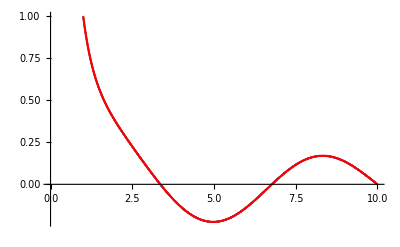

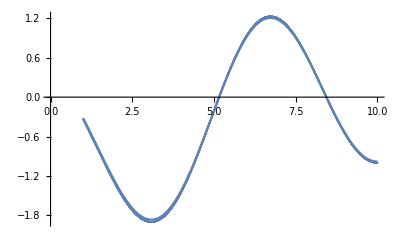

```mathematica
a=1;
b=10;
m1=1;
m2=1;
beta1=0;
beta2=0;
n=2;
s1=NDSolve[{x^2*u''[x]+x*u'[x]+(x^2-n^2)u[x]==0,u[a]==1,u[b]==0},u[x],{x,a,b}];
Show[ListPlot[data1],Plot[u[x]/.s1,{x,a,b},PlotStyle->Red]]
s2=NDSolve[{x^2*u''[x]+x*u'[x]+(x^2-n^2)u[x]==0,-a^2*u'[a]==m1-beta1,b^2*u'[b]==m2-beta2},u[x],{x,a,b}];
Show[ListPlot[data2],Plot[u[x]/.s2,{x,a,b}]]
```